# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ用

オリジナルを”/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story/”とする。
実行結果が妥当かは上記と比較する。

Rev: ディレクトリ名の変更

メモ：grdmのvoc付与に関してはreferrerがないのでどのくらい取れるか確認する。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.93453589769253×10^9

#### 変数

```mathematica
date="20240824"
```

20240824

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci"
base["cs"]="T=cs"
base["la"]="T=la"
base["wk"]="T=wk"
base["gr"]="T=gr"
base["all"]="T=4"
```

T=ci

T=cs

T=la

T=wk

T=gr

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20240824.rcoslog0002.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20240824.rcoslog0002.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

24068170 330360867 12013827990 log-20240824.rcoslog0002.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=ci

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

6652753

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{6652753,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.93345×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2024-08-23T15:00:00Z
log.ci0001.aws.wa01.yobi
17.241.219.84
host":"-
user":"-
3.93345×10^9
method":"GET
https://cir.nii.ac.jp/crid/1380572092445211535
code":"200
size":"12252
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.4 Safari/605.1.15 (Applebot/0.1; +http://www.apple.com/go/applebot)
http_x_forwarded_for":"\"17.241.219.84\"
request_time":"0.033
upstream_response_time":"0.033"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2024-08-23T15:00:00Z
log.ci0001.aws.wa01.yobi
124.243.137.90
host":"-
user":"-
3.93345×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130282271266216960
code":"200
size":"12678
-
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/104.0.0.0 Safari/537.36
http_x_forwarded_for":"\"124.243.137.90\"
request_time":"0.045
upstream_response_time":"0.045"}
1130282271266216960
toCRID[-]

```mathematica
accessTime["ci"]=Map[#[[6]]&,strSplt1CCCC["ci"]];
```

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=cs

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

4798

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{4798,15}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{4798,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/hub/home

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2024-08-24T00:28:07.036794357+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2024-08-23T15:28:24Z
log.cs0002.ksw.wa01.yobi
35.213.23.14
stream":"stdout
user":"-
3.93345×10^9
date_time":"23/Aug/2024:15:28:23 +0000
https://jupyter.cs.rcos.nii.ac.jp/hub/static/js/utils.js?v=20240820020745
method":"GET
code":"200
https://jupyter.cs.rcos.nii.ac.jp/hub/home
agent":"Mozilla/5.0 (X11; Linux x86_64) AppleWebKit/537.36 (KHTML, like Gecko) HeadlessChrome/88.0.4324.150 Safari/537.36
size":"4384
app_user":"0d90424cf9258d120979c02c1c5fb926400500b782bc8f8fe67f2df7b517a03f

```mathematica
accessTime["cs"]=Map[#[[6]]&,strSplt1CCCC["cs"]];
```

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=la

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

54035

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{54035,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0002.aws.wa01.yobi,8640},{log.la0003.aws.wa01.yobi,8640},{log.la0001.aws.wa01.yobi,36755}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{36755,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{8640,12}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{8640,12}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
{"user":"-
date_time":"24/Aug/2024:00:00:03 +0900
method":"GET
path":"/
code":"200
size":"2
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{36755,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:00Z
log.la0002.aws.wa01.yobi
{"user":"-
date_time":"23/Aug/2024:15:00:00 +0000
method":"GET
path":"/health
code":"200
size":"2
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{8640,12}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

2024-08-23T15:00:09Z
log.la0003.aws.wa01.yobi
{"user":"-
date_time":"23/Aug/2024:15:00:09 +0000
method":"GET
path":"/_chp_healthz
code":"200
size":"15
referer":"-
agent":"kube-probe/1.28+
http_x_forwarded_for":"-
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{8640,12}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{54035,12}

```mathematica
strSplt1R["la"][[1]]
```

{2024-08-23T15:00:03Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"-,size":"2,method":"GET,date_time":"24/Aug/2024:00:00:03 +0900,code":"200,path":"/,{"user":"-,session_id":"-"},referer":"-,agent":"kube-probe/1.28+}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
(*logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)*)
```

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.93345×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"-
size":"2
method":"GET
3.93345×10^9
code":"200
https://lms.nii.ac.jp/
{"user":"-
session_id":"-"}
-
agent":"kube-probe/1.28+

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{54035,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2024-08-23T15:00:03Z
log.la0001.aws.wa01.yobi
-
size":"2
method":"GET
3.93345×10^9
code":"200
https://lms.nii.ac.jp/
{"user":"-
session_id":"-"}
-
agent":"kube-probe/1.28+

```mathematica
accessTime["la"]=Map[#[[6]]&,strSplt1CCCC["la"]];
```

### データ(wk)

2024 年度に入ってから、 log.wk1001.xxx 以外に log.wk3001.xxx が挿入されているので場合わけする。

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=wk

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

1129338

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{1129338}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{1129338,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2024-08-23T15:00:38+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.93345×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

DateList::str: String 51.20 cannot be interpreted as a date in format Automatic.

AbsoluteTime::arg: Argument DateList[51.20] cannot be interpreted as a date or time input.

DateList::str: String .18.24 cannot be interpreted as a date in format Automatic.

AbsoluteTime::arg: Argument DateList[.18.24] cannot be interpreted as a date or time input.

DateList::ambig: Warning: the interpretation of the string 5.11 as a date is ambiguous.

DateList::str: String .226.20 cannot be interpreted as a date in format Automatic.

General::stop: Further output of DateList::str will be suppressed during this calculation.

AbsoluteTime::arg: Argument DateList[.226.20] cannot be interpreted as a date or time input.

General::stop: Further output of AbsoluteTime::arg will be suppressed during this calculation.

DateList::ambig: Warning: the interpretation of the string .19.8 as a date is ambiguous.

DateList::ambig: Warning: the interpretation of the string 5.11 as a date is ambiguous.

General::stop: Further output of DateList::ambig will be suppressed during this calculation.

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2024-08-23T15:08:15Z
log.wk1001.oci.wa01.yobi
173.252.107.116
user":"-
method":"GET
3.93345×10^9
code":"200
https://jdcat.jsps.go.jp/records/32442/export/bibtex
size":"31
http_x_forwarded_for":"173.252.107.116"}
-
agent":"facebookexternalhit/1.1 (+http://www.facebook.com/externalhit_uatext.php)

```mathematica
accessTime["wk"]=Map[#[[6]]&,strSplt1CCCC["wk"]];
```

### データ(gr)

```mathematica
dir["gr"]=mountdir<>"log/D="<>date<>"/"<>base["gr"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=gr

#### データの読み込み

```mathematica
file["gr"]="self.1"
```

self.1

```mathematica
str["gr"]=Import[dir["gr"]<>"/"<>file["gr"],"String"];
```

```mathematica
(strSplt["gr"]=StringSplit[str["gr"],"\n"])//Length
```

1096997

```mathematica
(strSplt1["gr","pre"]=Map[StringSplit[#,"\t"]&,strSplt["gr"]])//Dimensions
```

{1096997}

```mathematica
(strSplt1["gr"]=Cases[strSplt1["gr","pre"],x_/;Length[x]==21])//Dimensions
```

{844896,21}

#### カラムポジションの調整

CiRとカラムポジションをあわせる。
1: <- 1
2: <- 2
3: remote <- 10
4: host <- 7
5: user <- 15
6: date <- 13
7: method <- 3
8: path <- 4
9: code <- 6
10: size <- 12
11: ref <- 9
12: agent <- 5

```mathematica
rp["gr"]={1,2,10,7,15,13,3,4,6,12,9,5}
```

{1,2,10,7,15,13,3,4,6,12,9,5}

```mathematica
(strSplt1R["gr"]=Map[#[[rp["gr"]]]&,strSplt1["gr"]])//Dimensions
```

{844896,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["gr"]="https://rdm.nii.go.jp"
```

https://rdm.nii.go.jp

```mathematica
pathreplace["gr"][path_]:=Module[{pathhead,epath},
pathhead="https://rdm.nii.go.jp";
epath=StringDrop[path,7];
epath=StringSplit[epath," "][[1]];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["gr"]=Map[ReplacePart[#,8->pathreplace["gr"][#[[8]]]]&,strSplt1R["gr"]];
```

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧,1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["gr"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["gr"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数（日本時間）

```mathematica
logdateToTime["gr"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-1}]]]+(9*60*60)
```

```mathematica
strSplt1CC["gr"][[1]][[6]]
```

date_time":"2024-08-23T14:59:02.475964243+00:00

```mathematica
strSplt1CC["gr"][[1]][[6]]//logdateToTime["gr"]
```

3.93348×10^9

```mathematica
strSplt1CCC["gr"]=Map[ReplacePart[#,6->logdateToTime["gr"][#[[6]]]]&,strSplt1CC["gr"]];
```

```mathematica
strSplt1CCC["gr"]//Length
```

844896

```mathematica
Cases[strSplt1CCC["gr"],x_/;x[[6]]<=0]
```

{}

remoteをアドレスのみに。

```mathematica
ip["gr"][str_]:=Module[{s},
s=StringSplit[str,"\":\""];
If[Length[s]==1,"",s[[2]]]
]
```

```mathematica
strSplt1CCCC["gr"]=Map[ReplacePart[#,3->ip["gr"][#[[3]]]]&,strSplt1CCC["gr"]];
```

```mathematica
strSplt1CCCC["gr"][[26]]//TableForm
```

2024-08-23T15:09:02Z
log.gr0001.aws.wa01.yobi

host":"ip-10-20-1-17.ap-northeast-1.compute.internal
user":"
3.93348×10^9
{"method":"GET
https://rdm.nii.go.jp/v2/nodes/gvswq/files/
code":"
size":"-

agent":"

```mathematica
accessTime["gr"]=Map[#[[6]]&,strSplt1CCCC["gr"]];
```

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
(*Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]*)
```

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"],strSplt1CCCC["gr"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{115.189,{8685820}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{8685820}

```mathematica
accessTime[4]=Map[#[[6]]&,idxLog[4]];
```

```mathematica
Cases[accessTime[4],x_/;x<0]//Length
```

767527

```mathematica
(unexTimePos=Position[accessTime[4],x_/;x<0]//Flatten)//Length
```

767527

```mathematica
unexTimePos[[1]]
```

2756043

```mathematica
idxLog[4][[unexTimePos[[1]]]]//TableForm
```

2024-08-23T15:45:34Z
log.wk3001.oci.wa01.yobi
2024-08-23T14:00:00+00:00
wftag":"weko-nginx.stdout
user":"-
-5.58558×10^10
method":"GET
me":"23/Aug/2024:14:00:00 +0000
path":"/records/39552/export/json
size":"1649
"HTTP/1.1
code":"200
2756043

怪しいタイムスタンプが多すぎる。-> 新しく入ったjcが原因、あとで処理を追加する。

```mathematica
accessTime[4]//Min
```

### ckanデータの処理(基盤全て)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{8685820}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

5643

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

5643

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{8685820}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

1

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

1

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

5644

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

5644

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{97.296,{6652753,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2024-08-24T14:09:22Z
log.ci0001.aws.wa01.yobi
100.10.11.171
host":"-
user":"-
3.93353×10^9
method":"GET
https://cir.nii.ac.jp/crid/1524232505008572416/mendeley
code":"200
size":"453
-
agent":"Mozilla/5.0 (Linux; Android 8.0; Pixel 2 Build/OPD3.170816.012) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/40.0.4579.1105 Mobile Safari/537.36
http_x_forwarded_for":"\"100.10.11.171\"
request_time":"0.020
upstream_response_time":"0.021"}
1524232505008572416
toCRID[-]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{6652753}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690013498979877504,1690576448927641088,1690857923910065152,1690576448930304640,1690294973946873088,1690013498971571712,1690013498966838912,1690013498979062528,1690013498975900288,1690857923899831040,1690294973955341952,1690857923910924032,1690013552764958720,1690013498966415104,1690857923908940416,1690857923905427456,1690857923901692928,1690013498976994688,1690294973949072640,1690294973951847168,1690294973946878464,1690576448923586944,1690013498965781760,1690013498965459456,1690576448928803840,1690294973950729984,1690013498968635776,1690013498975186432,1690013498964823680,1690013498974102016,1690857923905148672,1690294973953739520,1690576448919311488,1690576448923715584,1690013498979127424,1690013498975861888,1690857923900722048,1690857923909119488,1690857923908330112,1690857923911917312,1690013498969545600,1690013498966132736,1690857977695243136,1690013498976688000,1690013498966114816,1690576448930265088,1690576448927631616,1690013498966019072,1690576448920165120,1690294973953905152,1690013498965099136,1690294973948768640,1690857923902538752,1690857923909244544,1690857923910357888,1690294973943639296,1690013498970252928,1690576448929949696,1690013498976105600,1690857923904606208,1690013498965119744,1690013498968655744,1690013498970619008,1690294973948689920,1690857923906462336,1690013498981038336,1690294973948800384,1690294973952977280,1690857977694951296,1690013498976717824,1690576448927641088,1690294973952836096,1690857923906337792,1690013498968989568,1690857923900425984,1690294973955766784,1690294973953769216,1690013498968655744,1690294973941909248,1690294973945157760,1690013498965550080,1690576448923416704,1690857923911347200,1690013498976990208,1690013498965926272,1690857923899878144,1690294973957177344,1690576448929195392,1690013498969851392,1690576448929039488,1690294973947165696,1690013552764958336,1690294973952951680,1690576448930095872,1690013498965459456,1690013498970252928,1690013498966272000,1690294973943631616,1690576448923873152,1690576448924287488,1690576502718215936,1690576448920374656,1690013498968766080,1690013498975618304,1690013498975773184,1690294973953233664,1690013498971175424,1690576448922672768,1690013498972931968,1690294973955009024,1690857977694840832,1690576448929698432,1690013498968075648,1690857923905221888,1690013498966186624,1690013498969371520,1690013498975944576,1690013498976420864,1690294973955127424,1690576448925396224,1690857923906533504,1690013498971797760,1690294973951369472,1690576448930376064,1690857923902107392,1690294973957483136,1690857923899595904,1690576448920843136,1690857923896367232,1690013498970596608,1690013498965059072,1690013498964837248,1690013498965059072,1690013498964837248,1690013498965059072,1690013498967411840,1690857923907746176,1690857923906702592,1690013498976055936,1690294973944056576,1690013498967248896,1690013498967395584,1690013498981159680,1690857923911364480,1690576448919241856,1690013498972219008,1690576448922857856,1690857923896367232,1690857923906823552,1690013498977404032,1690013498970293760,1690576448919423104,1690294973943854976,1690857923910634496,1690294973952401024,1690576448933947648,1690294973952497536,1690857923901692928,1690576448922855936,1690294973943420928,1690294973942580992,1690294973955298816,1690013498965310464,1690857977694837888,1690294973941381376,1690576448925272576,1690294973943721728,1690013498970303232,1690857923895582208,1690857923896763392,1690576448933559808,1690013498970695168,1690857923907184384,1690013498977882752,1690013498969285504,1690294973941689344,1690576448929988992,1690013498976081152,1690013498976122112,1690013498974048384,1690294973955754752,1690857923910587904,1690857923908534528,1690857923906462336,1690013498981505280,1690013498980285568,1690576448928246912,1690576448923416704,1690013552764984832,1690857923900576640,1690857923910071552,1690013498977834752,1690013498968989568,1690294973953173120,1690294973950846592,1690294973952830080,1690576448922482688,1690013498968766080,1690013498968803968,1690576448929601792,1690576448919398144,1690576448924827136,1690294973953142784,1690857923910708992,1690013498972197888,1690857923907992832,1690576448929131392,1690013498969473792,1690576448930057216,1690576448918733952,1690857923905889408,1690013498976752128,1690013498978089600,1690576448918733952,1690294973947040640,1690857923901189376,1690576448929598208,1690576448920701824,1690294973942401408,1690013498974920448,1690576448930091904,1690576448932423680,1690013498966314240,1690576448933892224,1690013498975376128,1690013498966791040,1690013498975963776,1690294973946728192,1690576448922516608,1690294973943957760,1690013498970594560,1690857923899486720,1690857923894986624,1690294973953267456,1690294973958274048,1690013498970472960,1690576448919603072,1690294973943922944,1690576448934216704,1690857923909585408,1690013498975320064,1690013498976102528,1690294973947445120,1690013498970247424,1690857923899874176,1690576448920333440,1690857923900620032,1690294973942343296,1690013498980851200,1690013498976565120,1690576448933744896,1690013498964576896,1690576448929105792,1690576448928890880,1690857923906097152,1690013498974920064,1690013498970043648,1690576448923271424,1690013498970599552,1690576448923391360,1690013498979877504,1690294973947005696,1690576448920133120,1690576448919054848,1690013498969528320,1690294973951368960,1690294973948299008,1690294973947161728,1690857923905601536,1690576448933300096,1690013498976017024,1690576448931611776,1690013498976130560,1690857923901745792,1690576502718139520,1690013498976957056,1690857923902203904,1690013498975937536,1690294973947669888,1690576448933299200,1690576448934594560,1690013498977356416,1690857923902326144,1690013498978918784,1690013498978920448,1690013498964744320,1690013498966736640,1690576448920154752,1690857923902141952,1690857923896240512,1690294973953757824,1690013498970875520,1690576448925272576,1690013498969237376,1690013498975941376,1690576448929892608,1690294973942519296,1690576448929988992,1690294973956911744,1690576448929881984,1690013498976382592,1690294973942554880,1690294973953599232,1690013498976268928,1690013498969639168,1690013498974382848,1690013498978135680,1690857923907567232,1690013498975831040,1690013498975940352,1690013498972620160,1690857923910633728,1690576448927419008,1690013498976446848,1690295027741684096,1690013498975900672,1690294973947284992,1690294973955754752,1690013498968715648,1690013498970910336,1690294973953739520,1690857923905384064,1690013498977001600,1690013498979062528,1690013498965326464,1690857923906924672,1690013498973119488,1690857923900046592,1690576448925527680,1690294973942086144,1690857923900588032,1690576448925951488,1690013498978212736,1690013498966826880,1690857923906690432,1690013498970176128,1690013498965620864,1690294973947166336,1690294973950729984,1690294973942106752,1690013498970700544,1690294973957076992,1690857923904887552,1690857923900692992,1690294973945156864,1690857923907205248,1690294973947167488,1690576448922735616,1690576448929540736,1690857923910547072,1690013498966826880,1690857923896783104,1690013498964823680,1690576448928803840,1690294973947778176,1690013498965207680,1690013498964661632,1690013498978850944,1690013498976261376,1690013552764775552,1690013498980252544,1690013498964893696,1690576448922843520,1690576448927522048,1690576448930007808,1690576448919827200,1690857923900247552,1690013498972277888,1690576502718544768,1690576448927088512,1690576448925819648,1690294973947306880,1690857923906848512,1690294973947000448,1690576448923588864,1690294973956995328,1690294973946315136,1690294973947044480,1690013498969321216,1690576448918409088,1690013498972099328,1690857923906553472,1690294973953259136,1690857923896027392,1690857923907239296,1690857923900247552,1690857923906219648,1690294973946847232,1690294973947306880,1690013498973749120,1690013498971479936,1690013498967031808,1690294973945157760,1690013498967060096,1690295027741565696,1690013498980172672,1690576448923588352,1690857923900427008,1690294973946873088,1690576448924432896,1690857923910255488,1690013498976115968,1690294973946632704,1690576448920866688,1690857923905420544,1690294973944030592,1690294973946876288,1690576448930355968,1690576448922803712,1690013498970377728,1690013498976109184,1690857923901026816,1690576448930309760,1690013498965205376,1690294973947010816,1690857923906844288,1690294973948150912,1690013498966633728,1690013498979877504,1690013498976383872,1690013498971645056,1690857923904505984,1690576448919044864,1690576448930252416,1690294973949060608,1690857923908391936,1690857923904091776,1690857923911851264,1690013498964621952,1690857923907161472,1690013498970303232,1690857923907122304,1690013498977215872,1690013498978928640,1690013498970838784,1690013498977403520,1690294973942951552,1690857923905039104,1690013498965198720,1690013498967040000,1690013498970166144,1690576448920154752,1690857923909176064,1690857923906462336,1690294973947167488,1690013498976637312,1690294973949618944,1690013498965339264,1690013498976630272,1690857923906533120,1690294973946348800,1690576448920894848,1690013498969603072,1690576448928004992,1690013498970140672,1690294973955528576,1690857923906990336,1690013498966174592,1690013498974382848,1690857923906266752,1690857923901319936,1690013498976851840,1690013498970052480,1690294973953083520,1690576448918941056,1690576448934644864,1690857923909088768,1690013498965678208,1690013552764990976,1690576448924788736,1690013498978916480,1690013498971178880,1690013498967413504,1690013498980991104,1690013498980991104,1690294973955769984,1690013498965219328,1690857923910919552,1690013498969010816,1690294973950935040,1690013498966422016,1690013498965713152,1690576448924017408,1690857923895412992,1690013498971923840,1690857923906279680,1690013498970319360,1690294973957408512,1690857923900298880,1690576448924023296,1690576448920895744,1690576448919398144,1690576448930458496,1690576448923275392,1690294973952108416,1690013552764915456,1690857923901204864,1690294973951521024,1690857923900730112,1690857923905842944,1690013498976021248,1690013498973629952,1690294973957314944,1690576448920154752,1690576448932241280,1690013498965100032,1690857923910861952,1690013498980195456,1690013498969321216,1690013498964748672,1690857923900730752,1690857923900730752,1690857923908564992,1690857923902528512,1690857923905393152,1690013498978961024,1690013498979062528,1690013498978961024,1690013498969602176,1690857923911879168,1690294973953246720,1690013498964664320,1690013498970299264,1690576502718194176,1690857923907846784,1690857923905955712,1690857923904884864,1690857923900425984,1690013498964618624,1690013498972180992,1690857923900394368,1690013498964692864,1690857923907131008,1690013498978918784,1690294973953422976,1690013498964583936,1690857923900934016,1690294973957578624,1690857923909526400,1690857923911849600,1690857923911162112,1690013498978415488,1690576448923271424,1690576448924928384,1690576448928345216,1690013498968766080,1690857923900729088,1690857923901582848,1690013498966174592,1690013498975747328,1690013498966417664,1690857923902141952,1690013498979049728,1690294973954897792,1690576448924425472,1690013498971923840,1690857923895622272,1690857977694849024,1690857923905596800,1690294973953116800,1690576448923720576,1690294973942319232,1690294973953230464,1690013498964927744,1690013498977735168,1690013498976557696,1690294973957458688,1690857923905884544,1690013498978135680,1690013498965837568,1690294973947161728,1690013498964672768,1690013498976122112,1690576448921613440,1690857923901980032,1690013498964620928,1690013498972282752,1690013498971321088,1690013498976086272,1690576448931938176,1690576502718405760,1690013498975245952,1690013498980854528,1690857923897425280,1690013498974324736,1690857923897164416,1690857923908837504,1690294973944131072,1690576448931120384,1690013498978339456,1690013498965039360,1690294973953554304,1690294973946394880,1690857977695219072,1690576448922449280,1690294973942974080,1690294973955772544,1690013498976105600,1690294973945155584,1690294973948462464,1690013498978918016,1690576448929783168,1690013498978920064,1690294973945411072,1690013498979878912,1690857923900040576,1690013498969237376,1690013498978920064,1690857923896344832,1690857923905964800,1690857923901242496,1690857923895651712,1690013498968703872,1690576448919672320,1690013498969540224,1690294973943591552,1690857923906462336,1690857923910673152,1690013498964577920,1690294973957738112,1690857923910270592,1690857923897106048,1690013498976946176,1690013498975248896,1690857923899800320,1690013498965334912,1690576448934605696,1690294973955773440,1690013498980877568,1690013498981130624,1690576448924788736,1690294973945514624,1690857923900726784,1690857923896344832,1690576448920426112,1690013498978070400,1690013498965680384,1690576448928696960,1690013498975861888,1690857923905893248,1690013498968747520,1690013498974920064,1690857923896367232,1690857923908221952,1690294973943412992,1690857923895087744,1690013498965153664,1690857923900729088,1690013498965341312,1690576448932928768,1690013498970542080,1690013498964586112,1690576448923416704,1690857923906279680,1690576448932352768,1690294973945501696,1690013498969086464,1690576448933730048,1690576448925155328,1690013498980841728,1690013498976994688,1690576448929783168,1690013498969081984,1690013498965139584,1690294973956643712,1690857923900971264,1690013498971085696,1690013498966664704,1690013498966664704,1690013498966664704,1690013498980733568,1690294973957016192,1690857923902977920,1690576448928400256,1690576448929046016,1690857923900837376,1690294973946028416,1690857923898822784,1690013498966729728,1690857923900732160,1690576448923386496,1690857923895707136,1690294973947167488,1690294973948002560,1690857923911214336,1690576502718204544,1690013498969850240,1690857923906250240,1690294973946678272,1690294973957691904,1690576448918203008,1690576448928345216,1690576448923588352,1690857923906886784,1690013498977009920,1690013498965482752,1690576448932351232,1690294973941451264,1690576448929783168,1690294973947162368,1690294973941517696,1690857923904061440,1690013498971600512,1690857923902203904,1690576448919987968,1690294973955638656,1690013498979880960,1690013498969142016,1690294973953276032,1690857923906097152,1690013498966778240,1690576448929910400,1690013498967371904,1690576448923721088,1690013498965678208,1690857923906238208,1690013498967373824,1690294973948759168,1690013498971939840,1690857923901881472,1690576448929822336,1690857923905456512,1690013498964893696,1690857923900580736,1690294973941694464,1690576448918409088,1690576448925272576,1690013498965463936,1690013498978920448,1690294973953534208,1690013498976487296,1690013498968702848,1690013498976014720,1690294973944010752,1690013498972124416,1690294973954953728,1690576448922760320,1690294973948530816,1690857923902325120,1690857923901831040,1690857923895101056,1690013498967472640,1690013498969678720,1690013498971178880,1690294973948462464,1690013498972470784,1690576448929662720,1690857923907075072,1690294973953378816,1690013498966183936,1690576448932869376,1690576448920196864,1690013498966900224,1690294973944098688,1690857923900732928,1690576448933447424,1690013498981596288,1690576448927896960,1690857923907641600,1690013498966896384,1690576448929553024,1690294973953624320,1690576448927267584,1690013498974477568,1690013498971889280,1690013498976563328,1690013498975804288,1690013498972183168,1690857923896344832,1690013498976782720,1690013498972078976,1690857923900725888,1690857923911183488,1690576448934395904,1690576448933943168,1690013552764902656,1690857923896480384,1690013498964891264,1690857923895582208,1690013498974929152,1690576448933278464,1690294973947966336,1690576448934016896,1690857923900914048,1690013498970165632,1690294973952374912,1690576448930379264,1690857923896315776,1690294973951368960,1690013498979864192,1690857923899030272,1690857923905084160,1690294973955275264,1690013498980252544,1690013498980174080,1690294973947157760,1690857923907037952,1690013552764760448,1690013498976087040,1690857923901492864,1690857923899209088,1690013498966925184,1690857923896344832,1690013498965866496,1690013498964932992,1690013498976378624,1690294973952836096,1690013498978070400,1690857923895615744,1690013498976141312,1690013498970252928,1690013498969321216,1690857923909281024,1690294973942530048,1690294973947669376,1690294973958064896,1690013498966633728,1690013498980184576,1690857923900588800,1690294973952144512,1690294973946715648,1690294973957071616,1690013498966415104,1690013498969528320,1690576448929404544,1690294973951368960,1690294973955841536,1690294973946278144,1690013498976544512,1690013498970335744,1690013498969473792,1690013498977385088,1690857977695050240,1690013552764996608,1690294973941358208,1690294973946957824,1690576448929787264,1690857923906847744,1690013498966084608,1690294973943631616,1690294973948630656,1690576448929682176,1690013498966473472,1690857923900564736,1690857923904983424,1690294973947163264,1690013498976080896,1690294973942103552,1690013552765119360,1690294973948310528,1690294973953117696,1690857923905117440,1690013498969237376,1690576448933854336,1690013498977488256,1690857923905650432,1690576448933626880,1690294973951236992,1690294973942710784,1690013498979044096,1690013498976268928,1690013498971744896,1690576448927490304,1690013498980077312,1690013498966434432,1690576448918768128,1690294973948522880,1690294973955009920,1690013498978865664,1690294973943924224,1690013498969662464,1690576448927720704,1690013498965067008,1690576448925429504,1690294973953386112,1690857923897588608,1690013498969435904,1690857923904517888,1690013498977882752,1690857977695210112,1690013498965218816,1690576448932059776,1690013498964927360,1690295027741543168,1690013498970914944,1690576448930411520,1690013498970601344,1690294973945608192,1690013552764956928,1690857923909307136,1690013498977385088,1690013498972223744,1690294973952347008,1690013498965837568,1690857923900257920,1690857923897392512,1690294973946318336,1690857923910673152,1690013498979057792,1690857923906973952,1690013498970600704,1690013498977774464,1690576448927896960,1690857923901492864,1690294973946278144,1690294973953070464,1690294973948996864,1690013498976124800,1690013498972412032,1690013498968777088,1690013498972198272,1690013498975314176,1690857923899159296,1690013498980546176,1690013498969850624,1690857923900722048,1690013498976017024,1690576448918136320,1690013552764771584,1690013498974324736,1690576448932344960,1690294973942103552,1690294973946183680,1690013498975947648,1690857923905084160,1690013498969764864,1690576448924425472,1690294973945155584,1690013498966085504,1690857923900098816,1690013498966733824,1690013498976016512,1690857923899611776,1690013498966800000,1690013498976087040,1690013498966851968,1690013498977673344,1690013498978913536,1690857923897598976,1690013498971913728,1690013498977774464,1690857923910371456,1690294973956780544,1690576448929910400,1690013498968739584,1690013498970745600,1690294973952520192,1690013498978135680,1690857923900732160,1690013498976261376,1690857923901624192,1690013498970162432,1690294973949052672,1690857923907012608,1690857923910565632,1690576448928771584,1690013498976548224,1690857923895352960,1690294973947754496,1690294973953947520,1690857923901607552,1690857923900056704,1690576448933731456,1690857923910641664,1690013498975239808,1690013498966908416,1690857923911694208,1690857923899831040,1690576448926262400,1690576448928345216,1690013498966314240,1690294973944820480,1690576448924310400,1690576448928692352,1690294973951764864,1690013498976254848,1690857923908086656,1690857923899494144,1690576448928949632,1690857923908611584,1690013498968918144,1690013498976059904,1690294973953156608,1690576448923961600,1690294973949771264,1690013498966881280,1690857923906499968,1690576448932113536,1690857923900824192,1690857923897564544,1690294973944532480,1690294973953751040,1690013498968970496,1690576448931659136,1690576448918283392,1690294973949995776,1690295027741856000,1690294973948701952,1690013498978434304,1690857923895026304,1690576448923424640,1690857923908494208,1690857923895650176,1690857923911517568,1690013498972216320,1690576448928880000,1690576448931159424,1690857923911297152,1690013498968140800,1690013498975818496,1690013498968737664,1690576448925385472,1690576448921868032,1690857923906454528,1690576448923354240,1690576448922814592,1690576448934779520,1690294973957922688,1690576448924542464,1690576448933029632,1690294973952958080,1690576448925003008,1690013498973700096,1690576448919243648,1690857923896824320,1690013498979007488,1690576448927930240,1690013498974644352,1690857923902548608,1690013498965607680,1690576448932240000,1690013498980624512,1690295027741473024,1690013498965150592,1690576448925074176,1690294973955073408,1690857923906724992,1690013498977854464,1690576448928290176,1690013498976139008,1690013498975754752,1690294973955080320,1690576448932028288,1690013498967772672,1690294973957493632,1690013498971226496,1690576448934071424,1690576448929384704,1690857923897570176,1690013498981043328,1690013498981364224,1690857923904952960,1690576448933415424,1690294973952292096,1690576448928294400,1690576448931196160,1690013498972183552,1690013498978050560,1690013498975427840,1690857923910653568,1690576448923468288,1690857923910033792,1690576448934369280,1690013498975990784,1690576448931744896,1690294973954331392,1690294973957956736,1690294973945519488,1690294973956837248,1690857923911684992,1690294973947738368,1690576448921495424,1690294973955785344,1690294973944234112,1690294973952066560,1690294973943304704,1690576448933987456,1690013498975489280,1690576448928441088,1690857923900766848,1690857977694966016,1690576448935178240,1690294973954383232,1690294973944601984,1690857923899845248,1690013498966431616,1690857923901039232,1690294973953910656,1690857923909442176,1690013498964707712,1690857923908578816,1690013498978062080,1690576448931316992,1690013498965239040,1690576448925621376,1690576448919433728,1690857923897884800,1690294973952139136,1690576448934712960,1690576448935001856,1690294973953622912,1690576448920901760,1690576448929777792,1690295027741693440,1690013498965468672,1690013498981337344,1690013498981299584,1690576448921430272,1690294973955553280,1690294973946087168,1690013498981761536,1690013498981770368,1690294973947945344,1690576448928522880,1690857988185386752,1690857923908356736,1690857977695247872,1690013498972140544,1690857923906145536,1690857923904505344,1690294973953153664,1690013498981115904,1690857923908765952,1690294973951667968,1690013498965134848,1690576448933961216,1690294973957551360,1690013498968037376,1690013498976737408,1690013498970536320,1690857923908297600,1690857923898172160,1690576448929937280,1690857923907757696,1690294973950396032,1690294973946684160,1690857923907774976,1690013498971696768,1690857923898463872,1690294973943049344,1690857923901291904,1690576448932495232,1690294973957481728,1690295027741644800,1690013498975827968,1690294973947192448,1690857923895705344,1690295027741631872,1690857923901348992,1690294973953490304,1690576448921752576,1690857923907226752,1690013498976906880,1690013498975086464,1690013498975234688,1690013498976617472,1690857923906097664,1690576448933275008,1690857923901547264,1690857923908186752,1690576448920157184,1690576448934811008,1690013498970240384,1690576448930714496,1690013498970600704,1690013498965714432,1690857923899206912,1690857923910880000,1690857923901134464,1690857923911908224,1690294973947305600,1690857923901863552,1690857923905582976,1690013498964682496,1690013498979902464,1690857923906963328,1690857923906926720,1690857923897161984,1690013498964623488,1690857923898892416,1690294973944090880,1690576448923721856,1690013498966308224,1690857923905749248,1690857923908236416,1690013498967131520,1690857923905836416,1690576448924126976,1690857923895237504,1690013498976993920,1690013498980631936,1690013498970596608,1690294973953505152,1690013498976487296,1690857923906365056,1690576448929695488,1690576448929695488,1690857923900947328,1690013498972036736,1690576448933815680,1690576448929422592,1690013498971079296,1690294973943619072,1690857923910461440,1690013498966664704,1690013498966664704,1690857923905628672,1690013498977022464,1690013498964939520,1690857923906961920,1690294973945845376,1690013498965059072,1690576448934116480,1690013498965059072,1690013498965059072,1690013498976942720,1690576448925140096,1690576448920148864,1690857923907529984,1690013552764761728,1690013498975947648,1690013498968694656,1690857923910708992,1690294973953788032,1690857923895418240,1690576448918059264,1690857923896852736,1690294973942275072,1690013498970544000,1690576448920894848,1690013498971277824,1690294973952952064,1690576448928652800,1690013498965393152,1690857923897598976,1690294973953754880,1690857923906852864,1690294973946957824,1690857923903997568,1690294973943569792,1690576448923416704,1690013498975895808,1690013498970378240,1690013498969319552,1690576448924425472,1690576448927413120,1690013498976471808,1690013498980201472,1690857923904582912,1690013498977735168,1690294973951563648,1690857923908387584,1690857923900722048,1690294973953905536,1690013498971569024,1690295027741573632,1690013498966925184,1690576448932974720,1690013498976523136,1690294973945514624,1690576448920251264,1690294973943639296,1690857923911917312,1690013498981163264,1690013498974324736,1690013498976105600,1690576448918412416,1690576448930227712,1690013498980704384,1690013498979934208,1690013498964744320,1690294973952952064,1690013498969540224,1690013498969758336,1690576448930567680,1690013498965827456,1690857923901726464,1690294973953312256,1690013498970594560,1690576448927413120,1690294973943915264,1690857923901750272,1690294973948768640,1690857923907136512,1690013498978879104,1690294973942341760,1690013552764777984,1690857923908854656,1690013498971166592,1690857923905524480,1690576448925272576,1690013498980403200,1690013498974121088,1690857923899717376,1690857923906924672,1690013498979934208,1690013498977385088,1690013498966826880,1690013498964735488,1690857923899159296,1690013498977073664,1690013552764778368,1690857923910282880,1690013498977276544,1690294973953113344,1690013498976689792,1690013498978013184,1690857977694983424,1690576502718544768,1690013552764957440,1690013498971778432,1690013498968989568,1690294973952977664,1690857923902325120,1690294973954347648,1690857923911276800,1690857923896638848,1690013552764983680,1690857923909178880,1690294973951568384,1690013498976115584,1690857923907956352,1690294973946908672,1690576448930411520,1690294973956978816,1690857923907015168,1690013498976087040,1690013498967079040,1690857923910657920,1690576448933794176,1690857923905964800,1690857923908595072,1690013552764769536,1690576448934628096,1690294973957397120,1690294973948493696,1690576448924849280,1690857923907362816,1690857923895677312,1690013498969851008,1690294973955528576,1690294973953768832,1690013498973092864,1690857923897324032,1690576448928386048,1690294973946854400,1690013498964725248,1690013498971178880,1690013498968907776,1690013498975945472,1690013498978912768,1690576448930252416,1690857923902056960,1690013498980620928,1690013498977611520,1690013498978913536,1690013552764849920,1690294973946309504,1690013498972095872,1690857923895409024,1690294973947284992,1690013498975861888,1690576448927088512,1690013498968694656,1690294973945397632,1690013498969136640,1690013498970606464,1690857977695030656,1690013498964887552,1690294973945199616,1690013552764762496,1690013498970599552,1690013498969959424,1690013552764769536,1690013498970162432,1690857923911276800,1690013498980879360,1690857923904404096,1690013498979175552,1690857923904396928,1690576448918672128,1690013498970853120,1690576448928705664,1690857923900722048,1690013498975419008,1690013498966160000,1690013498965901056,1690013498969114752,1690294973947172864,1690294973946385792,1690013498965360384,1690576448929783168,1690857923906362240,1690857923911879168,1690857923907641600,1690013498966995712,1690013498978810112,1690576448919184512,1690294973942108288,1690013498979865088,1690857923909281024,1690857923910919552,1690013498966900224,1690857923895412992,1690857923910071552,1690013498976561792,1690576448922482688,1690857923901483904,1690013498970152832,1690013498979939712,1690294973954347648,1690013498969758336,1690857923905582976,1690013498980789632,1690013498975931136,1690013498966633728,1690294973952722048,1690857923901319040,1690013498979127424,1690294973945534336,1690576448918136320,1690857923904901120,1690013498965393152,1690294973945197312,1690013498972620160,1690294973953553152,1690576448930343808,1690013552764985216,1690576448924635776,1690013498973865984,1690576448929662720,1690576448928803840,1690576448929845376,1690013498976016512,1690857923910441216,1690013498975990784,1690013498969595392,1690294973955161344,1690576448923530368,1690857923911004928,1690857923900580736,1690013498970772224,1690857923906620928,1690013498976447616,1690576448922482688,1690857923896783104,1690576448919684736,1690013498971178880,1690013498975195392,1690013498971450496,1690576448934626816,1690013552764989440,1690013498975424000,1690294973953554304,1690576448923616000,1690294973942554880,1690576448928705664,1690013498965099136,1690013498979062528,1690294973941668096,1690294973942993664,1690576448923271424,1690857923895418240,1690013498969319552,1690857923895651712,1690013498967211264,1690576448918423680,1690294973947305600,1690857923903939840,1690576448934215936,1690013498968952448,1690294973949828736,1690857923907184384,1690013498972247168,1690857923905524480,1690294973947427072,1690857923906462336,1690294973952373632,1690294973945886848,1690294973953228160,1690294973957092992,1690013498965291136,1690576448919054848,1690013498971778432,1690576448922449280,1690857923905578496,1690013498969319552,1690013498966073856,1690857923906252672,1690013498965718656,1690294973946988160,1690576448930308992,1690294973943483392,1690576448918566528,1690013498965161088,1690857923902180224,1690013498969854208,1690013552764987008,1690576448927641088,1690857923897193344,1690857923901609344,1690294973952823040,1690295027741544064,1690013498971923840,1690013498967345664,1690576448934068096,1690013498980252544,1690857923906279680,1690294973957691904,1690013552764902656,1690857923907132288,1690013498968655744,1690295027741565696,1690013498978879104,1690294973948759168,1690576448930379264,1690294973946617728,1690013498974835200,1690857923901881472,1690857923900399616,1690013498968654848,1690857923901492864,1690013498972620160,1690294973945201664,1690013498965134336,1690857923900582656,1690013498970140672,1690294973953249792,1690013498970268928,1690294973941524608,1690576448927681792,1690013498965257472,1690857923911132160,1690857923910861312,1690576448928402560,1690013498977007232,1690013498976400512,1690576448932352768,1690013498966939648,1690295027741578112,1690294973948932864,1690013498964918272,1690013498976059904,1690857923907161472,1690013498975659136,1690013498981031296,1690013498966421248,1690857923907136128,1690294973952144512,1690857923899030272,1690576448919987968,1690857923904506496,1690294973941559296,1690294973953385728,1690013498965965952,1690576448920196864,1690013498980622336,1690857923896122624,1690013498969114752,1690294973955770880,1690013498978353280,1690857923895510400,1690013498975618304,1690857923896725632,1690857923906279680,1690013498966079104,1690013498975964544,1690576448927705216,1690576448928803840,1690576448929039488,1690294973945735680,1690013498966281856,1690294973958326144,1690294973955157120,1690857923906095232,1690857923901980032,1690294973957585536,1690857923900737536,1690857923910482432,1690857923896385280,1690013498975375232,1690013498969850624,1690013498975273856,1690013498975965056,1690013498970749184,1690294973952618752,1690857923906916992,1690013498968469120,1690013498970606464,1690294973953905152,1690857923906361600,1690857923896964480,1690294973948077952,1690857923901483904,1690295027741684096,1690294973953378816,1690857923906848512,1690294973946221824,1690857923897164416,1690294973942108288,1690857923904582912,1690294973946385792,1690013498965333504,1690857923907117952,1690576448922754048,1690013498975274752,1690857923906848512,1690013498970299264,1690013498977687552,1690576448924425472,1690013498964973568,1690857923908719744,1690576448923271424,1690857923906220800,1690013498969851008,1690013498978915200,1690013498968475904,1690013498975940352,1690013498965540352,1690013498978915584,1690013498976913536,1690013498978089600,1690294973947306880,1690576448923899392,1690576448929695104,1690013498976896256,1690294973950846592,1690576448920318336,1690857923906848512,1690576448933424640,1690013498969776256,1690576448922894080,1690294973957076096,1690857923905252992,1690857923908387584,1690013498980629120,1690013498978917632,1690013498979062528,1690294973953341312,1690576448930275968,1690576448922803712,1690857923900589696,1690013552764759168,1690013498977878784,1690857923895959040,1690857923909281024,1690576448918564736,1690013498967031808,1690857923904473216,1690294973958150144,1690013498975861888,1690013498965619328,1690013498976561792,1690294973957261824,1690013498967030272,1690576448932828544,1690013498966657152,1690576448928386048,1690013498974281856,1690013498965620864,1690013498976893568,1690576448934594560,1690857923897483264,1690013498975861888,1690013498971196160,1690857923909307136,1690294973942609920,1690857923895249792,1690013552764772864,1690013498979863552,1690013498977686784,1690013498977007232,1690857923897226368,1690294973946908672,1690857923900257920,1690294973946632704,1690857923907368448,1690576448933626880,1690013498966076288,1690294973957314048,1690576448932483584,1690013498965149312,1690294973956993920,1690294973958064896,1690294973945157760,1690013498966584448,1690294973953228160,1690857923901660416,1690294973945514624,1690294973953768832,1690013498965220992,1690576448933559808,1690013498966422016,1690013498973749120,1690294973947306880,1690576448927631616,1690294973941432320,1690013498972267136,1690013498966281856,1690013498977878784,1690013498974121088,1690013498971321088,1690013498978902272,1690294973955847680,1690576448919257600,1690013498976544512,1690576448930275968,1690013498970319360,1690857923905927936,1690013498970492288,1690294973947275392,1690857923895651712,1690013498978070400,1690013498976087040,1690013498972476032,1690857923904181376,1690857923904473216,1690013498969111936,1690857923901827072,1690857923902043008,1690013498965415168,1690013498966249344,1690576448928386048,1690294973957587584,1690294973956993920,1690576448924449152,1690013552764989440,1690294973951368960,1690013498966626304,1690013498965373312,1690857923897588608,1690294973952836096,1690013498976141312,1690857923895651712,1690857923910673152,1690857923905384064,1690857923906871680,1690857923906973952,1690857923906695168,1690013498979057792,1690576448929168640,1690013498976699520,1690576502718127232,1690013498976893568,1690013498975720192,1690013498976544512,1690294973946406016,1690857923903861504,1690857923900576640,1690576448934254720,1690013498971741184,1690857923903861504,1690294973942078720,1690294973942951552,1690013552764775808,1690857923910071552,1690294973954340736,1690013498973042048,1690857923905448448,1690857923904264960,1690013498974121088,1690013498968744064,1690294973942530688,1690013498976994688,1690576448924928384,1690013498978415488,1690013498964893696,1690576448923272704,1690576448932241280,1690294973945197824,1690013552764777088,1690576448929200896,1690013498980737408,1690013552764760448,1690013498971913728,1690013498965207680,1690576448929015040,1690013498976076032,1690857923910697728,1690013498965039360,1690576448930279808,1690576448920359936,1690857923910555648,1690294973954340736,1690294973941689344,1690013498966549248,1690576448919382656,1690857923905597824,1690013498976086272,1690013498977573888,1690576448919398144,1690294973947040640,1690857923896367232,1690013498970616576,1690013498965630592,1690576448930035200,1690857923901750272,1690294973942108288,1690013498966679168,1690857923911543296,1690013498980189056,1690013552764915456,1690857923910760320,1690857923906912384,1690013498975371264,1690857923896493056,1690857923910587904,1690294973955772544,1690576448924458624,1690294973942195712,1690857923910779008,1690294973943754368,1690013498968655744,1690857923910633728,1690013498965066368,1690294973951597952,1690857923895087744,1690013498971482624,1690013552764996224,1690013498976889088,1690857923910708992,1690857923901660416,1690576448934416512,1690013552764992128,1690294973953276032,1690013498967316352,1690013498969086464,1690576448931857152,1690857923900706048,1690857923900842240,1690013498976382592,1690576448918161536,1690294973953743104,1690013498975423360,1690576448922739968,1690576448920730752,1690857923906553472,1690013498967088512,1690857923900675584,1690576448918566528,1690013498967211264,1690857923900691200,1690576448924881536,1690294973947284992,1690576448934286592,1690294973950959104,1690576448919601664,1690576448923584128,1690294973955645568,1690013498976983936,1690013498975720192,1690013498966163712,1690576448924998272,1690576448924018816,1690857923907635840,1690294973946876288,1690857923902145536,1690294973941556096,1690294973945363968,1690857923901624192,1690294973957393664,1690294973942993664,1690576448930355968,1690857923904905472,1690857923901311104,1690576448924181760,1690576448930201856,1690294973948522880,1690576448918564736,1690576448930218112,1690576448927423360,1690013498972620160,1690013498966073856,1690013498976103424,1690857923910587904,1690576448933362176,1690013498971582848,1690013498975353472,1690576448924017408,1690013498964823680,1690576448923812096,1690013498977882752,1690013498964614144,1690857923906963328,1690013498970046464,1690857923907130112,1690857923904878464,1690857923897097216,1690857923895072896,1690576448920297344,1690857923905889408,1690857923896493056,1690576448933558784,1690294973952648192,1690576448929938816,1690294973947000448,1690013498964629760,1690013498965067008,1690576448924869376,1690857923905039104,1690013552764970624,1690857923895350144,1690013552764889472,1690576448927541760,1690294973942358656,1690576448926391168,1690857923910705024,1690576448930320000,1690857923911622272,1690857923896385280,1690857923894962304,1690857923910337280,1690013498969850240,1690857923906869248,1690857923901483904,1690013552765069824,1690857923899426048,1690294973946847232,1690294973942609920,1690013498968989568,1690857923905524480,1690857923899931392,1690013498975246976,1690013552764956544,1690857923909526400,1690013498967371904,1690857923895170688,1690013498978135680,1690294973945633024,1690857923907136896,1690576448920818048,1690013498967382144,1690013498977790976,1690857923905596800,1690857923897304192,1690013498964930176,1690013498977637376,1690294973953606144,1690294973947778176,1690857977695262336,1690013498966183552,1690576448934279680,1690857923899717376,1690013552764971136,1690013498977774464,1690013498976487296,1690013552764700800,1690576448919054848,1690294973946385792,1690013498966183552,1690294973942390784,1690013498980694272,1690576448919395456,1690013498964973568,1690294973953941504,1690013498965482752,1690576448929039488,1690857923906958336,1690294973957100800,1690294973953611008,1690857923896413056,1690013498976379008,1690576448934023296,1690857923902169472,1690013498970043648,1690013552764770048,1690013498976284416,1690013498969920000,1690013498966900224,1690013498968655744,1690576448934644224,1690013498966451712,1690013498975874688,1690576448931120384,1690013498968192000,1690294973950846592,1690576448918188800,1690013552764971136,1690013552764956544,1690013498969287808,1690294973957590784,1690013498965680384,1690857923909307136,1690294973944137216,1690013498968709120,1690013498969381504,1690857923900726784,1690857923900744960,1690857923906852864,1690576448928345216,1690013498971569024,1690013498966448000,1690013498972180992,1690857923899831040,1690013498964735488,1690013498968906752,1690576448928386048,1690013498970741504,1690294973952949888,1690857923905148672,1690013498976086272,1690857923910876032,1690576448927267584,1690294973947163264,1690576448923330048,1690857923906506240,1690294973943924224,1690294973957373696,1690294973941694464,1690294973947010816,1690013552764956544,1690294973946315136,1690576448923588864,1690294973941983872,1690857923901980032,1690857923907161472,1690576448928803840,1690576448933447424,1690294973957408512,1690576448932483584,1690013498976467840,1690013498965272448,1690576448928730112,1690294973953128448,1690294973952834176,1690857923900667264,1690576502718139520,1690294973950715392,1690013498970601344,1690013498964725248,1690013498965825024,1690013498966785408,1690576448931949952,1690013498977687552,1690013498975550976,1690013498976278016,1690013498966793856,1690013498971321088,1690576448933278464,1690294973948642176,1690294973954723712,1690013498976990208,1690013498971939840,1690013498970745600,1690576448918836224,1690294973945156864,1690013498980378112,1690013498965781760,1690013498973242752,1690857977694837888,1690013498981080576,1690013498966800000,1690013498968694656,1690576448919464448,1690857923907132288,1690857923906768256,1690294973953769216,1690857923899503232,1690013498976015104,1690294973953543168,1690857923906504960,1690576448919775616,1690013498965611776,1690013498974382848,1690013498970169600,1690013498976099968,1690013498976622848,1690013498981553408,1690857923901667840,1690576448929881984,1690013498977109120,1690294973946964352,1690013498968209536,1690294973957794560,1690013498980704384,1690013552764771584,1690013498970616576,1690013498975766144,1690294973953740672,1690295027741777536,1690013498980273280,1690857923908387584,1690576448933363200,1690013498965207680,1690013498970165632,1690013498976105600,1690013498965856768,1690294973953658368,1690013498966272000,1690013498966242304,1690013498978345728,1690857923894800512,1690576448927705216,1690576448930201856,1690013498974306688,1690013498967316352,1690294973947966336,1690857923911824768,1690857923906944256,1690013498965349376,1690576448923878144,1690857923904091776,1690576448929046912,1690857923896493056,1690013498975393408,1690857923895350144,1690576448920610944,1690013498980394880,1690576448919103488,1690013498976676736,1690857923896603008,1690857923906248064,1690013498976139776,1690576448923329408,1690576448932787712,1690013498975245952,1690013552764775808,1690857923900438144,1690294973957841664,1690013498975899392,1690857923896240512,1690857923910255488,1690576448924928384,1690013498976103424,1690013552764774144,1690294973945372672,1690576448919544448,1690013498973865984,1690857923906849792,1690294973942826112,1690013498970165632,1690294973951563648,1690576448919987968,1690013498965959168,1690857923911622272,1690013498972180992,1690013498976926208,1690294973956867328,1690013552764958336,1690857923902419456,1690013498975463168,1690857923905422336,1690857923897199488,1690013498979062528,1690576448928522368,1690576448920499072,1690857923906620160,1690294973947009792,1690857923906535040,1690013498976021248,1690013498978563712,1690013498967257728,1690013498975322368,1690857923896344832,1690576448927720704,1690294973952577536,1690857923905516544,1690857923895409024,1690294973956978816,1690857923906870784,1690013498977878784,1690857923899829760,1690857923908750720,1690857923907136896,1690857923910657920,1690576448933731456,1690576448923853440,1690857923905798656,1690857923904062848,1690294973952621440,1690576448923714816,1690013498976076416,1690013498965190528,1690576448929405056,1690013498966283648,1690013498977333376,1690857923901845504,1690013498980394880,1690857923906049792,1690294973958064896,1690013498981505280,1690013498979864192,1690294973942124800,1690013498975945472,1690013552764957440,1690294973943924224,1690013552764772864,1690013498980314240,1690857923899829760,1690013498966417664,1690857923899030272,1690857923896515712,1690294973952144512,1690294973957563904,1690013498976711040,1690013498975274752,1690013552764764928,1690294973947171072,1690576448923275392,1690576448918409088,1690013498970705024,1690576448928246912,1690013498977061888,1690294973957408512,1690857923901319040,1690857923910555648,1690576448919398144,1690857923907188864,1690013498975116800,1690013498977691136,1690857923906985600,1690294973952923264,1690013498966272000,1690576448927720704,1690013498966272000,1690294973942195712,1690013498964881024,1690857923900722048,1690576448925689984,1690013498976637312,1690576448919274880,1690576448927520384,1690013498969105024,1690294973957585536,1690294973944131072,1690576448933840512,1690013498977385088,1690857923907161472,1690294973956978816,1690294973941561472,1690857923906840704,1690576448920701824,1690857923905842944,1690013498976715264,1690576448932480256,1690294973948299008,1690013498975681408,1690013498972064512,1690013498965856768,1690013498975681408,1690857923906968960,1690013498980582784,1690013498966633728,1690013498971072256,1690013498966448000,1690576448919257600,1690013498971994112,1690576448932344960,1690013498976711040,1690013498980879360,1690013498976689792,1690013498980991104,1690013498975464960,1690013498970594560,1690857923905524480,1690294973947157760,1690294973945929600,1690013552764957952,1690294973952827136,1690857923897591040,1690576448919382656,1690576448931303296,1690576448920359936,1690294973946394880,1690013498969850624,1690013498980642688,1690294973952003072,1690294973943639296,1690294973955773440,1690857923906237568,1690576448920112768,1690857923907282944,1690294973945397632,1690013498968989568,1690294973949068032,1690013498970871424,1690013498973749120,1690294973942951552,1690294973942195712,1690013498974819584,1690013498976075008,1690013498970601728,1690013498964967168,1690294973946873088,1690013498974278784,1690294973952283904,1690294973953606144,1690857923896437248,1690576448932483584,1690857923906924672,1690857923910555648,1690013498981051648,1690013498969136640,1690013498967199744,1690294973957844992,1690013498966900224,1690576448923878144,1690013498978919680,1690013498974864256,1690013498972180992,1690013498971799552,1690013498979143296,1690857923898472192,1690294973948202112,1690013498978482816,1690857923896413056,1690294973946728192,1690857923900039040,1690013498980387968,1690013498965409280,1690576448920189696,1690576448918275456,1690294973946817024,1690576448923272704,1690857923896328448,1690576448927800960,1690576448931120384,1690294973955561728,1690013498965334912,1690294973947166848,1690857923906245376,1690013498980195456,1690294973948768640,1690857923904473216,1690857923895622272,1690294973946886656,1690857923906870784,1690013498966733824,1690013498972117376,1690294973953747584,1690857923907013248,1690013498976434432,1690576448928696960,1690294973942981632,1690013498975550976,1690013498964711936,1690013498965837568,1690857923900667264,1690576448924955008,1690013498977611520,1690857923902528512,1690294973955260416,1690294973946315136,1690857923902043776,1690857923900099200,1690013498971600512,1690576448918136320,1690294973952834176,1690576448919274880,1690013498965039360,1690013498965769216,1690013498969712768,1690294973953757824,1690576448924432896,1690013498965965952,1690013498965825024,1690013498974324736,1690294973946957824,1690013498978621824,1690857923906257408,1690013498978918784,1690576448924386048,1690576448923720576,1690294973952108416,1690576448929988992,1690294973947966336,1690013498975675904,1690013498976717824,1690576448923530368,1690013498964623872,1690013498979878912,1690857923898797440,1690294973945929600,1690576448929830912,1690013498976141312,1690013498964973568,1690013498976383872,1690013498965856768,1690576448918733952,1690576448927088512,1690576448930596864,1690294973943631616,1690013498970258304,1690294973947005696,1690576448920686336,1690294973949072640,1690013498969319552,1690576448929195392,1690013498980247936,1690857923900692992,1690576448923713024,1690013498974541696,1690294973953347840,1690576448919853952,1690013498975745280,1690013498965603072,1690576448918990080,1690013498966616832,1690576448929562752,1690294973942811776,1690857923908820352,1690013498966415104,1690294973953762688,1690013498976076032,1690294973945514624,1690857923901319040,1690857923901303552,1690294973952951680,1690576448930275200,1690576448929060480,1690294973950303872,1690857923910913920,1690294973953947520,1690013498976563328,1690857923911559936,1690576448923876864,1690294973953600128,1690576448923689856,1690013498975947648,1690294973952144512,1690857923900732160,1690013498976986368,1690294973945155584,1690857923905955712,1690013498965643520,1690576448928611072,1690294973955772544,1690857923901942400,1690576448924936448,1690013498968635008,1690013498968881024,1690013498977061888,1690857923900934016,1690576448920895744,1690013498964614144,1690294973945929600,1690013552764992128,1690013552764775808,1690576448922646016,1690013498966174592,1690294973954645888,1690857923901582848,1690013498969575808,1690857923910796800,1690576448924635776,1690013498976078336,1690857923910710912,1690013498978345344,1690576448918824832,1690576448931331712,1690857923904264960,1690013498981069312,1690857923906249728,1690576448929039488,1690013498976668416,1690294973949072640,1690294973953698688,1690857923908940416,1690013498975274752,1690294973953924864,1690294973946770304,1690013498965207680,1690013498977820032,1690857923897097216,1690013498969854208,1690857923910194048,1690013498965219328,1690576448922277376,1690013498978805376,1690857923910657920,1690294973945154944,1690013498964614144,1690294973948310528,1690857923911281408,1690857923899030272,1690576448924869376,1690294973952643840,1690294973954901376,1690857923906279680,1690576448928836224,1690576448918941056,1690294973957100800,1690294973942103552,1690013498965596288,1690294973941909248,1690294973946215680,1690294973941545216,1690013498970859136,1690576448924022272,1690013498971586304,1690013498976081152,1690576448918067584,1690013498969934720,1690576448930060672,1690576448922760320,1690857923910454272,1690857923910890112,1690013498981537664,1690013498977205888,1690294973954254848,1690576448922449280,1690013498966925184,1690013498975239808,1690013552764764928,1690013498978135680,1690013498969237376,1690857923906651520,1690576448924635776,1690576448929845376,1690294973943631616,1690294973942609920,1690013552764770048,1690857923906461824,1690857923909352448,1690857923897151488,1690013498969919488,1690857923900187008,1690294973957383680,1690013498980789632,1690013498970601344,1690294973942832000,1690576448919399680,1690294973943770240,1690294973953924864,1690857923896733568,1690294973952839552,1690013498972198272,1690576448928386048,1690013498968655744,1690294973953788032,1690576448920359936,1690294973953268352,1690013498970542080,1690294973957566464,1690857923909463936,1690013498970168704,1690857923900423808,1690294973948310528,1690013498975550976,1690576448918941056,1690857923901667840,1690294973951370496,1690857923910766080,1690576448927282432,1690576448930391680,1690576448918114560,1690013498976078336,1690857923908345088,1690576448922760320,1690294973943993728,1690013552764769536,1690576448927413120,1690013552764995456,1690013498976717056,1690294973953422976,1690576448924022272,1690013498970319360,1690013498974608384,1690576448918733952,1690294973957606912,1690857923909590912,1690857923906516864,1690294973947311744,1690576448928981888,1690294973953246720,1690857923895615744,1690857923906870784,1690857923897598976,1690294973953833984,1690857923906362240,1690857923910779008,1690576448920695168,1690013498976536576,1690013552764761728,1690576448922820480,1690294973957865728,1690294973952304000,1690013498966549248,1690576448922576640,1690294973942195712,1690295027741543168,1690013498980015488,1690013498965525632,1690857923907282944,1690576448923423872,1690294973945520000,1690576448923155200,1690013498974210688,1690857923907224832,1690294973955561728,1690857923896507392,1690013498965837568,1690857923898900864,1690294973949061376,1690013498970745600,1690576502718537472,1690576448929359488,1690294973954299520,1690857923895087744,1690013498976296448,1690013498976699520,1690294973943594240,1690013498979029376,1690294973953543168,1690857923897056640,1690576448924264576,1690013552764770432,1690013498974001664,1690013552764771968,1690576448924928384,1690013498980621184,1690013498974951168,1690013498970091520,1690294973948522880,1690013498977691136,1690294973953378816,1690294973952827136,1690857923906373376,1690013498977279488,1690013498981696128,1690013498981550720,1690857923900734336,1690857923900046592,1690013498967225984,1690576448929938816,1690013498980077312,1690576448929015040,1690576448920499072,1690013498975376128,1690294973956574208,1690857923908330112,1690576448930428800,1690576448928386048,1690013498978918016,1690013498969854208,1690857923899829760,1690013498964720384,1690294973951565440,1690013552764770048,1690576448920251264,1690013552764959232,1690576448923588864,1690576448931126912,1690857923910370560,1690857923910697728,1690576448931303296,1690576448932423680,1690576448933854336,1690013498979029376,1690294973943609856,1690576448929260800,1690294973941668096,1690013498970167040,1690013498971741184,1690576448929562752,1690013498979878912,1690576448929691264,1690294973943349632,1690013498964664320,1690013498980189056,1690857923897575936,1690294973953947520,1690013498966871936,1690857923897488384,1690576448928521216,1690013498971569024,1690294973946808704,1690013498975195392,1690294973951612544,1690576448923899392,1690576448930405248,1690013498977109120,1690857923897554688,1690013498970237952,1690294973952324352,1690857923905769984,1690013498968883200,1690013498977622016,1690294973945411072,1690013498976058496,1690576448925400960,1690013498965153664,1690294973953340416,1690294973941689344,1690013498970838784,1690294973957860224,1690576448922971648,1690294973950959104,1690013498980252544,1690013498978592384,1690013498969758336,1690857923896139264,1690857923907015168,1690013498980223360,1690857923911162112,1690857923906603776,1690294973946115584,1690294973953083520,1690294973948768640,1690013498980297216,1690857923908261888,1690013498964748672,1690576448924928384,1690013498979940864,1690013498978913536,1690576448932928768,1690294973941545216,1690857923901451392,1690857923896162048,1690576448928402560,1690013498964748672,1690013498980546176,1690294973944094208,1690013498965781760,1690013498969514624,1690013498970616576,1690013498975931136,1690294973951520512,1690857923900039040,1690013498966862080,1690294973947162368,1690857923905257600,1690013498965965952,1690013552764775552,1690013498976986368,1690294973953392768,1690857923906372992,1690576448927088512,1690576448920792704,1690294973953276032,1690013498977356416,1690294973948293888,1690013498970616576,1690013498970258304,1690013498965595648,1690857923897272064,1690294973958326144,1690857923896744320,1690013552764775552,1690576448928281472,1690294973941781120,1690857923909297152,1690857923900432256,1690013498976340736,1690013552764956544,1690857923894713216,1690013498975861888,1690013498977488640,1690857923900175104,1690013498968747520,1690013498968747520,1690857923907160960,1690857923906273536,1690576448933278464,1690576448930265088,1690857923906823552,1690013498981038336,1690013498975937152,1690576448928836224,1690857923898334336,1690857923902145536,1690013498979127424,1690013498967316352,1690576448930252416,1690857923902056960,1690013498974184448,1690857923896018304,1690013498976557696,1690576448919382656,1690576502718174208,1690013498976676736,1690294973953554304,1690857923909526400,1690294973948689920,1690013498969385984,1690294973946309504,1690013498980247936,1690013498967208064,1690857923910280576,1690013498969710976,1690857923906248448,1690013498967031808,1690857923902142720,1690013498976381312,1690857977695037056,1690294973941402368,1690857923909297152,1690294973953550336,1690013498966177664,1690013498975245952,1690857923899559296,1690857923896744320,1690294973950729984,1690576448929359488,1690013498969850240,1690294973942108288,1690013552764987392,1690857923910913920,1690576448923715584,1690013498966584448,1690013498978961024,1690294973953611008,1690013498971836800,1690857923906030336,1690294973947316096,1690857923905495936,1690294973957738112,1690294973942358656,1690013498965589504,1690576448930405248,1690013552764988288,1690013552764768640,1690857923906250624,1690294973950589056,1690576448919274880,1690013498972198272,1690857923905327616,1690013498974837760,1690013498968330624,1690294973953268352,1690013498966415104,1690013498965349376,1690013498971787904,1690013498975764224,1690576448933854336,1690857923903251712,1690576448922759296,1690294973952730624,1690857923905595264,1690576448930227712,1690857923910357888,1690857923907015168,1690857923906097152,1690013498976381312,1690857923896695168,1690013498976471808,1690576448930214016,1690013498965965952,1690294973943721728,1690576448928030464,1690013498976076416,1690857923896367232,1690013498976630272,1690857923910673152,1690857923900580736,1690294973952952064,1690294973945735680,1690576448919382656,1690576448923878144,1690013498976261376,1690576448924869376,1690857923906704256,1690294973947396864,1690857923901492864,1690857923907074560,1690857923906651520,1690576448920192640,1690576502718137984,1690294973957188224,1690013498976751104,1690013498966314240,1690013498975116800,1690013498978806144,1690576448934279680,1690857923900709504,1690294973953601280,1690857923900056704,1690576448930095616,1690294973946854400,1690294973950846592,1690013498973042048,1690294973951495424,1690013498976881280,1690576448930252416,1690013498965153664,1690576448923195776,1690294973953606144,1690013498968654848,1690013498969851392,1690576448928652800,1690857923904091776,1690294973955754752,1690294973943600512,1690013498964697856,1690013498968659840,1690013498980394880,1690013498974608384,1690013498978918400,1690013498975245952,1690576448933598336,1690013498966433280,1690857923910657920,1690013498964852096,1690576448928836224,1690857923906768256,1690013498978059520,1690013552764957440,1690013498970753408,1690576448925146880,1690013498970319360,1690294973953565568,1690013498977673344,1690294973957160960,1690013498966785408,1690576448933299200,1690576448929046912,1690013498970605440,1690013498968209536,1690294973950935040,1690857923905117440,1690857923903300608,1690294973953534208,1690013498966242304,1690294973943631616,1690294973947165696,1690013498965360384,1690857923907224832,1690857923897272064,1690576448929691264,1690294973948333952,1690013552764759168,1690857923907086848,1690294973956903040,1690857923910587904,1690294973954523776,1690013498969039488,1690013498965827456,1690857923906603776,1690013498975248896,1690013498969105024,1690576448934271616,1690013552764775808,1690013498978805376,1690013498978961024,1690013498977878784,1690294973945198720,1690576448929956864,1690857977694975104,1690294973946394880,1690013498980144128,1690857923910676224,1690576448934594560,1690294973952619264,1690013498969436544,1690013498981696128,1690576448928996352,1690013552764971136,1690013498965635328,1690576448919827200,1690576448931303296,1690013498979062528,1690294973957551744,1690857923911317632,1690013498976990208,1690857923900675584,1690013498974382848,1690013498978070400,1690576448924079104,1690857923907184384,1690576448924458624,1690857923910673152,1690294973953482240,1690857923906848512,1690013498971787904,1690013498978013184,1690576448929910400,1690576448925708160,1690013498965053056,1690013498968852352,1690857923910337280,1690576448918491520,1690576448934032896,1690857923906886784,1690013498976378624,1690576448919605760,1690857923897055104,1690013498965154816,1690013498979057792,1690294973941428096,1690294973952836096,1690013498977737216,1690576448923723520,1690576448922540416,1690294973942103552,1690294973942989568,1690294973952324352,1690576448922652544,1690013498981168128,1690576448934412800,1690857923910148480,1690857923905405056,1690294973947161728,1690013498965678208,1690013498980737408,1690576448922482688,1690576448930670976,1690013552764772864,1690013498970303232,1690013498970303232,1690013498975424000,1690294973948522880,1690857923902205184,1690857923906882816,1690294973953924864,1690857923904396928,1690294973942103552,1690576448930409856,1690857923910722816,1690294973953554304,1690294973954780928,1690294973942951552,1690013498964827264,1690294973947671168,1690576448918564736,1690576448930193408,1690576448919961856,1690576448922110720,1690294973948530816,1690013498978909312,1690013498966900224,1690576448933601920,1690857923906250240,1690294973942954240,1690294973957870336,1690857923898907776,1690013498965067008,1690294973946632704,1690857923896954240,1690576448928436992,1690576448918231552,1690857923906927616,1690013498974119552,1690576448927432704,1690857923900425984,1690013498980378112,1690576448919605760,1690576448923583616,1690013498975550976,1690013552764970624,1690576448929691264,1690576448924406656,1690857923910588288,1690013498977061888,1690013498977475840,1690576448933975424,1690857923897161984,1690576448918566528,1690013552764762496,1690013498965149312,1690857923902141952,1690013498978649856,1690013498977177088,1690857923896783104,1690013498966948736,1690576448919038976,1690294973947162368,1690857923910856960,1690013498966793856,1690857923900576640,1690013498976296448,1690576448918566528,1690294973952108416,1690857923909307136,1690576448933575296,1690857923901831040,1690294973947432448,1690576448923463168,1690294973952618752,1690857923908940416,1690857923906923776,1690013498972267136,1690013498964744320,1690013498979175552,1690576448930832128,1690013498969769984,1690013498970745600,1690857923905384064,1690857923897598976,1690857923900722048,1690576448927088512,1690013498971645056,1690294973945201664,1690294973947161728,1690013498980855040,1690013498976676736,1690576448923132928,1690294973953924864,1690576448924386048,1690013498976622848,1690013498971923840,1690013498970601344,1690013552764999936,1690013498971095168,1690294973948754944,1690857923906697984,1690576448923853440,1690013498964927360,1690857923896744320,1690294973953228160,1690576448929661952,1690857923908121856,1690857923901140224,1690013498976416512,1690294973947162368,1690294973947162368,1690294973952827136,1690576448920695168,1690013498980879360,1690294973942325888,1690013498976103424,1690294973946678272,1690857923902357760,1690576448927520384,1690857923905601536,1690013498976366464,1690013498966793856,1690857923896493056,1690576448925155328,1690013498976261376,1690576448930350336,1690576448933565568,1690857923905971456,1690576448929910400,1690857923906989952,1690857923905755136,1690576448930304640,1690576448925364480,1690857923896344832,1690013498971012096,1690857923897598976,1690013498971787904,1690013498975947648,1690013498976087040,1690857923897575936,1690013498965250944,1690294973947778176,1690013552764759168,1690576448923876864,1690013498968468096,1690013498976285056,1690013552764971136,1690576448922846336,1690576448928402560,1690013498966798848,1690576448922110720,1690857923905084160,1690294973949828736,1690857923908456448,1690013498969105024,1690013498965031296,1690013498974864256,1690013498979046016,1690013498969603072,1690294973953325696,1690294973948932864,1690013498970169600,1690013498971913728,1690576448920251264,1690294973947305600,1690294973957160960,1690576448922635392,1690013498970252928,1690013498969854208,1690576448923067520,1690576448923530368,1690013498978089600,1690013498971939840,1690013498970871424,1690013498978135680,1690576448930670976,1690857923906122368,1690294973946309504,1690576448930377856,1690294973943721728,1690294973957585536,1690576448928981888,1690576448923589760,1690857923905889408,1690013498970378240,1690294973957563904,1690294973942519296,1690013498976717056,1690857923906844288,1690857923905524480,1690857923905148672,1690013498975262336,1690294973953347328,1690013552765107840,1690857923900589952,1690013498969507968,1690013498981549696,1690013498976893184,1690576448919853952,1690576448929825408,1690013498966883072,1690576448924928384,1690013498978805376,1690857923900427008,1690013498978919680,1690013498973928448,1690294973953076096,1690013498964748672,1690294973946183680,1690013498967031808,1690294973953947520,1690294973946278144,1690013498979143296,1690294973957500288,1690294973945209088,1690576448929988992,1690857923906279680,1690576448920154752,1690576448934277632,1690013498968883200,1690294973955645952,1690857923905495936,1690857923908770432,1690013498980877568,1690294973952827520,1690857923910790656,1690013498978353280,1690294973953422976,1690013498976754816,1690576448933788160,1690013498971645056,1690013498976081152,1690294973952979584,1690013498975745280,1690857923910472448,1690576448930107520,1690576448929945600,1690013498965827456,1690294973941517696,1690576448923715584,1690013498970164736,1690013498978712960,1690013498976711040,1690576448932483584,1690576448918498048,1690013498967192960,1690013498969287808,1690294973952304000,1690013498979046016,1690013498965680384,1690857923895207680,1690013498968756992,1690013498965207680,1690294973952585600,1690294973947778176,1690857923910710912,1690857923911851264,1690013552764777088,1690294973956589824,1690576448927419008,1690857923908057088,1690294973946410496,1690857923907224832,1690576448928981888,1690013498967377280,1690857923895418240,1690013498976561792,1690013498970162432,1690294973956907008,1690294973948462464,1690576448925069824,1690576448924023296,1690576448929015040,1690013498978016896,1690013552764992128,1690013498977488256,1690013498978915584,1690857923909307136,1690013498976775808,1690576448929195392,1690576448928030464,1690576448919382656,1690013552765107840,1690013498976685824,1690013498965225856,1690857923901242496,1690857923907239296,1690013498980285568,1690576448924017408,1690013498975947648,1690013498971950976,1690013498980724992,1690576448930214016,1690576448930759808,1690857923899193984,1690857923907161472,1690857923896413056,1690576448930091904,1690013498980546176,1690013552764694400,1690013498965540352,1690013498969959424,1690294973943631616,1690857923900432256,1690013498979127424,1690576448920074624,1690013498976268928,1690013498964918272,1690013498975720192,1690857923905842944,1690013498973749120,1690576448923343360,1690013498969710976,1690294973950542336,1690013498970048384,1690857923906990336,1690576448928345216,1690294973952977664,1690013498968957440,1690294973948984960,1690857923901785088,1690857923902325120,1690013498974382848,1690294973957160960,1690857923900732160,1690294973957563904,1690295027741784576,1690576448931858304,1690857923898797440,1690857923895352960,1690013498974375168,1690857923896783104,1690857923897097216,1690857923906250624,1690857923908580736,1690857923910148480,1690013498978059520,1690576448927705216,1690857923900370432,1690294973957738112,1690294973955847680,1690013498971923840,1690576448918078208,1690013498969850624,1690857923907075968,1690013498976290176,1690013498968989568,1690857923895824128,1690857923908837504,1690576448919441280,1690857923901559936,1690576448920347136,1690294973951413376,1690857923911317632,1690857923901980032,1690013498976076032,1690576448934286592,1690576448930377856,1690013498965459456,1690013498965620864,1690576448923706496,1690294973954052992,1690013498981066496,1690294973947669376,1690013498971645056,1690294973947162368,1690576448919865344,1690013498966174592,1690576448929988992,1690576448926391168,1690857923904952192,1690576448928696960,1690576448922277376,1690857923904952192,1690013498973242752,1690013498965482752,1690294973952144512,1690013498966080640,1690013552764971136,1690576448923876864,1690857923906250240,1690857923910063232,1690294973946678272,1690013498978913536,1690857923908595072,1690013498976630272,1690576448928402560,1690576448929695104,1690294973953259136,1690294973951702272,1690857923901881472,1690294973952232832,1690013498972117376,1690857923901785088,1690013498968808320,1690013498980195456,1690013498967035520,1690857923911635584,1690857923906870784,1690013498970255744,1690013498965678208,1690857923910588288,1690294973942103552,1690013498978353280,1690576448934623360,1690294973946847232,1690576502718194176,1690857923903742848,1690013498980789632,1690294973941432320,1690576448922760320,1690294973943775488,1690294973944126336,1690857923906097152,1690857923901937024,1690857923901451392,1690294973942124800,1690857923901777664,1690576448933363200,1690013498972476032,1690294973957868928,1690013498970345472,1690013498967192960,1690013498967257728,1690857923907094528,1690576448927950592,1690857923900128768,1690857923897588608,1690576448930103168,1690013498978933632,1690857923905965696,1690857923901319040,1690576448923588864,1690576448918536960,1690857923907170688,1690576448930218112,1690294973942358656,1690576448924635776,1690013498975990784,1690857923906237568,1690013498976668416,1690013498969602176,1690013498977790976,1690013498976636800,1690576448923720576,1690857923900298880,1690013498980157184,1690013498966948352,1690294973953378816,1690857923906771200,1690576448923970560,1690013498968809344,1690576448929404544,1690857923905596800,1690576448931930368,1690857923899931392,1690576448931243136,1690013498966183936,1690013498970852480,1690013498969851392,1690013498976780160,1690013498969009280,1690294973946988160,1690013498981331712,1690013552764762112,1690857923903251712,1690295027741684096,1690576448923330048,1690576448933626880,1690013498972223744,1690294973945399552,1690857923895959040,1690294973948984960,1690857923905846912,1690576448923899392,1690013498967082112,1690013498978933632,1690013498967211264,1690576448927520384,1690857923910512640,1690857923900692992,1690576448928246912,1690576448932501248,1690013498975451136,1690857923904473216,1690294973949065984,1690576448932223104,1690576448923423360,1690576448934277632,1690013498969321216,1690294973953076096,1690576448923271424,1690294973947669888,1690294973946880768,1690576448918566528,1690294973953493248,1690857923895197184,1690013552764762880,1690294973952619264,1690857977695262336,1690013498965474560,1690857923901609728,1690576448923878144,1690013498968906752,1690013498974780288,1690576448920143872,1690857923906844288,1690576448930201856,1690013498980209920,1690294973942811776,1690013498968852352,1690857923906122368,1690294973941358208,1690013498971095424,1690294973942078720,1690857923904262784,1690857923899159296,1690294973948462464,1690013498969090688,1690013552764761344,1690013498976638592,1690294973946183680,1690857923908375680,1690013498974324736,1690013498975314176,1690294973956867328,1690576448930252416,1690857923902203904,1690013498972394368,1690013498978805376,1690857923899030272,1690294973957794560,1690294973946318336,1690576448923716224,1690857923905084160,1690857923900842240,1690576448918758656,1690857923910708992,1690576448930279808,1690857923910071552,1690013498970599552,1690294973947509376,1690576448930818176,1690013498965680384,1690576448925146880,1690857923896827520,1690013498964697856,1690013498965153664,1690857923898822784,1690013498976688000,1690013498979062528,1690295027741684096,1690294973946878464,1690013498976014720,1690294973946315136,1690576448923131136,1690857923909244544,1690857923906603776,1690013498975094656,1690857923907067776,1690013498971012096,1690013498969469312,1690576448922482688,1690294973950880256,1690576448929039488,1690013498980015488,1690294973951696640,1690576448931664640,1690013498966272000,1690294973947284992,1690857923906923776,1690576448924022272,1690576448923878144,1690013498976382592,1690013498979864192,1690013498978913536,1690013498971778432,1690576448919601664,1690857923900729088,1690576448918136320,1690013498965272448,1690013498977033216,1690294973955638656,1690857923901046272,1690013498974425728,1690294973952621440,1690013498978879104,1690013552764772864,1690576448919395456,1690857923900588800,1690013498974382848,1690013498970169600,1690576448918468480,1690857923902142720,1690576448933755776,1690857923908443520,1690013498966793856,1690294973946315136,1690013498965341696,1690857923906886784,1690013498976638592,1690576448931762944,1690294973953739520,1690857923910063232,1690857923899800320,1690013498978068096,1690013498965581696,1690013498974001664,1690857923910747392,1690857923900692992,1690857923906990336,1690857923910512640,1690013498969851392,1690857923896328448,1690013498964581888,1690857923907362816,1690576448927720704,1690013498971206016,1690294973947169152,1690013498968192000,1690857923901937024,1690013498965373312,1690013498970807808,1690857923906916992,1690013498976688000,1690013498964801152,1690576448919961856,1690013498978068096,1690857923910710912,1690294973943412992,1690857923901492864,1690576448926593792,1690013498966272000,1690294973957458688,1690857923911824768,1690576448923588352,1690294973945201664,1690576448920895744,1690576448927413120,1690576448922255104,1690857923906312192,1690576448919783936,1690294973953788032,1690013498965459456,1690013498977385088,1690857923896240512,1690294973942718720,1690857923896827520,1690857923905905280,1690013498980174080,1690857923901539968,1690857923910588288,1690576448925146880,1690857923907794048,1690294973958326144,1690857923897056640,1690294973953422976,1690013498970258304,1690294973949828736,1690013498969181312,1690576448933976832,1690013498978415488,1690013498969334784,1690576448920610944,1690857923907641600,1690857923907474176,1690294973948333952,1690857923910370176,1690576448923812096,1690576448925272576,1690857923900257920,1690576448929651584,1690576448931762944,1690013552764760832,1690576448928386048,1690013498965589504,1690294973958326144,1690294973951370496,1690013498979049728,1690013498966163712,1690857923905082880,1690013552765055744,1690576448919115392,1690857923911317632,1690013498980184576,1690013498980704768,1690294973941432320,1690013498976715264,1690013498978164992,1690294973946886656,1690013552765000448,1690576448934279680,1690857923897367680,1690013498969851008,1690294973947751680,1690857923906238208,1690576448930007808,1690013498971166592,1690013498978484480,1690294973950935040,1690857923898900864,1690294973952951680,1690576448919198080,1690013498965620864,1690857923911851264,1690857923906250624,1690576448918067584,1690576448929892608,1690013498976105600,1690857923900729088,1690013498965474560,1690576448934706432,1690857923906239104,1690857923896385280,1690857923900732160,1690013498968899456,1690576448920297344,1690857923904884864,1690857923896344832,1690576448929562752,1690294973948522880,1690576448920499072,1690294973953276032,1690294973945534336,1690294973952619264,1690857923910587904,1690576448932501248,1690576448923591808,1690013498978916480,1690013498965409280,1690013498975984512,1690576448923588352,1690294973951520512,1690013552764775040,1690294973941545216,1690576448923530368,1690576448929825408,1690013498974181888,1690013498975675904,1690013498968739584,1690576448918660736,1690576448931243136,1690294973943770240,1690857923910086272,1690013498969934720,1690857923906870784,1690013498965827456,1690576448923416704,1690294973951845120,1690294973947013760,1690013498976490624,1690576448929096448,1690013552764958720,1690857923906417792,1690576448920320768,1690013552764770048,1690013498976754816,1690013498972183168,1690294973955847680,1690857923910697728,1690576448920324992,1690013498972407296,1690857923902538752,1690013498976538752,1690857923904264960,1690013498976016512,1690576448930060672,1690576448920870016,1690857923909995520,1690576448919601664,1690013552764958720,1690857923905893248,1690013498978879104,1690857923907139712,1690294973953230464,1690294973948217472,1690013498976913152,1690857923911281408,1690857923906556416,1690294973953128448,1690576448924928384,1690013498975935104,1690294973952977280,1690857923906584704,1690294973948530816,1690857923896240512,1690013498976447232,1690857923910790656,1690576448929691264,1690013498978920448,1690013498976723968,1690576448924022272,1690857923906692352,1690294973953312256,1690576448924458624,1690576448923112448,1690857923907188352,1690857923906371200,1690857923904359552,1690857923904091776,1690576448929203456,1690013498976124800,1690013498978484480,1690294973948467840,1690576448931858304,1690576448919544448,1690294973947005696,1690857923900588032,1690013498970625152,1690576448922449280,1690576448929953536,1690857923911209216,1690294973944094208,1690857923910657920,1690576448924458624,1690013498975681408,1690013498975476992,1690857923895101056,1690576448928652800,1690857923908330112,1690857923910587904,1690576448918733952,1690294973942106752,1690013498970606464,1690857923895523072,1690013552764761344,1690576448929988992,1690013498975874688,1690857923904243328,1690013498965256704,1690857923895259392,1690294973953606144,1690294973947348096,1690576448924078080,1690013498976721408,1690576448931303296,1690857923910832768,1690576448931120384,1690294973952827136,1690294973957578624,1690294973950846592,1690857923906886784,1690857923909307136,1690013498977820032,1690857923907015168,1690576448920499072,1690576448922820480,1690294973953757824,1690857923904382976,1690294973951696640,1690013498979057792,1690857923906975360,1690013498964614144,1690857923906097152,1690576448932352768,1690576448931858304,1690857923897097216,1690576448931857152,1690013552765107840,1690294973956993920,1690013498972267136,1690294973942993664,1690013498964692864,1690576448928728576,1690013498966073856,1690576448930041728,1690013498976105600,1690294973948522880,1690013498974382848,1690294973957299840,1690013498964823680,1690013552764989440,1690576448920324992,1690294973941909248,1690576448924425472,1690013498975245952,1690013498965039360,1690013498965866496,1690013498970162432,1690576448927641088,1690857923900856704,1690576448925687552,1690857923896926080,1690857923900046592,1690294973948849024,1690013498969966208,1690576448920554112,1690576448918409088,1690294973947010816,1690013498970168704,1690013498965132416,1690013498976271232,1690857923903295104,1690576448920359936,1690013498975947648,1690013498964842496,1690013498964849792,1690013498966242304,1690576448929910400,1690857923908387584,1690857923901867648,1690013498976058496,1690294973958064896,1690576448920297344,1690576448931303296,1690576448932303488,1690857923906768256,1690013498968852352,1690857923909297152,1690576448923272704,1690576448922281728,1690294973953596416,1690013498964973568,1690013498968642944,1690857923910086272,1690294973953246720,1690857923899752064,1690576448927423360,1690857923906989952,1690013498978339456,1690576502718194176,1690857923909297152,1690013498976557696,1690013498970745600,1690576448925146880,1690013498968717824,1690294973952842880,1690857923903251712,1690294973947966336,1690295027741813760,1690013498971778432,1690013498970914944,1690576448930007808,1690576448922843520,1690294973948522880,1690013498976381312,1690013498978913536,1690013498979127424,1690857923909352448,1690013498978802048,1690576448930214016,1690013498980694272,1690294973946854400,1690013498980077312,1690013498975931136,1690857923895101056,1690013498976896256,1690013498978919680,1690294973948649344,1690294973952324352,1690857923901204864,1690857923896744320,1690857923910370176,1690013498978016896,1690013498976078336,1690857923909464960,1690294973947305600,1690013498971450496,1690013498967079040,1690013498967316352,1690857977695065344,1690857923909307136,1690013498980620928,1690013498968469120,1690857923911824768,1690857923896675328,1690857923900257920,1690576448918409088,1690013498972206336,1690013498974324736,1690576448931884416,1690294973945501696,1690013498980694272,1690013498967199744,1690013552764775552,1690013498981048192,1690857923907109760,1690857923907109760,1690857977695245952,1690857977695245952,1690857923911053952,1690857923911053952,1690013498964930176,1690013498964930176,1690294973941629696,1690294973941629696,1690857923898568320,1690857923898568320,1690294973958178304,1690294973958178304,1690857923907109760,1690857923907109760,1690857923910144384,1690857923910144384,1690294973945770112,1690294973945770112,1690576448921797760,1690576448921797760,1690294973942347264,1690294973942347264,1690013498969707648,1690013498969707648,1690576448923802368,1690576448923802368,1690857923907540480,1690857923907540480,1690013498964661120,1690013498964661120,1690857977694823552,1690857977694823552,1690294973947986304,1690294973947986304,1690294973955221376,1690294973955221376,1690857923910367616,1690857923910367616,1690294973947709440,1690294973947709440,1690294973954283392,1690294973954283392,1690013498968964608,1690013498968964608,1690857923895504384,1690857923895504384,1690857923908885120,1690857923908885120,1690013498965238656,1690013498965238656,1690857923900040576,1690857923900040576,1690857923900877440,1690013498970811776,1690013498970811776,1690013498967707904,1690013498967707904,1690857923900586624,1690857923900586624,1690013552764772480,1690013552764772480,1690857923905196672,1690857923905196672,1690294973943406976,1690294973943406976,1690013498974747776,1690013498974747776,1690294973942115200,1690294973942115200,1690576448919418880,1690576448919418880,1690857923905258240,1690857977695258752,1690857977695258752,1690576448918564736,1690576448930816384,1690576448930816384,1690576448931817472,1690576448931817472,1690576448934711040,1690576448934711040,1690857923909075584,1690857923909075584,1690013498968059904,1690013498968059904,1690857923909587712,1690857923909587712,1690294973949762688,1690294973949762688,1690013498965141504,1690013498965141504,1690857923895559168,1690857923895559168,1690013498976924928,1690013498976924928,1690857923899778560,1690857923899778560,1690295027741468544,1690295027741468544,1690013552764846592,1690013552764846592,1690294973952490880,1690294973952490880,1690294973945827200,1690294973945827200,1690576448926214272,1690576448926214272,1690857923898044288,1690857923898044288,1690857923901216000,1690857923901216000,1690857923901315584,1690857923901315584,1690576448934711040,1690576448934711040,1690857923898391296,1690857923898391296,1690857923911068032,1690857923911068032,1690576448924814208,1690576448924814208,1690576448924526208,1690576448924526208,1690013498975900288,1690013498975900288,1690576448925056896,1690576448925056896,1690576448934711040,1690576448934711040,1690857923911361664,1690857923911361664,1690013498976672128,1690013498976672128,1690857923904261760,1690857923904261760,1690576448925420160,1690576448925420160,1690294973951006080,1690294973951006080,1690013498981601152,1690013498981601152,1690013498980082048,1690013498980082048,1690857923894896128,1690294973943645184,1690294973943645184,1690576448930672640,1690576448930672640,1690857923910675712,1690857923910675712,1690294973957474688,1690294973957474688,1690857923895187968,1690857923895187968,1690576448922424192,1690576448922424192,1690294973943260416,1690294973943260416,1690013498971350656,1690013498971350656,1690857977695094656,1690857977695094656,1690857923899416576,1690857923899416576,1690857923908641280,1690857923908641280,1690295027741458688,1690295027741458688,1690295027741634432,1690295027741634432,1690857923895559168,1690857923895559168,1690294973956328832,1690013498968776192,1690013498966272000,1690013498966272000,1690857923908641280,1690857923908641280,1690013498971350656,1690013498971350656,1690576448932017024,1690576448932017024,1690857923900345472,1690857923900345472,1690013498979043200,1690576448931190144,1690576448931190144,1690013498977491584,1690013498977491584,1690857923908226304,1690857923908226304,1690294973943226368,1690294973943226368,1690013498971105664,1690013498971105664,1690857923909285504,1690857923909285504,1690294973946589312,1690294973946589312,1690858054388403584,1690858054388403584,1690013498965844096,1690013498965844096,1690576448929695488,1690576448929695488,1690857923898518528,1690857923898518528,1690294973945223296,1690294973945223296,1690013498971420416,1690013498971420416,1690294973942744320,1690294973942744320,1690294973945391360,1690294973945391360,1690576448921666560,1690576448921666560,1690013498972370560,1690013498972370560,1690576448918041216,1690576448918041216,1690576448932728832,1690576448932728832,1690857923910302080,1690857923910302080,1690013498968362368,1690013498968362368,1690576448928276096,1690576448928276096,1690857923898415488,1690857923898415488,1690857923907109760,1690857923907109760,1690857923907106304,1690857923907106304,1690857923896684416,1690857923896684416,1690576448928276096,1690294973943418112,1690294973943418112,1690576448930087552,1690576448930087552,1690294973949827072,1690294973949827072,1690013498967075200,1690013498967075200,1690013498981518976,1690294973954936576,1690294973954936576,1690857923895520000,1690857923895520000,1690294973948900992,1690294973948900992,1690857923910697472,1690857923910697472,1690576448929351040,1690576448929351040,1690013498975019264,1690013498975019264,1690857923898588288,1690857923898588288,1690576448919970816,1690576448919970816,1690294973955009408,1690294973955009408,1690294973952150016,1690294973952150016,1690576448921468800,1690576448921468800,1690857923897085312,1690857923897085312,1690294973943055488,1690294973945922688,1690294973945922688,1690013498977632640,1690013498977632640,1690857923900362880,1690857923900362880,1690294973943055488,1690294973943055488,1690576448921804928,1690576448921804928,1690294973944637056,1690294973944637056,1690576448934036736,1690576448934036736,1690013498980622720,1690013498980622720,1690294973958177536,1690294973958177536,1690294973946589312,1690294973946589312,1690294973942960512,1690294973942960512,1690294973947292032,1690294973947292032,1690294973945930880,1690294973957949056,1690294973957949056,1690576502718335616,1690576502718335616,1690576448929362176,1690576448929362176,1690013498975186432,1690013498975186432,1690013498965474816,1690013498965474816,1690294973944644352,1690294973944644352,1690294973943055488,1690294973943055488,1690857923898444032,1690857923898444032,1690576448921103616,1690576448921103616,1690576448935107072,1690576448935107072,1690857923897635072,1690857923897635072,1690576448921988608,1690576448921988608,1690576448918680960,1690013498975245312,1690013498975245312,1690857923904297984,1690857923904297984,1690857923911061504,1690857923911061504,1690576448932293888,1690576448932293888,1690013498980695936,1690013498980695936,1690857923909141760,1690857923909141760,1690576448921804928,1690576448921804928,1690013498975128704,1690013498975128704,1690013552764772480,1690013552764772480,1690013498976015104,1690013498976015104,1690857923896405632,1690857923896405632,1690576448930885248,1690576448930885248,1690576448920980992,1690576448920980992,1690013498967636608,1690013498967636608,1690294973947155200,1690294973947155200,1690576448933584896,1690576448933584896,1690013498980316160,1690013498980316160,1690294973947297280,1690294973947297280,1690576448919731456,1690576448919731456,1690294973953120512,1690294973953120512,1690576448919865856,1690576448927437824,1690576448927437824,1690294973958248576,1690294973958248576,1690294973944615808,1690294973944615808,1690013498971363328,1690013498971363328,1690294973942726656,1690294973942726656,1690013498970325120,1690013498970325120,1690013498967785344,1690013498967785344,1690857923907692416,1690857923907692416,1690295027741661952,1690295027741661952,1690295027741407872,1690295027741407872,1690294973958170496,1690294973958170496,1690013498971681152,1690013498971681152,1690576448923714816,1690576448923714816,1690857923907109760,1690857923907109760,1690576448919291008,1690576448919291008,1690857923906236544,1690857923906236544,1690294973944713600,1690294973944713600,1690294973948767744,1690857923908641280,1690857923908641280,1690576448931124224,1690576448931124224,1690857923903613312,1690857923903613312,1690576448932288384,1690576448932288384,1690576448933840128,1690576448933840128,1690013552764772480,1690013552764772480,1690013498965251456,1690013498965251456,1690857923903006720,1690857923903006720,1690013552765126656,1690013552765126656,1690857923908502400,1690857923908502400,1690857923897411456,1690857923897411456,1690294973947426176,1690294973947426176,1690013498970710912,1690013498970710912,1690857923907093376,1690857923907093376,1690576448921586944,1690576448921586944,1690576448921804928,1690576448921804928,1690576502718381440,1690576502718381440,1690013498968227584,1690013498968227584,1690294973942557056,1690294973942557056,1690294973953260416,1690294973953260416,1690294973947988352,1690294973947988352,1690576448929695488,1690576448929695488,1690294973945476224,1690294973945476224,1690013498978215808,1690013498978215808,1690294973948122240,1690294973948122240,1690013498975827200,1690013498975827200,1690576448929680256,1690576448929680256,1690857923908437760,1690857923908437760,1690857923908641280,1690857923908641280,1690294973949634688,1690294973949634688,1690294973951764864,1690294973951764864,1690013498971363328,1690013498971363328,1690857923906386048,1690857923906386048,1690294973958432640,1690294973958432640,1690576448921180672,1690576448921180672,1690576448924302208,1690576448924302208,1690013498975593600,1690013498975593600,1690294973954057728,1690294973954057728,1690857923911134336,1690857923901927552,1690857923901927552,1690857923910780928,1690857923910780928,1690294973943241600,1690294973943241600,1690857923905196672,1690857923905196672,1690013498978701312,1690013498978701312,1690294973952750720,1690294973952750720,1690857923899013248,1690857923899013248,1690857923901609728,1690857923901609728,1690857923908860160,1690857923908860160,1690013498970862976,1690013498970862976,1690294973948242048,1690294973948242048,1690013498971363328,1690013498971363328,1690013498977841792,1690013498977841792,1690013498966216064,1690013498966216064,1690013498964882176,1690013498964882176,1690857923908325632,1690857923902176512,1690857923902176512,1690857923908641280,1690857923908641280,1690576448924581632,1690576448924581632,1690294973954929280,1690294973954929280,1690294973948485248,1690294973948485248,1690013498979912960,1690013498979912960,1690294973943406976,1690294973943406976,1690576448919087360,1690576448919087360,1690857977695093376,1690857977695093376,1690857923898721408,1690857923898721408,1690576448925350784,1690576448925350784,1690857923896686976,1690857923896686976,1690013498965531008,1690013498965531008,1690294973946589312,1690294973946589312,1690857923901779072,1690013498973056896,1690013498973056896,1690857923898872832,1690857923898872832,1690576448920904576,1690576448920904576,1690294973942051456,1690294973942051456,1690294973948916352,1690294973948916352,1690013498978714624,1690013498978714624,1690857923900480256,1690857923900480256,1690576502718147072,1690576502718147072,1690294973956320128,1690294973956320128,1690857923903998336,1690857923903998336,1690576448924582400,1690576448924582400,1690294973943406976,1690294973943406976,1690576502718246400,1690576502718246400,1690294973956257920,1690294973956257920,1690576448924588800,1690576448924588800,1690857923902932736,1690857923902932736,1690576448918246272,1690576448918246272,1690576448926790144,1690576448926790144,1690857923897002368,1690857923897002368,1690857923907828224,1690857923907828224,1690013498973629952,1690013498973629952,1690857923906319232,1690857923906319232,1690857923902190080,1690857923902190080,1690857923895881984,1690857923895881984,1690576502718064768,1690576502718064768,1690294973944564608,1690294973944564608,1690857923899262464,1690857923899262464,1690013498968668288,1690013498968668288,1690013552764708864,1690013552764708864,1690576448925914368,1690576448925914368,1690576448923591808,1690576448923591808,1690295027741500800,1690295027741500800,1690857923906115712,1690857923906115712,1690857923898545664,1690857923898545664,1690576448927238656,1690576448927238656,1690013498966618496,1690013498966618496,1690013498968566656,1690013498968566656,1690576448918142336,1690576448918142336,1690294973946504704,1690294973946504704,1690857923899310592,1690857923899310592,1690294973943318400,1690294973943318400,1690857923910202624,1690294973942723968,1690576448933635456,1690013498974100992,1690576448931702656,1690294973941668096,1690013498978806144,1690576448923588864,1690576448929039488,1690576448930214016,1690013498966939648,1690857923897584512,1690013498971134336,1690013552764995456,1690576448934628096,1690857923906916992,1690013498979864192,1690857923904983424,1690857923904902272,1690013498965205376,1690294973953599232,1690294973952977664,1690576448930832128,1690294973948522880,1690013498976881280,1690013498965632768,1690294973952618752,1690294973941390464,1690013498970377728,1690857923904310912,1690857923907015168,1690013498975863424,1690294973952144512,1690013498977882752,1690576448919054848,1690013498965975936,1690013498975945472,1690013498976630272,1690857923907362816,1690576448932241280,1690576448922843520,1690013498976630272,1690013498976935680,1690294973947739136,1690857923911896576,1690576448930265088,1690857923900967296,1690857923910063232,1690294973953610624,1690294973953255808,1690013498971913728,1690013498973092864,1690013552764761344,1690857923901582848,1690013498964943872,1690013498981143424,1690576502718524928,1690857923901582848,1690294973957359488,1690294973952952064,1690013498979054592,1690857923901785088,1690013498975262336,1690013498976675840,1690294973951568384,1690294973941754112,1690013498977215872,1690013498977672576,1690013498968897024,1690013498968897024,1690013498968897024,1690013498968897024,1690576448933892224,1690013498968897024,1690013498968897024,1690576448934116480,1690576448933815680,1690576448934116480,1690576448929216896,1690576448934116480,1690576448934025984,1690013498966886528,1690294973953543680,1690013498970014080,1690857923904387712,1690013498970639104,1690857923898926336,1690857923898926336,1690013498970048128,1690576448930180736,1690013498978041600,1690576448924414848,1690294973954216064,1690013498965099136,1690013498976084608,1690576448929060992,1690857923910449664,1690294973951234944,1690576448931106176,1690013498981029888,1690013498974766592,1690294973954626432,1690294973958377472,1690576448928527232,1690013498979124864,1690295027741810816,1690576448925128320,1690857923898397568,1690294973948626304,1690013498980258176,1690013498978278144,1690013498965533184,1690857923901319040,1690013498975515520,1690013498966235648,1690294973948661632,1690857923908724352,1690576448935039616,1690857923898289152,1690576502718547328,1690294973941454592,1690294973942475136,1690857923902330240,1690013498964830336,1690576448924843136,1690857923911647744,1690576448923333888,1690294973947751680,1690294973954626816,1690576448921320192,1690576448918827776,1690857923901032064,1690857923895903744,1690294973941382400,1690013498965275904,1690294973952421120,1690576448929726464,1690013498965465856,1690294973952421120,1690857923899292928,1690576448931428608,1690576448931955968,1690576448934457088,1690013498965849216,1690576448922197888,1690013498971943552,1690013498972277888,1690857923895364480,1690576448924484352,1690294973941758720,1690013498972537088,1690857923911563904,1690294973952845440,1690857923898511744,1690576448931732096,1690294973948366080,1690576448918224640,1690294973955944448,1690013498978046976,1690013498974778112,1690576448930005376,1690576448930335104,1690576448920159104,1690576448924484352,1690576448924937472,1690576448931139328,1690013498968820736,1690857923900982656,1690576448918471808,1690294973955650176,1690576448925033344,1690294973943487872,1690294973948310528,1690857923907012608,1690013498971770624,1690013498965808896,1690857923910835712,1690576448934983296,1690013498976284160,1690294973943440256,1690294973952389248,1690576448922388224,1690295027741412736,1690857923898362368,1690013552765115136,1690013498975090304,1690576448925128320,1690294973946355072,1690576448931342720,1690294973948559744,1690857923901090176,1690294973947513856,1690576448928527232,1690857923907342336,1690857923897850368,1690013498978914432,1690857923910835712,1690576448934516736,1690857923907012608,1690013498972476032,1690294973944412416,1690857923903372160,1690294973957288192,1690013498977524352,1690294973957948288,1690857923901319040,1690857923905890176,1690294973954735360,1690576448930180096,1690857923903372160,1690576448931728256,1690576448927939584,1690294973946836608,1690013498976698112,1690294973957288192,1690857923895380608,1690013498977084032,1690013498978857088,1690294973951491456,1690576448930328960,1690576448924843136,1690294973958133632,1690576448935134464,1690576579411687168,1690013498981118464,1690857923911463552,1690294973945756800,1690013498977383680,1690857923897084160,1690013498977398016,1690294973946297344,1690857923899424000,1690013498971157504,1690294973944325760,1690857923898163072,1690294973943761664,1690576448919681280,1690576448930603520,1690294973942473984,1690294973955783168,1690576448920558208,1690013498968986112,1690294973957279360,1690294973957874176,1690857923902466432,1690576448921135744,1690294973944240640,1690857923907297280,1690013498969197312,1690576448931212160,1690294973953149312,1690576448920976000,1690013498970534656,1690013498968631168,1690013498981372800,1690013498981300992,1690576448934518912,1690857977695268608,1690857923907655808,1690576448934862080,1690857923908311296,1690013498968314624,1690857923897850368,1690576448921358208,1690857923907799424,1690576448931342720,1690294973948312320,1690013498976698112,1690576448922391168,1690013498976329472,1690013498966921600,1690013498977339008,1690013498975090304,1690294973958454016,1690294973956007424,1690857923909025024,1690013498975819776,1690294973952621056,1690576448931955968,1690013498965465856,1690576448923922176,1690013498977076224,1690857923909077888,1690576448920550912,1690013498964926592,1690857923910692480,1690294973957878912,1690857923910692480,1690294973952621056,1690857923901174016,1690294973948432384,1690576448931052032,1690294973957878912,1690013498966736640,1690576448934278016,1690294973952517248,1690857923905454464,1690857923907901440,1690013498980901632,1690294973945764096,1690857923899027072,1690013498981429248,1690857923897727232,1690013498968780288,1690857923897981056,1690013498967371392,1690294973942453760,1690576448928460288,1690013498981276288,1690576448924785152,1690576448931787264,1690294973944527360,1690013498978046976,1690013498981276288,1690294973958377088,1690294973957939840,1690857923910582272,1690857977695036032,1690294973950939904,1690013498981633920,1690857923895681536,1690857923903756288,1690013498965186432,1690294973956894336,1690576448934960256,1690013498980359552,1690857923901845888,1690013498969553792,1690013498969755392,1690294973955073408,1690013498980608128,1690857923907655808,1690857923896250240,1690576448932115456,1690576448918686080,1690576448918471808,1690576448919850240,1690013498981372800,1690294973957314432,1690294973954216064,1690857923910449664,1690294973954626048,1690294973954626816,1690294973943487872,1690294973946297344,1690576448934808192,1690294973951234944,1690294973954129024,1690294973956596864,1690294973954626432,1690013498976329472,1690294973954793728,1690013498971897984,1690576448927876480,1690576448930740096,1690013498968188544,1690576448920189696,1690013498969141632,1690857923902299136,1690576448932489344,1690013498981414272,1690294973957948288,1690576502718532608,1690857923901493376,1690576448927876480,1690013498967860352,1690013498976084608,1690857923902299136,1690857923898399360,1690013498968302080,1690857923905890176,1690857923906123520,1690576448924414848,1690576448931271808,1690013498968314624,1690294973943853184,1690576448933281920,1690576448921358208,1690576448934992000,1690294973945674112,1690013498972141824,1690013498970495744,1690294973958454016,1690857923899099648,1690294973951479168,1690857923899429248,1690013498975496704,1690576579411687168,1690576448931499008,1690576448919850240,1690857923901666048,1690013498980770688,1690294973946049408,1690013498968798592,1690294973942965504,1690857923904354304,1690013498966865664,1690294973957279360,1690013498964695936,1690576448929284096,1690576448918952576,1690294973946779776,1690857923908849792,1690576448922388224,1690294973942983040,1690857923895805568,1690857923901579904,1690576448920671104,1690294973953953024,1690576448919208704,1690857923897853440,1690857923902136320,1690576448933850240,1690857923909025024,1690013498964820864,1690294973953358592,1690576448932533248,1690576448921320192,1690857923905162496,1690013498976129664,1690857923911796480,1690294973948039680,1690576448921844992,1690576448921211264,1690294973958240384,1690294973947457280,1690294973952874112,1690576448934465024,1690576448920159104,1690857923900849408,1690294973952567552,1690294973945682816,1690576448934085376,1690294973947966592,1690576448922197888,1690857923908723712,1690857923905162496,1690013498967832064,1690576448928322176,1690013498976960384,1690857923897981056,1690576448934465024,1690857923911796480,1690857923895364480,1690013498967371392,1690576448928460288,1690013498977478272,1690576448922013440,1690857923908556544,1690013498971753216,1690294973948401408,1690294973957562496,1690857923910126080,1690295027741412736,1690576448924286592,1690857977694887936,1690013498965656192,1690576448934808192,1690576448924493312,1690857923900937344,1690576448930893824,1690294973954640384,1690013552765115136,1690576448932733312,1690013498969553792,1690576448924854528,1690013498980359552,1690294973956007424,1690013498974946176,1690857923898289152,1690576448919400320,1690576448918316032,1690294973957562496,1690576448924493312,1690576448924420480,1690576448923416064,1690857923908991232,1690857923901501696,1690013498978652032,1690013498970534656,1690857923901845888,1690857923908556544,1690857923906314880,1690013498969755392,1690857923910126080,1690576448925166336,1690857923900937344,1690013498968302080,1690013498980873088,1690576448931271808,1690013498974706944,1690013498978487808,1690294973954898944,1690013498974706944,1690857923894755712,1690294973958036352,1690857923898397568,1690013498980770688,1690857923901579904,1690576448920735360,1690294973954898944,1690857923908797440,1690294973946779776,1690576448924468224,1690294973942475136,1690294973956069376,1690013498968188544,1690294973948626304,1690857923901763328,1690013498966429440,1690295027741448192,1690857923896261120,1690294973957437824,1690013498970563456,1690013498968192000,1690857923896250240,1690576448925166336,1690857923901763328,1690294973957437824,1690857923908058240,1690857923896182656,1690013498971973632,1690576448925708672,1690576502718532608,1690857923897084160,1690576448924420480,1690857923900999552,1690013498975616896,1690857923905454464,1690857923904156032,1690576448927230208,1690013498975616896,1690013498966295936,1690576448920550912,1690295027741452800,1690294973943939968,1690576448918827776,1690013498964926592,1690857923895903744,1690576448919364992,1690013498977076224,1690013498972416512,1690857923910582272,1690294973944527360,1690013498977478272,1690857923908723712,1690013498968063232,1690576448928322176,1690857923900745984,1690013498981362944,1690576448931139328,1690294973957883392,1690013498969869184,1690294973944055168,1690576448931732096,1690013498976129664,1690294973948366080,1690013498981362944,1690294973955944448,1690013498968780288,1690013498976081536,1690013498976256512,1690857923895695616,1690857923900849408,1690857923898511744,1690294973944055168,1690013498969869184,1690013498968063232,1690576448925380224,1690294973946776064,1690013498970891008,1690013498979877504,1690576448932115456,1690294973952618752,1690013498970065152,1690013498980608128,1690857923908046976,1690857923911503232,1690013498972476032,1690857923906314880,1690294973946087168,1690013498978914432,1690295027741651584,1690013498971753216,1690294973955073408,1690294973944240640,1690576448931863296,1690857923907297280,1690576448920558208,1690576448934983296,1690857923895335424,1690857923908046976,1690857923900185856,1690294973945418624,1690013498969197312,1690294973943440256,1690013498965099136,1690857977694887936,1690294973955463552,1690576448920593408,1690576448919681280,1690576448930180096,1690576448931728256,1690576448932569088,1690576448934700672,1690294973941597184,1690857923898399360,1690857923908797440,1690576448930328960,1690576448930740096,1690013498966113024,1690857923899667968,1690294973957990016,1690857923902466432,1690013498977524352,1690576448930820608,1690294973955219584,1690576448920189696,1690294973941597184,1690013498971897984,1690013498971157504,1690576448930603520,1690576448920976000,1690013498967620224,1690013498966865664,1690857923911647744,1690576448928883712,1690294973945646848,1690294973957224576,1690576448920139520,1690576448931052032,1690576448932533248,1690857923908868480,1690576448929726464,1690576448934976512,1690013498980690688,1690857923901174016,1690013498970099328,1690857923907901440,1690013498977665792,1690013498980534400,1690857923909077888,1690857923908868480,1690857923902136320,1690576448920139520,1690576448930180736,1690294973947971712,1690013498975369984,1690013498976960384,1690013498974436096,1690294973957939840,1690013498976081536,1690857923910120576,1690013498970973184,1690576448924785152,1690857977695036032,1690013498976256512,1690857923895695616,1690295027741352320,1690857923900745984,1690294973952845440,1690013498972277888,1690013498980698624,1690576448934085376,1690576448933974272,1690857923897727232,1690013498981429248,1690013498970973184,1690013498972537088,1690857923896295680,1690294973945764096,1690013498978146048,1690294973948652928,1690294973957214592,1690576448919261568,1690295027741651584,1690857923909561216,1690013498980367744,1690013498974946176,1690576448918686080,1690294973947513856,1690857923898362368,1690294973954626048,1690013498964830336,1690294973952874496,1690294973946803328,1690576502718113408,1690294973942965504,1690857977695268608,1690857923895559680,1690576448921538432,1690294973952618752,1690857923908724352,1690857923906518656,1690294973952389248,1690857923896182656,1690013498967981696,1690857923906521728,1690294973954640384,1690857923909561216,1690857923908790912,1690013498976284160,1690294973948652928,1690294973954279808,1690294973958036352,1690576448922705408,1690857923906123520,1690294973945674112,1690857923908088832,1690576448924468224,1690294973942113280,1690294973958234880,1690576448928883712,1690576448928232960,1690576448924942848,1690294973947831680,1690013498972141824,1690294973944325760,1690857923898163072,1690576448935039616,1690857923908311296,1690857923910504192,1690857923899424000,1690294973954735360,1690013498968798592,1690576502718547328,1690013498978487808,1690576448931672832,1690294973948814080,1690294973942113280,1690013498979107072,1690576448921673728,1690013498970528640,1690576448933360384,1690294973957437824,1690576448933655680,1690294973957224576,1690013498972416512,1690576448919364992,1690013498964820864,1690294973945851008,1690013498971736064,1690857923899292928,1690576448921788288,1690013498970099328,1690294973955856512,1690294973953953024,1690576448921788288,1690294973941382400,1690576448919208704,1690857923901032064,1690013498981633920,1690013498979877504,1690857923896295680,1690294973947426560,1690294973957677952,1690857923903756288,1690295027741352320,1690294973947966592,1690576502718137088,1690013498978146048,1690013498981269760,1690013498968820736,1690013498967832064,1690576502718137088,1690576502718065536,1690013498976416512,1690294973955519104,1690294973941758720,1690294973958240384,1690576448918224640,1690576448918186624,1690857923899027072,1690576448926849536,1690576448921844992,1690576448921211264,1690013498980901632,1690857977694927360,1690013498981269760,1690857923910120576,1690294973947457280,1690013498974778112,1690857923911563904,1690857923908450816,1690294973948559744,1690857923900185856,1690857923895335424,1690576448920593408,1690857923908991232,1690576448918316032,1690294973947177856,1690294973948401408,1690576448924286592,1690013498970065152,1690013498981300992,1690013498977339008,1690013498980258176,1690294973957214592,1690857923909994240,1690013498971770624,1690576448934960256,1690013498970880384,1690013498978278144,1690013498974959616,1690294973957874176,1690576448931212160,1690576448925033344,1690857923908452480,1690013498966113024,1690294973943853184,1690294973955838080,1690013498967860352,1690576448930820608,1690576448921673728,1690013498976420864,1690294973958133632,1690576448933281920,1690857923901666048,1690857923904354304,1690857923908452480,1690857923908088832,1690294973953520256,1690013498975228160,1690294973958234880,1690013498980873088,1690576448932569088,1690576448925708672,1690576448919295872,1690576448932542336,1690576448927534976,1690294973947831680,1690576448924942848,1690294973957391488,1690857923906856960,1690013498978896128,1690576448933655680,1690576448919400320,1690857923909994240,1690294973955463552,1690294973953520256,1690294973957990016,1690857923906518656,1690013498975228160,1690576448934278016,1690576448931428608,1690857923904156032,1690294973948432384,1690294973946460416,1690576448933850240,1690576448927230208,1690294973952517248,1690013498966736640,1690294973955856512,1690576448929982976,1690013498977212800,1690576448923922176,1690857923900999552,1690013498980690688,1690013498975819776,1690576448920671104,1690576448918830592,1690013498981763840,1690857923895681536,1690576448925380224,1690576502718065536,1690576448931787264,1690294973946776064,1690576448933974272,1690294973947426560,1690294973952874112,1690576448934954496,1690013498965849216,1690576448923529984,1690857977694915584,1690576448934457088,1690013498964614144,1690013498974436096,1690294973947177856,1690576502718113408,1690294973942734592,1690576448932733312,1690294973954129024,1690576448933605888,1690576448923996800,1690576448928583680,1690576448924854528,1690013498971138176,1690294973946803328,1690294973945418624,1690013498978652032,1690576448931863296,1690857923895559680,1690857923901335168,1690013498970880384,1690576448933464832,1690294973952874496,1690013498964695936,1690294973943761664,1690857923911503232,1690013498968192000,1690294973942734592,1690294973955650176,1690576448929284096,1690294973955783168,1690576448933464832,1690013498965656192,1690013498965186432,1690013498968711296,1690294973946087168,1690576448933605888,1690294973955219584,1690576448934992000,1690576448919295872,1690294973946836608,1690013498977084032,1690857923895380608,1690857923910504192,1690576448932542336,1690857923901493376,1690013498981414272,1690576448920735360,1690576448927939584,1690013498968986112,1690576448921135744,1690857923907799424,1690857923895805568,1690294973942983040,1690857923901366656,1690013498965533184,1690576448934700672,1690576448920555392,1690013498975515520,1690857923902330240,1690576448931106176,1690857923911284480,1690576448934552832,1690294973954279808,1690576448927534976,1690294973948814080,1690013498971229696,1690294973957314432,1690857923901090176,1690294973944412416,1690013498977665792,1690013498966295936,1690576448929982976,1690294973954125696,1690294973953358592,1690576448925351680,1690013498977212800,1690294973943939968,1690576448933899904,1690857923897853440,1690013498965275904,1690294973954125696,1690294973946460416,1690294973955519104,1690576448926849536,1690013498980698624,1690576448923529984,1690857977694927360,1690013498970891008,1690294973958377088,1690576448930005376,1690013498981366272,1690857977694915584,1690576448934954496,1690576448930335104,1690013498964614144,1690576448922013440,1690013498976416512,1690576448918186624,1690294973950939904,1690013498971943552,1690576448918830592,1690013498981763840,1690013498981366272,1690294973957883392,1690294973957677952,1690013498975369984,1690294973952567552,1690857923906521728,1690294973954793728,1690576448934516736,1690857923901501696,1690857923907342336,1690576448921538432,1690294973946355072,1690857923908313344,1690294973956596864,1690013498968711296,1690857923908790912,1690294973947269888,1690013498967981696,1690576448922423424,1690857923908313344,1690576448922423424,1690857923908849792,1690576448923996800,1690857923901335168,1690294973956894336,1690576448928583680,1690857923908058240,1690013498971138176,1690013498974766592,1690857923908450816,1690013498980367744,1690576448930893824,1690013498977383680,1690857923900982656,1690013498977398016,1690013498965808896,1690576448934518912,1690013498970563456,1690013498971973632,1690294973956069376,1690013498978857088,1690857923901366656,1690013498968631168,1690294973948638208,1690857923894755712,1690013498967620224,1690013498979107072,1690576448931672832,1690294973941454592,1690576448922705408,1690295027741810816,1690576448928232960,1690294973948312320,1690013498969141632,1690013498979124864,1690857923906579584,1690013498971229696,1690294973948661632,1690294973955838080,1690576448932489344,1690576448934862080,1690013498976420864,1690294973948555776,1690576448931499008,1690294973951491456,1690857923899667968,1690013498974959616,1690857923906579584,1690576448920555392,1690576448930096640,1690576448922911360,1690013498977874176,1690857923902169472,1690857923900449664,1690294973954543488,1690857923910796416,1690576448934468864,1690857923910342400}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690857923900730752}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964576896,1690013498964577920,1690013498964581888,1690013498964583936,1690013498964586112,1690013498964614144,1690013498964618624,1690013498964620928,1690013498964621952,1690013498964623488,1690013498964623872,1690013498964629760,1690013498964661120,1690013498964661632,1690013498964664320,1690013498964672768,1690013498964682496,1690013498964692864,1690013498964695936,1690013498964697856,1690013498964707712,1690013498964711936,1690013498964720384,1690013498964725248,1690013498964735488,1690013498964744320,1690013498964748672,1690013498964801152,1690013498964820864,1690013498964823680,1690013498964827264,1690013498964830336,1690013498964837248,1690013498964842496,1690013498964849792,1690013498964852096,1690013498964881024,1690013498964882176,1690013498964887552,1690013498964891264,1690013498964893696,1690013498964918272,1690013498964926592,1690013498964927360,1690013498964927744,1690013498964930176,1690013498964932992,1690013498964939520,1690013498964943872,1690013498964967168,1690013498964973568,1690013498965031296,1690013498965039360,1690013498965053056,1690013498965059072,1690013498965066368,1690013498965067008,1690013498965099136,1690013498965100032,1690013498965119744,1690013498965132416,1690013498965134336,1690013498965134848,1690013498965139584,1690013498965141504,1690013498965149312,1690013498965150592,1690013498965153664,1690013498965154816,1690013498965161088,1690013498965186432,1690013498965190528,1690013498965198720,1690013498965205376,1690013498965207680,1690013498965218816,1690013498965219328,1690013498965220992,1690013498965225856,1690013498965238656,1690013498965239040,1690013498965250944,1690013498965251456,1690013498965256704,1690013498965257472,1690013498965272448,1690013498965275904,1690013498965291136,1690013498965310464,1690013498965326464,1690013498965333504,1690013498965334912,1690013498965339264,1690013498965341312,1690013498965341696,1690013498965349376,1690013498965360384,1690013498965373312,1690013498965393152,1690013498965409280,1690013498965415168,1690013498965459456,1690013498965463936,1690013498965465856,1690013498965468672,1690013498965474560,1690013498965474816,1690013498965482752,1690013498965525632,1690013498965531008,1690013498965533184,1690013498965540352,1690013498965550080,1690013498965581696,1690013498965589504,1690013498965595648,1690013498965596288,1690013498965603072,1690013498965607680,1690013498965611776,1690013498965619328,1690013498965620864,1690013498965630592,1690013498965632768,1690013498965635328,1690013498965643520,1690013498965656192,1690013498965678208,1690013498965680384,1690013498965713152,1690013498965714432,1690013498965718656,1690013498965769216,1690013498965781760,1690013498965808896,1690013498965825024,1690013498965827456,1690013498965837568,1690013498965844096,1690013498965849216,1690013498965856768,1690013498965866496,1690013498965901056,1690013498965926272,1690013498965959168,1690013498965965952,1690013498965975936,1690013498966019072,1690013498966073856,1690013498966076288,1690013498966079104,1690013498966080640,1690013498966084608,1690013498966085504,1690013498966113024,1690013498966114816,1690013498966132736,1690013498966160000,1690013498966163712,1690013498966174592,1690013498966177664,1690013498966183552,1690013498966183936,1690013498966186624,1690013498966216064,1690013498966235648,1690013498966242304,1690013498966249344,1690013498966272000,1690013498966281856,1690013498966283648,1690013498966295936,1690013498966308224,1690013498966314240,1690013498966415104,1690013498966417664,1690013498966421248,1690013498966422016,1690013498966429440,1690013498966431616,1690013498966433280,1690013498966434432,1690013498966448000,1690013498966451712,1690013498966473472,1690013498966549248,1690013498966584448,1690013498966616832,1690013498966618496,1690013498966626304,1690013498966633728,1690013498966657152,1690013498966664704,1690013498966679168,1690013498966729728,1690013498966733824,1690013498966736640,1690013498966778240,1690013498966785408,1690013498966791040,1690013498966793856,1690013498966798848,1690013498966800000,1690013498966826880,1690013498966838912,1690013498966851968,1690013498966862080,1690013498966865664,1690013498966871936,1690013498966881280,1690013498966883072,1690013498966886528,1690013498966896384,1690013498966900224,1690013498966908416,1690013498966921600,1690013498966925184,1690013498966939648,1690013498966948352,1690013498966948736,1690013498966995712,1690013498967030272,1690013498967031808,1690013498967035520,1690013498967040000,1690013498967060096,1690013498967075200,1690013498967079040,1690013498967082112,1690013498967088512,1690013498967131520,1690013498967192960,1690013498967199744,1690013498967208064,1690013498967211264,1690013498967225984,1690013498967248896,1690013498967257728,1690013498967316352,1690013498967345664,1690013498967371392,1690013498967371904,1690013498967373824,1690013498967377280,1690013498967382144,1690013498967395584,1690013498967411840,1690013498967413504,1690013498967472640,1690013498967620224,1690013498967636608,1690013498967707904,1690013498967772672,1690013498967785344,1690013498967832064,1690013498967860352,1690013498967981696,1690013498968037376,1690013498968059904,1690013498968063232,1690013498968075648,1690013498968140800,1690013498968188544,1690013498968192000,1690013498968209536,1690013498968227584,1690013498968302080,1690013498968314624,1690013498968330624,1690013498968362368,1690013498968468096,1690013498968469120,1690013498968475904,1690013498968566656,1690013498968631168,1690013498968635008,1690013498968635776,1690013498968642944,1690013498968654848,1690013498968655744,1690013498968659840,1690013498968668288,1690013498968694656,1690013498968702848,1690013498968703872,1690013498968709120,1690013498968711296,1690013498968715648,1690013498968717824,1690013498968737664,1690013498968739584,1690013498968744064,1690013498968747520,1690013498968756992,1690013498968766080,1690013498968776192,1690013498968777088,1690013498968780288,1690013498968798592,1690013498968803968,1690013498968808320,1690013498968809344,1690013498968820736,1690013498968852352,1690013498968881024,1690013498968883200,1690013498968897024,1690013498968899456,1690013498968906752,1690013498968907776,1690013498968918144,1690013498968952448,1690013498968957440,1690013498968964608,1690013498968970496,1690013498968986112,1690013498968989568,1690013498969009280,1690013498969010816,1690013498969039488,1690013498969081984,1690013498969086464,1690013498969090688,1690013498969105024,1690013498969111936,1690013498969114752,1690013498969136640,1690013498969141632,1690013498969142016,1690013498969181312,1690013498969197312,1690013498969237376,1690013498969285504,1690013498969287808,1690013498969319552,1690013498969321216,1690013498969334784,1690013498969371520,1690013498969381504,1690013498969385984,1690013498969435904,1690013498969436544,1690013498969469312,1690013498969473792,1690013498969507968,1690013498969514624,1690013498969528320,1690013498969540224,1690013498969545600,1690013498969553792,1690013498969575808,1690013498969595392,1690013498969602176,1690013498969603072,1690013498969639168,1690013498969662464,1690013498969678720,1690013498969707648,1690013498969710976,1690013498969712768,1690013498969755392,1690013498969758336,1690013498969764864,1690013498969769984,1690013498969776256,1690013498969850240,1690013498969850624,1690013498969851008,1690013498969851392,1690013498969854208,1690013498969869184,1690013498969919488,1690013498969920000,1690013498969934720,1690013498969959424,1690013498969966208,1690013498970014080,1690013498970043648,1690013498970046464,1690013498970048128,1690013498970048384,1690013498970052480,1690013498970065152,1690013498970091520,1690013498970099328,1690013498970140672,1690013498970152832,1690013498970162432,1690013498970164736,1690013498970165632,1690013498970166144,1690013498970167040,1690013498970168704,1690013498970169600,1690013498970176128,1690013498970237952,1690013498970240384,1690013498970247424,1690013498970252928,1690013498970255744,1690013498970258304,1690013498970268928,1690013498970293760,1690013498970299264,1690013498970303232,1690013498970319360,1690013498970325120,1690013498970335744,1690013498970345472,1690013498970377728,1690013498970378240,1690013498970472960,1690013498970492288,1690013498970495744,1690013498970528640,1690013498970534656,1690013498970536320,1690013498970542080,1690013498970544000,1690013498970563456,1690013498970594560,1690013498970596608,1690013498970599552,1690013498970600704,1690013498970601344,1690013498970601728,1690013498970605440,1690013498970606464,1690013498970616576,1690013498970619008,1690013498970625152,1690013498970639104,1690013498970695168,1690013498970700544,1690013498970705024,1690013498970710912,1690013498970741504,1690013498970745600,1690013498970749184,1690013498970753408,1690013498970772224,1690013498970807808,1690013498970811776,1690013498970838784,1690013498970852480,1690013498970853120,1690013498970859136,1690013498970862976,1690013498970871424,1690013498970875520,1690013498970880384,1690013498970891008,1690013498970910336,1690013498970914944,1690013498970973184,1690013498971012096,1690013498971072256,1690013498971079296,1690013498971085696,1690013498971095168,1690013498971095424,1690013498971105664,1690013498971134336,1690013498971138176,1690013498971157504,1690013498971166592,1690013498971175424,1690013498971178880,1690013498971196160,1690013498971206016,1690013498971226496,1690013498971229696,1690013498971277824,1690013498971321088,1690013498971350656,1690013498971363328,1690013498971420416,1690013498971450496,1690013498971479936,1690013498971482624,1690013498971569024,1690013498971571712,1690013498971582848,1690013498971586304,1690013498971600512,1690013498971645056,1690013498971681152,1690013498971696768,1690013498971736064,1690013498971741184,1690013498971744896,1690013498971753216,1690013498971770624,1690013498971778432,1690013498971787904,1690013498971797760,1690013498971799552,1690013498971836800,1690013498971889280,1690013498971897984,1690013498971913728,1690013498971923840,1690013498971939840,1690013498971943552,1690013498971950976,1690013498971973632,1690013498971994112,1690013498972036736,1690013498972064512,1690013498972078976,1690013498972095872,1690013498972099328,1690013498972117376,1690013498972124416,1690013498972140544,1690013498972141824,1690013498972180992,1690013498972183168,1690013498972183552,1690013498972197888,1690013498972198272,1690013498972206336,1690013498972216320,1690013498972219008,1690013498972223744,1690013498972247168,1690013498972267136,1690013498972277888,1690013498972282752,1690013498972370560,1690013498972394368,1690013498972407296,1690013498972412032,1690013498972416512,1690013498972470784,1690013498972476032,1690013498972537088,1690013498972620160,1690013498972931968,1690013498973042048,1690013498973056896,1690013498973092864,1690013498973119488,1690013498973242752,1690013498973629952,1690013498973700096,1690013498973749120,1690013498973865984,1690013498973928448,1690013498974001664,1690013498974048384,1690013498974100992,1690013498974102016,1690013498974119552,1690013498974121088,1690013498974181888,1690013498974184448,1690013498974210688,1690013498974278784,1690013498974281856,1690013498974306688,1690013498974324736,1690013498974375168,1690013498974382848,1690013498974425728,1690013498974436096,1690013498974477568,1690013498974541696,1690013498974608384,1690013498974644352,1690013498974706944,1690013498974747776,1690013498974766592,1690013498974778112,1690013498974780288,1690013498974819584,1690013498974835200,1690013498974837760,1690013498974864256,1690013498974920064,1690013498974920448,1690013498974929152,1690013498974946176,1690013498974951168,1690013498974959616,1690013498975019264,1690013498975086464,1690013498975090304,1690013498975094656,1690013498975116800,1690013498975128704,1690013498975186432,1690013498975195392,1690013498975228160,1690013498975234688,1690013498975239808,1690013498975245312,1690013498975245952,1690013498975246976,1690013498975248896,1690013498975262336,1690013498975273856,1690013498975274752,1690013498975314176,1690013498975320064,1690013498975322368,1690013498975353472,1690013498975369984,1690013498975371264,1690013498975375232,1690013498975376128,1690013498975393408,1690013498975419008,1690013498975423360,1690013498975424000,1690013498975427840,1690013498975451136,1690013498975463168,1690013498975464960,1690013498975476992,1690013498975489280,1690013498975496704,1690013498975515520,1690013498975550976,1690013498975593600,1690013498975616896,1690013498975618304,1690013498975659136,1690013498975675904,1690013498975681408,1690013498975720192,1690013498975745280,1690013498975747328,1690013498975754752,1690013498975764224,1690013498975766144,1690013498975773184,1690013498975804288,1690013498975818496,1690013498975819776,1690013498975827200,1690013498975827968,1690013498975831040,1690013498975861888,1690013498975863424,1690013498975874688,1690013498975895808,1690013498975899392,1690013498975900288,1690013498975900672,1690013498975931136,1690013498975935104,1690013498975937152,1690013498975937536,1690013498975940352,1690013498975941376,1690013498975944576,1690013498975945472,1690013498975947648,1690013498975963776,1690013498975964544,1690013498975965056,1690013498975984512,1690013498975990784,1690013498976014720,1690013498976015104,1690013498976016512,1690013498976017024,1690013498976021248,1690013498976055936,1690013498976058496,1690013498976059904,1690013498976075008,1690013498976076032,1690013498976076416,1690013498976078336,1690013498976080896,1690013498976081152,1690013498976081536,1690013498976084608,1690013498976086272,1690013498976087040,1690013498976099968,1690013498976102528,1690013498976103424,1690013498976105600,1690013498976109184,1690013498976115584,1690013498976115968,1690013498976122112,1690013498976124800,1690013498976129664,1690013498976130560,1690013498976139008,1690013498976139776,1690013498976141312,1690013498976254848,1690013498976256512,1690013498976261376,1690013498976268928,1690013498976271232,1690013498976278016,1690013498976284160,1690013498976284416,1690013498976285056,1690013498976290176,1690013498976296448,1690013498976329472,1690013498976340736,1690013498976366464,1690013498976378624,1690013498976379008,1690013498976381312,1690013498976382592,1690013498976383872,1690013498976400512,1690013498976416512,1690013498976420864,1690013498976434432,1690013498976446848,1690013498976447232,1690013498976447616,1690013498976467840,1690013498976471808,1690013498976487296,1690013498976490624,1690013498976523136,1690013498976536576,1690013498976538752,1690013498976544512,1690013498976548224,1690013498976557696,1690013498976561792,1690013498976563328,1690013498976565120,1690013498976617472,1690013498976622848,1690013498976630272,1690013498976636800,1690013498976637312,1690013498976638592,1690013498976668416,1690013498976672128,1690013498976675840,1690013498976676736,1690013498976685824,1690013498976688000,1690013498976689792,1690013498976698112,1690013498976699520,1690013498976711040,1690013498976715264,1690013498976717056,1690013498976717824,1690013498976721408,1690013498976723968,1690013498976737408,1690013498976751104,1690013498976752128,1690013498976754816,1690013498976775808,1690013498976780160,1690013498976782720,1690013498976851840,1690013498976881280,1690013498976889088,1690013498976893184,1690013498976893568,1690013498976896256,1690013498976906880,1690013498976913152,1690013498976913536,1690013498976924928,1690013498976926208,1690013498976935680,1690013498976942720,1690013498976946176,1690013498976957056,1690013498976960384,1690013498976983936,1690013498976986368,1690013498976990208,1690013498976993920,1690013498976994688,1690013498977001600,1690013498977007232,1690013498977009920,1690013498977022464,1690013498977033216,1690013498977061888,1690013498977073664,1690013498977076224,1690013498977084032,1690013498977109120,1690013498977177088,1690013498977205888,1690013498977212800,1690013498977215872,1690013498977276544,1690013498977279488,1690013498977333376,1690013498977339008,1690013498977356416,1690013498977383680,1690013498977385088,1690013498977398016,1690013498977403520,1690013498977404032,1690013498977475840,1690013498977478272,1690013498977488256,1690013498977488640,1690013498977491584,1690013498977524352,1690013498977573888,1690013498977611520,1690013498977622016,1690013498977632640,1690013498977637376,1690013498977665792,1690013498977672576,1690013498977673344,1690013498977686784,1690013498977687552,1690013498977691136,1690013498977735168,1690013498977737216,1690013498977774464,1690013498977790976,1690013498977820032,1690013498977834752,1690013498977841792,1690013498977854464,1690013498977874176,1690013498977878784,1690013498977882752,1690013498978013184,1690013498978016896,1690013498978041600,1690013498978046976,1690013498978050560,1690013498978059520,1690013498978062080,1690013498978068096,1690013498978070400,1690013498978089600,1690013498978135680,1690013498978146048,1690013498978164992,1690013498978212736,1690013498978215808,1690013498978278144,1690013498978339456,1690013498978345344,1690013498978345728,1690013498978353280,1690013498978415488,1690013498978434304,1690013498978482816,1690013498978484480,1690013498978487808,1690013498978563712,1690013498978592384,1690013498978621824,1690013498978649856,1690013498978652032,1690013498978701312,1690013498978712960,1690013498978714624,1690013498978802048,1690013498978805376,1690013498978806144,1690013498978810112,1690013498978850944,1690013498978857088,1690013498978865664,1690013498978879104,1690013498978896128,1690013498978902272,1690013498978909312,1690013498978912768,1690013498978913536,1690013498978914432,1690013498978915200,1690013498978915584,1690013498978916480,1690013498978917632,1690013498978918016,1690013498978918400,1690013498978918784,1690013498978919680,1690013498978920064,1690013498978920448,1690013498978928640,1690013498978933632,1690013498978961024,1690013498979007488,1690013498979029376,1690013498979043200,1690013498979044096,1690013498979046016,1690013498979049728,1690013498979054592,1690013498979057792,1690013498979062528,1690013498979107072,1690013498979124864,1690013498979127424,1690013498979143296,1690013498979175552,1690013498979863552,1690013498979864192,1690013498979865088,1690013498979877504,1690013498979878912,1690013498979880960,1690013498979902464,1690013498979912960,1690013498979934208,1690013498979939712,1690013498979940864,1690013498980015488,1690013498980077312,1690013498980082048,1690013498980144128,1690013498980157184,1690013498980172672,1690013498980174080,1690013498980184576,1690013498980189056,1690013498980195456,1690013498980201472,1690013498980209920,1690013498980223360,1690013498980247936,1690013498980252544,1690013498980258176,1690013498980273280,1690013498980285568,1690013498980297216,1690013498980314240,1690013498980316160,1690013498980359552,1690013498980367744,1690013498980378112,1690013498980387968,1690013498980394880,1690013498980403200,1690013498980534400,1690013498980546176,1690013498980582784,1690013498980608128,1690013498980620928,1690013498980621184,1690013498980622336,1690013498980622720,1690013498980624512,1690013498980629120,1690013498980631936,1690013498980642688,1690013498980690688,1690013498980694272,1690013498980695936,1690013498980698624,1690013498980704384,1690013498980704768,1690013498980724992,1690013498980733568,1690013498980737408,1690013498980770688,1690013498980789632,1690013498980841728,1690013498980851200,1690013498980854528,1690013498980855040,1690013498980873088,1690013498980877568,1690013498980879360,1690013498980901632,1690013498980991104,1690013498981029888,1690013498981031296,1690013498981038336,1690013498981043328,1690013498981048192,1690013498981051648,1690013498981066496,1690013498981069312,1690013498981080576,1690013498981115904,1690013498981118464,1690013498981130624,1690013498981143424,1690013498981159680,1690013498981163264,1690013498981168128,1690013498981269760,1690013498981276288,1690013498981299584,1690013498981300992,1690013498981331712,1690013498981337344,1690013498981362944,1690013498981364224,1690013498981366272,1690013498981372800,1690013498981414272,1690013498981429248,1690013498981505280,1690013498981518976,1690013498981537664,1690013498981549696,1690013498981550720,1690013498981553408,1690013498981596288,1690013498981601152,1690013498981633920,1690013498981696128,1690013498981761536,1690013498981763840,1690013498981770368,1690013552764694400,1690013552764700800,1690013552764708864,1690013552764759168,1690013552764760448,1690013552764760832,1690013552764761344,1690013552764761728,1690013552764762112,1690013552764762496,1690013552764762880,1690013552764764928,1690013552764768640,1690013552764769536,1690013552764770048,1690013552764770432,1690013552764771584,1690013552764771968,1690013552764772480,1690013552764772864,1690013552764774144,1690013552764775040,1690013552764775552,1690013552764775808,1690013552764777088,1690013552764777984,1690013552764778368,1690013552764846592,1690013552764849920,1690013552764889472,1690013552764902656,1690013552764915456,1690013552764956544,1690013552764956928,1690013552764957440,1690013552764957952,1690013552764958336,1690013552764958720,1690013552764959232,1690013552764970624,1690013552764971136,1690013552764983680,1690013552764984832,1690013552764985216,1690013552764987008,1690013552764987392,1690013552764988288,1690013552764989440,1690013552764990976,1690013552764992128,1690013552764995456,1690013552764996224,1690013552764996608,1690013552764999936,1690013552765000448,1690013552765055744,1690013552765069824,1690013552765107840,1690013552765115136,1690013552765119360,1690013552765126656,1690294973941358208,1690294973941381376,1690294973941382400,1690294973941390464,1690294973941402368,1690294973941428096,1690294973941432320,1690294973941451264,1690294973941454592,1690294973941517696,1690294973941524608,1690294973941545216,1690294973941556096,1690294973941559296,1690294973941561472,1690294973941597184,1690294973941629696,1690294973941668096,1690294973941689344,1690294973941694464,1690294973941754112,1690294973941758720,1690294973941781120,1690294973941909248,1690294973941983872,1690294973942051456,1690294973942078720,1690294973942086144,1690294973942103552,1690294973942106752,1690294973942108288,1690294973942113280,1690294973942115200,1690294973942124800,1690294973942195712,1690294973942275072,1690294973942319232,1690294973942325888,1690294973942341760,1690294973942343296,1690294973942347264,1690294973942358656,1690294973942390784,1690294973942401408,1690294973942453760,1690294973942473984,1690294973942475136,1690294973942519296,1690294973942530048,1690294973942530688,1690294973942554880,1690294973942557056,1690294973942580992,1690294973942609920,1690294973942710784,1690294973942718720,1690294973942723968,1690294973942726656,1690294973942734592,1690294973942744320,1690294973942811776,1690294973942826112,1690294973942832000,1690294973942951552,1690294973942954240,1690294973942960512,1690294973942965504,1690294973942974080,1690294973942981632,1690294973942983040,1690294973942989568,1690294973942993664,1690294973943049344,1690294973943055488,1690294973943226368,1690294973943241600,1690294973943260416,1690294973943304704,1690294973943318400,1690294973943349632,1690294973943406976,1690294973943412992,1690294973943418112,1690294973943420928,1690294973943440256,1690294973943483392,1690294973943487872,1690294973943569792,1690294973943591552,1690294973943594240,1690294973943600512,1690294973943609856,1690294973943619072,1690294973943631616,1690294973943639296,1690294973943645184,1690294973943721728,1690294973943754368,1690294973943761664,1690294973943770240,1690294973943775488,1690294973943853184,1690294973943854976,1690294973943915264,1690294973943922944,1690294973943924224,1690294973943939968,1690294973943957760,1690294973943993728,1690294973944010752,1690294973944030592,1690294973944055168,1690294973944056576,1690294973944090880,1690294973944094208,1690294973944098688,1690294973944126336,1690294973944131072,1690294973944137216,1690294973944234112,1690294973944240640,1690294973944325760,1690294973944412416,1690294973944527360,1690294973944532480,1690294973944564608,1690294973944601984,1690294973944615808,1690294973944637056,1690294973944644352,1690294973944713600,1690294973944820480,1690294973945154944,1690294973945155584,1690294973945156864,1690294973945157760,1690294973945197312,1690294973945197824,1690294973945198720,1690294973945199616,1690294973945201664,1690294973945209088,1690294973945223296,1690294973945363968,1690294973945372672,1690294973945391360,1690294973945397632,1690294973945399552,1690294973945411072,1690294973945418624,1690294973945476224,1690294973945501696,1690294973945514624,1690294973945519488,1690294973945520000,1690294973945534336,1690294973945608192,1690294973945633024,1690294973945646848,1690294973945674112,1690294973945682816,1690294973945735680,1690294973945756800,1690294973945764096,1690294973945770112,1690294973945827200,1690294973945845376,1690294973945851008,1690294973945886848,1690294973945922688,1690294973945929600,1690294973945930880,1690294973946028416,1690294973946049408,1690294973946087168,1690294973946115584,1690294973946183680,1690294973946215680,1690294973946221824,1690294973946278144,1690294973946297344,1690294973946309504,1690294973946315136,1690294973946318336,1690294973946348800,1690294973946355072,1690294973946385792,1690294973946394880,1690294973946406016,1690294973946410496,1690294973946460416,1690294973946504704,1690294973946589312,1690294973946617728,1690294973946632704,1690294973946678272,1690294973946684160,1690294973946715648,1690294973946728192,1690294973946770304,1690294973946776064,1690294973946779776,1690294973946803328,1690294973946808704,1690294973946817024,1690294973946836608,1690294973946847232,1690294973946854400,1690294973946873088,1690294973946876288,1690294973946878464,1690294973946880768,1690294973946886656,1690294973946908672,1690294973946957824,1690294973946964352,1690294973946988160,1690294973947000448,1690294973947005696,1690294973947009792,1690294973947010816,1690294973947013760,1690294973947040640,1690294973947044480,1690294973947155200,1690294973947157760,1690294973947161728,1690294973947162368,1690294973947163264,1690294973947165696,1690294973947166336,1690294973947166848,1690294973947167488,1690294973947169152,1690294973947171072,1690294973947172864,1690294973947177856,1690294973947192448,1690294973947269888,1690294973947275392,1690294973947284992,1690294973947292032,1690294973947297280,1690294973947305600,1690294973947306880,1690294973947311744,1690294973947316096,1690294973947348096,1690294973947396864,1690294973947426176,1690294973947426560,1690294973947427072,1690294973947432448,1690294973947445120,1690294973947457280,1690294973947509376,1690294973947513856,1690294973947669376,1690294973947669888,1690294973947671168,1690294973947709440,1690294973947738368,1690294973947739136,1690294973947751680,1690294973947754496,1690294973947778176,1690294973947831680,1690294973947945344,1690294973947966336,1690294973947966592,1690294973947971712,1690294973947986304,1690294973947988352,1690294973948002560,1690294973948039680,1690294973948077952,1690294973948122240,1690294973948150912,1690294973948202112,1690294973948217472,1690294973948242048,1690294973948293888,1690294973948299008,1690294973948310528,1690294973948312320,1690294973948333952,1690294973948366080,1690294973948401408,1690294973948432384,1690294973948462464,1690294973948467840,1690294973948485248,1690294973948493696,1690294973948522880,1690294973948530816,1690294973948555776,1690294973948559744,1690294973948626304,1690294973948630656,1690294973948638208,1690294973948642176,1690294973948649344,1690294973948652928,1690294973948661632,1690294973948689920,1690294973948701952,1690294973948754944,1690294973948759168,1690294973948767744,1690294973948768640,1690294973948800384,1690294973948814080,1690294973948849024,1690294973948900992,1690294973948916352,1690294973948932864,1690294973948984960,1690294973948996864,1690294973949052672,1690294973949060608,1690294973949061376,1690294973949065984,1690294973949068032,1690294973949072640,1690294973949618944,1690294973949634688,1690294973949762688,1690294973949771264,1690294973949827072,1690294973949828736,1690294973949995776,1690294973950303872,1690294973950396032,1690294973950542336,1690294973950589056,1690294973950715392,1690294973950729984,1690294973950846592,1690294973950880256,1690294973950935040,1690294973950939904,1690294973950959104,1690294973951006080,1690294973951234944,1690294973951236992,1690294973951368960,1690294973951369472,1690294973951370496,1690294973951413376,1690294973951479168,1690294973951491456,1690294973951495424,1690294973951520512,1690294973951521024,1690294973951563648,1690294973951565440,1690294973951568384,1690294973951597952,1690294973951612544,1690294973951667968,1690294973951696640,1690294973951702272,1690294973951764864,1690294973951845120,1690294973951847168,1690294973952003072,1690294973952066560,1690294973952108416,1690294973952139136,1690294973952144512,1690294973952150016,1690294973952232832,1690294973952283904,1690294973952292096,1690294973952304000,1690294973952324352,1690294973952347008,1690294973952373632,1690294973952374912,1690294973952389248,1690294973952401024,1690294973952421120,1690294973952490880,1690294973952497536,1690294973952517248,1690294973952520192,1690294973952567552,1690294973952577536,1690294973952585600,1690294973952618752,1690294973952619264,1690294973952621056,1690294973952621440,1690294973952643840,1690294973952648192,1690294973952722048,1690294973952730624,1690294973952750720,1690294973952823040,1690294973952827136,1690294973952827520,1690294973952830080,1690294973952834176,1690294973952836096,1690294973952839552,1690294973952842880,1690294973952845440,1690294973952874112,1690294973952874496,1690294973952923264,1690294973952949888,1690294973952951680,1690294973952952064,1690294973952958080,1690294973952977280,1690294973952977664,1690294973952979584,1690294973953070464,1690294973953076096,1690294973953083520,1690294973953113344,1690294973953116800,1690294973953117696,1690294973953120512,1690294973953128448,1690294973953142784,1690294973953149312,1690294973953153664,1690294973953156608,1690294973953173120,1690294973953228160,1690294973953230464,1690294973953233664,1690294973953246720,1690294973953249792,1690294973953255808,1690294973953259136,1690294973953260416,1690294973953267456,1690294973953268352,1690294973953276032,1690294973953312256,1690294973953325696,1690294973953340416,1690294973953341312,1690294973953347328,1690294973953347840,1690294973953358592,1690294973953378816,1690294973953385728,1690294973953386112,1690294973953392768,1690294973953422976,1690294973953482240,1690294973953490304,1690294973953493248,1690294973953505152,1690294973953520256,1690294973953534208,1690294973953543168,1690294973953543680,1690294973953550336,1690294973953553152,1690294973953554304,1690294973953565568,1690294973953596416,1690294973953599232,1690294973953600128,1690294973953601280,1690294973953606144,1690294973953610624,1690294973953611008,1690294973953622912,1690294973953624320,1690294973953658368,1690294973953698688,1690294973953739520,1690294973953740672,1690294973953743104,1690294973953747584,1690294973953751040,1690294973953754880,1690294973953757824,1690294973953762688,1690294973953768832,1690294973953769216,1690294973953788032,1690294973953833984,1690294973953905152,1690294973953905536,1690294973953910656,1690294973953924864,1690294973953941504,1690294973953947520,1690294973953953024,1690294973954052992,1690294973954057728,1690294973954125696,1690294973954129024,1690294973954216064,1690294973954254848,1690294973954279808,1690294973954283392,1690294973954299520,1690294973954331392,1690294973954340736,1690294973954347648,1690294973954383232,1690294973954523776,1690294973954543488,1690294973954626048,1690294973954626432,1690294973954626816,1690294973954640384,1690294973954645888,1690294973954723712,1690294973954735360,1690294973954780928,1690294973954793728,1690294973954897792,1690294973954898944,1690294973954901376,1690294973954929280,1690294973954936576,1690294973954953728,1690294973955009024,1690294973955009408,1690294973955009920,1690294973955073408,1690294973955080320,1690294973955127424,1690294973955157120,1690294973955161344,1690294973955219584,1690294973955221376,1690294973955260416,1690294973955275264,1690294973955298816,1690294973955341952,1690294973955463552,1690294973955519104,1690294973955528576,1690294973955553280,1690294973955561728,1690294973955638656,1690294973955645568,1690294973955645952,1690294973955650176,1690294973955754752,1690294973955766784,1690294973955769984,1690294973955770880,1690294973955772544,1690294973955773440,1690294973955783168,1690294973955785344,1690294973955838080,1690294973955841536,1690294973955847680,1690294973955856512,1690294973955944448,1690294973956007424,1690294973956069376,1690294973956257920,1690294973956320128,1690294973956328832,1690294973956574208,1690294973956589824,1690294973956596864,1690294973956643712,1690294973956780544,1690294973956837248,1690294973956867328,1690294973956894336,1690294973956903040,1690294973956907008,1690294973956911744,1690294973956978816,1690294973956993920,1690294973956995328,1690294973957016192,1690294973957071616,1690294973957076096,1690294973957076992,1690294973957092992,1690294973957100800,1690294973957160960,1690294973957177344,1690294973957188224,1690294973957214592,1690294973957224576,1690294973957261824,1690294973957279360,1690294973957288192,1690294973957299840,1690294973957314048,1690294973957314432,1690294973957314944,1690294973957359488,1690294973957373696,1690294973957383680,1690294973957391488,1690294973957393664,1690294973957397120,1690294973957408512,1690294973957437824,1690294973957458688,1690294973957474688,1690294973957481728,1690294973957483136,1690294973957493632,1690294973957500288,1690294973957551360,1690294973957551744,1690294973957562496,1690294973957563904,1690294973957566464,1690294973957578624,1690294973957585536,1690294973957587584,1690294973957590784,1690294973957606912,1690294973957677952,1690294973957691904,1690294973957738112,1690294973957794560,1690294973957841664,1690294973957844992,1690294973957860224,1690294973957865728,1690294973957868928,1690294973957870336,1690294973957874176,1690294973957878912,1690294973957883392,1690294973957922688,1690294973957939840,1690294973957948288,1690294973957949056,1690294973957956736,1690294973957990016,1690294973958036352,1690294973958064896,1690294973958133632,1690294973958150144,1690294973958170496,1690294973958177536,1690294973958178304,1690294973958234880,1690294973958240384,1690294973958248576,1690294973958274048,1690294973958326144,1690294973958377088,1690294973958377472,1690294973958432640,1690294973958454016,1690295027741352320,1690295027741407872,1690295027741412736,1690295027741448192,1690295027741452800,1690295027741458688,1690295027741468544,1690295027741473024,1690295027741500800,1690295027741543168,1690295027741544064,1690295027741565696,1690295027741573632,1690295027741578112,1690295027741631872,1690295027741634432,1690295027741644800,1690295027741651584,1690295027741661952,1690295027741684096,1690295027741693440,1690295027741777536,1690295027741784576,1690295027741810816,1690295027741813760,1690295027741856000,1690576448918041216,1690576448918059264,1690576448918067584,1690576448918078208,1690576448918114560,1690576448918136320,1690576448918142336,1690576448918161536,1690576448918186624,1690576448918188800,1690576448918203008,1690576448918224640,1690576448918231552,1690576448918246272,1690576448918275456,1690576448918283392,1690576448918316032,1690576448918409088,1690576448918412416,1690576448918423680,1690576448918468480,1690576448918471808,1690576448918491520,1690576448918498048,1690576448918536960,1690576448918564736,1690576448918566528,1690576448918660736,1690576448918672128,1690576448918680960,1690576448918686080,1690576448918733952,1690576448918758656,1690576448918768128,1690576448918824832,1690576448918827776,1690576448918830592,1690576448918836224,1690576448918941056,1690576448918952576,1690576448918990080,1690576448919038976,1690576448919044864,1690576448919054848,1690576448919087360,1690576448919103488,1690576448919115392,1690576448919184512,1690576448919198080,1690576448919208704,1690576448919241856,1690576448919243648,1690576448919257600,1690576448919261568,1690576448919274880,1690576448919291008,1690576448919295872,1690576448919311488,1690576448919364992,1690576448919382656,1690576448919395456,1690576448919398144,1690576448919399680,1690576448919400320,1690576448919418880,1690576448919423104,1690576448919433728,1690576448919441280,1690576448919464448,1690576448919544448,1690576448919601664,1690576448919603072,1690576448919605760,1690576448919672320,1690576448919681280,1690576448919684736,1690576448919731456,1690576448919775616,1690576448919783936,1690576448919827200,1690576448919850240,1690576448919853952,1690576448919865344,1690576448919865856,1690576448919961856,1690576448919970816,1690576448919987968,1690576448920074624,1690576448920112768,1690576448920133120,1690576448920139520,1690576448920143872,1690576448920148864,1690576448920154752,1690576448920157184,1690576448920159104,1690576448920165120,1690576448920189696,1690576448920192640,1690576448920196864,1690576448920251264,1690576448920297344,1690576448920318336,1690576448920320768,1690576448920324992,1690576448920333440,1690576448920347136,1690576448920359936,1690576448920374656,1690576448920426112,1690576448920499072,1690576448920550912,1690576448920554112,1690576448920555392,1690576448920558208,1690576448920593408,1690576448920610944,1690576448920671104,1690576448920686336,1690576448920695168,1690576448920701824,1690576448920730752,1690576448920735360,1690576448920792704,1690576448920818048,1690576448920843136,1690576448920866688,1690576448920870016,1690576448920894848,1690576448920895744,1690576448920901760,1690576448920904576,1690576448920976000,1690576448920980992,1690576448921103616,1690576448921135744,1690576448921180672,1690576448921211264,1690576448921320192,1690576448921358208,1690576448921430272,1690576448921468800,1690576448921495424,1690576448921538432,1690576448921586944,1690576448921613440,1690576448921666560,1690576448921673728,1690576448921752576,1690576448921788288,1690576448921797760,1690576448921804928,1690576448921844992,1690576448921868032,1690576448921988608,1690576448922013440,1690576448922110720,1690576448922197888,1690576448922255104,1690576448922277376,1690576448922281728,1690576448922388224,1690576448922391168,1690576448922423424,1690576448922424192,1690576448922449280,1690576448922482688,1690576448922516608,1690576448922540416,1690576448922576640,1690576448922635392,1690576448922646016,1690576448922652544,1690576448922672768,1690576448922705408,1690576448922735616,1690576448922739968,1690576448922754048,1690576448922759296,1690576448922760320,1690576448922803712,1690576448922814592,1690576448922820480,1690576448922843520,1690576448922846336,1690576448922855936,1690576448922857856,1690576448922894080,1690576448922911360,1690576448922971648,1690576448923067520,1690576448923112448,1690576448923131136,1690576448923132928,1690576448923155200,1690576448923195776,1690576448923271424,1690576448923272704,1690576448923275392,1690576448923329408,1690576448923330048,1690576448923333888,1690576448923343360,1690576448923354240,1690576448923386496,1690576448923391360,1690576448923416064,1690576448923416704,1690576448923423360,1690576448923423872,1690576448923424640,1690576448923463168,1690576448923468288,1690576448923529984,1690576448923530368,1690576448923583616,1690576448923584128,1690576448923586944,1690576448923588352,1690576448923588864,1690576448923589760,1690576448923591808,1690576448923616000,1690576448923689856,1690576448923706496,1690576448923713024,1690576448923714816,1690576448923715584,1690576448923716224,1690576448923720576,1690576448923721088,1690576448923721856,1690576448923723520,1690576448923802368,1690576448923812096,1690576448923853440,1690576448923873152,1690576448923876864,1690576448923878144,1690576448923899392,1690576448923922176,1690576448923961600,1690576448923970560,1690576448923996800,1690576448924017408,1690576448924018816,1690576448924022272,1690576448924023296,1690576448924078080,1690576448924079104,1690576448924126976,1690576448924181760,1690576448924264576,1690576448924286592,1690576448924287488,1690576448924302208,1690576448924310400,1690576448924386048,1690576448924406656,1690576448924414848,1690576448924420480,1690576448924425472,1690576448924432896,1690576448924449152,1690576448924458624,1690576448924468224,1690576448924484352,1690576448924493312,1690576448924526208,1690576448924542464,1690576448924581632,1690576448924582400,1690576448924588800,1690576448924635776,1690576448924785152,1690576448924788736,1690576448924814208,1690576448924827136,1690576448924843136,1690576448924849280,1690576448924854528,1690576448924869376,1690576448924881536,1690576448924928384,1690576448924936448,1690576448924937472,1690576448924942848,1690576448924955008,1690576448924998272,1690576448925003008,1690576448925033344,1690576448925056896,1690576448925069824,1690576448925074176,1690576448925128320,1690576448925140096,1690576448925146880,1690576448925155328,1690576448925166336,1690576448925272576,1690576448925350784,1690576448925351680,1690576448925364480,1690576448925380224,1690576448925385472,1690576448925396224,1690576448925400960,1690576448925420160,1690576448925429504,1690576448925527680,1690576448925621376,1690576448925687552,1690576448925689984,1690576448925708160,1690576448925708672,1690576448925819648,1690576448925914368,1690576448925951488,1690576448926214272,1690576448926262400,1690576448926391168,1690576448926593792,1690576448926790144,1690576448926849536,1690576448927088512,1690576448927230208,1690576448927238656,1690576448927267584,1690576448927282432,1690576448927413120,1690576448927419008,1690576448927423360,1690576448927432704,1690576448927437824,1690576448927490304,1690576448927520384,1690576448927522048,1690576448927534976,1690576448927541760,1690576448927631616,1690576448927641088,1690576448927681792,1690576448927705216,1690576448927720704,1690576448927800960,1690576448927876480,1690576448927896960,1690576448927930240,1690576448927939584,1690576448927950592,1690576448928004992,1690576448928030464,1690576448928232960,1690576448928246912,1690576448928276096,1690576448928281472,1690576448928290176,1690576448928294400,1690576448928322176,1690576448928345216,1690576448928386048,1690576448928400256,1690576448928402560,1690576448928436992,1690576448928441088,1690576448928460288,1690576448928521216,1690576448928522368,1690576448928522880,1690576448928527232,1690576448928583680,1690576448928611072,1690576448928652800,1690576448928692352,1690576448928696960,1690576448928705664,1690576448928728576,1690576448928730112,1690576448928771584,1690576448928803840,1690576448928836224,1690576448928880000,1690576448928883712,1690576448928890880,1690576448928949632,1690576448928981888,1690576448928996352,1690576448929015040,1690576448929039488,1690576448929046016,1690576448929046912,1690576448929060480,1690576448929060992,1690576448929096448,1690576448929105792,1690576448929131392,1690576448929168640,1690576448929195392,1690576448929200896,1690576448929203456,1690576448929216896,1690576448929260800,1690576448929284096,1690576448929351040,1690576448929359488,1690576448929362176,1690576448929384704,1690576448929404544,1690576448929405056,1690576448929422592,1690576448929540736,1690576448929553024,1690576448929562752,1690576448929598208,1690576448929601792,1690576448929651584,1690576448929661952,1690576448929662720,1690576448929680256,1690576448929682176,1690576448929691264,1690576448929695104,1690576448929695488,1690576448929698432,1690576448929726464,1690576448929777792,1690576448929783168,1690576448929787264,1690576448929822336,1690576448929825408,1690576448929830912,1690576448929845376,1690576448929881984,1690576448929892608,1690576448929910400,1690576448929937280,1690576448929938816,1690576448929945600,1690576448929949696,1690576448929953536,1690576448929956864,1690576448929982976,1690576448929988992,1690576448930005376,1690576448930007808,1690576448930035200,1690576448930041728,1690576448930057216,1690576448930060672,1690576448930087552,1690576448930091904,1690576448930095616,1690576448930095872,1690576448930096640,1690576448930103168,1690576448930107520,1690576448930180096,1690576448930180736,1690576448930193408,1690576448930201856,1690576448930214016,1690576448930218112,1690576448930227712,1690576448930252416,1690576448930265088,1690576448930275200,1690576448930275968,1690576448930279808,1690576448930304640,1690576448930308992,1690576448930309760,1690576448930320000,1690576448930328960,1690576448930335104,1690576448930343808,1690576448930350336,1690576448930355968,1690576448930376064,1690576448930377856,1690576448930379264,1690576448930391680,1690576448930405248,1690576448930409856,1690576448930411520,1690576448930428800,1690576448930458496,1690576448930567680,1690576448930596864,1690576448930603520,1690576448930670976,1690576448930672640,1690576448930714496,1690576448930740096,1690576448930759808,1690576448930816384,1690576448930818176,1690576448930820608,1690576448930832128,1690576448930885248,1690576448930893824,1690576448931052032,1690576448931106176,1690576448931120384,1690576448931124224,1690576448931126912,1690576448931139328,1690576448931159424,1690576448931190144,1690576448931196160,1690576448931212160,1690576448931243136,1690576448931271808,1690576448931303296,1690576448931316992,1690576448931331712,1690576448931342720,1690576448931428608,1690576448931499008,1690576448931611776,1690576448931659136,1690576448931664640,1690576448931672832,1690576448931702656,1690576448931728256,1690576448931732096,1690576448931744896,1690576448931762944,1690576448931787264,1690576448931817472,1690576448931857152,1690576448931858304,1690576448931863296,1690576448931884416,1690576448931930368,1690576448931938176,1690576448931949952,1690576448931955968,1690576448932017024,1690576448932028288,1690576448932059776,1690576448932113536,1690576448932115456,1690576448932223104,1690576448932240000,1690576448932241280,1690576448932288384,1690576448932293888,1690576448932303488,1690576448932344960,1690576448932351232,1690576448932352768,1690576448932423680,1690576448932480256,1690576448932483584,1690576448932489344,1690576448932495232,1690576448932501248,1690576448932533248,1690576448932542336,1690576448932569088,1690576448932728832,1690576448932733312,1690576448932787712,1690576448932828544,1690576448932869376,1690576448932928768,1690576448932974720,1690576448933029632,1690576448933275008,1690576448933278464,1690576448933281920,1690576448933299200,1690576448933300096,1690576448933360384,1690576448933362176,1690576448933363200,1690576448933415424,1690576448933424640,1690576448933447424,1690576448933464832,1690576448933558784,1690576448933559808,1690576448933565568,1690576448933575296,1690576448933584896,1690576448933598336,1690576448933601920,1690576448933605888,1690576448933626880,1690576448933635456,1690576448933655680,1690576448933730048,1690576448933731456,1690576448933744896,1690576448933755776,1690576448933788160,1690576448933794176,1690576448933815680,1690576448933840128,1690576448933840512,1690576448933850240,1690576448933854336,1690576448933892224,1690576448933899904,1690576448933943168,1690576448933947648,1690576448933961216,1690576448933974272,1690576448933975424,1690576448933976832,1690576448933987456,1690576448934016896,1690576448934023296,1690576448934025984,1690576448934032896,1690576448934036736,1690576448934068096,1690576448934071424,1690576448934085376,1690576448934116480,1690576448934215936,1690576448934216704,1690576448934254720,1690576448934271616,1690576448934277632,1690576448934278016,1690576448934279680,1690576448934286592,1690576448934369280,1690576448934395904,1690576448934412800,1690576448934416512,1690576448934457088,1690576448934465024,1690576448934468864,1690576448934516736,1690576448934518912,1690576448934552832,1690576448934594560,1690576448934605696,1690576448934623360,1690576448934626816,1690576448934628096,1690576448934644224,1690576448934644864,1690576448934700672,1690576448934706432,1690576448934711040,1690576448934712960,1690576448934779520,1690576448934808192,1690576448934811008,1690576448934862080,1690576448934954496,1690576448934960256,1690576448934976512,1690576448934983296,1690576448934992000,1690576448935001856,1690576448935039616,1690576448935107072,1690576448935134464,1690576448935178240,1690576502718064768,1690576502718065536,1690576502718113408,1690576502718127232,1690576502718137088,1690576502718137984,1690576502718139520,1690576502718147072,1690576502718174208,1690576502718194176,1690576502718204544,1690576502718215936,1690576502718246400,1690576502718335616,1690576502718381440,1690576502718405760,1690576502718524928,1690576502718532608,1690576502718537472,1690576502718544768,1690576502718547328,1690576579411687168,1690857923894713216,1690857923894755712,1690857923894800512,1690857923894896128,1690857923894962304,1690857923894986624,1690857923895026304,1690857923895072896,1690857923895087744,1690857923895101056,1690857923895170688,1690857923895187968,1690857923895197184,1690857923895207680,1690857923895237504,1690857923895249792,1690857923895259392,1690857923895335424,1690857923895350144,1690857923895352960,1690857923895364480,1690857923895380608,1690857923895409024,1690857923895412992,1690857923895418240,1690857923895504384,1690857923895510400,1690857923895520000,1690857923895523072,1690857923895559168,1690857923895559680,1690857923895582208,1690857923895615744,1690857923895622272,1690857923895650176,1690857923895651712,1690857923895677312,1690857923895681536,1690857923895695616,1690857923895705344,1690857923895707136,1690857923895805568,1690857923895824128,1690857923895881984,1690857923895903744,1690857923895959040,1690857923896018304,1690857923896027392,1690857923896122624,1690857923896139264,1690857923896162048,1690857923896182656,1690857923896240512,1690857923896250240,1690857923896261120,1690857923896295680,1690857923896315776,1690857923896328448,1690857923896344832,1690857923896367232,1690857923896385280,1690857923896405632,1690857923896413056,1690857923896437248,1690857923896480384,1690857923896493056,1690857923896507392,1690857923896515712,1690857923896603008,1690857923896638848,1690857923896675328,1690857923896684416,1690857923896686976,1690857923896695168,1690857923896725632,1690857923896733568,1690857923896744320,1690857923896763392,1690857923896783104,1690857923896824320,1690857923896827520,1690857923896852736,1690857923896926080,1690857923896954240,1690857923896964480,1690857923897002368,1690857923897055104,1690857923897056640,1690857923897084160,1690857923897085312,1690857923897097216,1690857923897106048,1690857923897151488,1690857923897161984,1690857923897164416,1690857923897193344,1690857923897199488,1690857923897226368,1690857923897272064,1690857923897304192,1690857923897324032,1690857923897367680,1690857923897392512,1690857923897411456,1690857923897425280,1690857923897483264,1690857923897488384,1690857923897554688,1690857923897564544,1690857923897570176,1690857923897575936,1690857923897584512,1690857923897588608,1690857923897591040,1690857923897598976,1690857923897635072,1690857923897727232,1690857923897850368,1690857923897853440,1690857923897884800,1690857923897981056,1690857923898044288,1690857923898163072,1690857923898172160,1690857923898289152,1690857923898334336,1690857923898362368,1690857923898391296,1690857923898397568,1690857923898399360,1690857923898415488,1690857923898444032,1690857923898463872,1690857923898472192,1690857923898511744,1690857923898518528,1690857923898545664,1690857923898568320,1690857923898588288,1690857923898721408,1690857923898797440,1690857923898822784,1690857923898872832,1690857923898892416,1690857923898900864,1690857923898907776,1690857923898926336,1690857923899013248,1690857923899027072,1690857923899030272,1690857923899099648,1690857923899159296,1690857923899193984,1690857923899206912,1690857923899209088,1690857923899262464,1690857923899292928,1690857923899310592,1690857923899416576,1690857923899424000,1690857923899426048,1690857923899429248,1690857923899486720,1690857923899494144,1690857923899503232,1690857923899559296,1690857923899595904,1690857923899611776,1690857923899667968,1690857923899717376,1690857923899752064,1690857923899778560,1690857923899800320,1690857923899829760,1690857923899831040,1690857923899845248,1690857923899874176,1690857923899878144,1690857923899931392,1690857923900039040,1690857923900040576,1690857923900046592,1690857923900056704,1690857923900098816,1690857923900099200,1690857923900128768,1690857923900175104,1690857923900185856,1690857923900187008,1690857923900247552,1690857923900257920,1690857923900298880,1690857923900345472,1690857923900362880,1690857923900370432,1690857923900394368,1690857923900399616,1690857923900423808,1690857923900425984,1690857923900427008,1690857923900432256,1690857923900438144,1690857923900449664,1690857923900480256,1690857923900564736,1690857923900576640,1690857923900580736,1690857923900582656,1690857923900586624,1690857923900588032,1690857923900588800,1690857923900589696,1690857923900589952,1690857923900620032,1690857923900667264,1690857923900675584,1690857923900691200,1690857923900692992,1690857923900706048,1690857923900709504,1690857923900722048,1690857923900725888,1690857923900726784,1690857923900729088,1690857923900730112,1690857923900730752,1690857923900732160,1690857923900732928,1690857923900734336,1690857923900737536,1690857923900744960,1690857923900745984,1690857923900766848,1690857923900824192,1690857923900837376,1690857923900842240,1690857923900849408,1690857923900856704,1690857923900877440,1690857923900914048,1690857923900934016,1690857923900937344,1690857923900947328,1690857923900967296,1690857923900971264,1690857923900982656,1690857923900999552,1690857923901026816,1690857923901032064,1690857923901039232,1690857923901046272,1690857923901090176,1690857923901134464,1690857923901140224,1690857923901174016,1690857923901189376,1690857923901204864,1690857923901216000,1690857923901242496,1690857923901291904,1690857923901303552,1690857923901311104,1690857923901315584,1690857923901319040,1690857923901319936,1690857923901335168,1690857923901348992,1690857923901366656,1690857923901451392,1690857923901483904,1690857923901492864,1690857923901493376,1690857923901501696,1690857923901539968,1690857923901547264,1690857923901559936,1690857923901579904,1690857923901582848,1690857923901607552,1690857923901609344,1690857923901609728,1690857923901624192,1690857923901660416,1690857923901666048,1690857923901667840,1690857923901692928,1690857923901726464,1690857923901745792,1690857923901750272,1690857923901763328,1690857923901777664,1690857923901779072,1690857923901785088,1690857923901827072,1690857923901831040,1690857923901845504,1690857923901845888,1690857923901863552,1690857923901867648,1690857923901881472,1690857923901927552,1690857923901937024,1690857923901942400,1690857923901980032,1690857923902043008,1690857923902043776,1690857923902056960,1690857923902107392,1690857923902136320,1690857923902141952,1690857923902142720,1690857923902145536,1690857923902169472,1690857923902176512,1690857923902180224,1690857923902190080,1690857923902203904,1690857923902205184,1690857923902299136,1690857923902325120,1690857923902326144,1690857923902330240,1690857923902357760,1690857923902419456,1690857923902466432,1690857923902528512,1690857923902538752,1690857923902548608,1690857923902932736,1690857923902977920,1690857923903006720,1690857923903251712,1690857923903295104,1690857923903300608,1690857923903372160,1690857923903613312,1690857923903742848,1690857923903756288,1690857923903861504,1690857923903939840,1690857923903997568,1690857923903998336,1690857923904061440,1690857923904062848,1690857923904091776,1690857923904156032,1690857923904181376,1690857923904243328,1690857923904261760,1690857923904262784,1690857923904264960,1690857923904297984,1690857923904310912,1690857923904354304,1690857923904359552,1690857923904382976,1690857923904387712,1690857923904396928,1690857923904404096,1690857923904473216,1690857923904505344,1690857923904505984,1690857923904506496,1690857923904517888,1690857923904582912,1690857923904606208,1690857923904878464,1690857923904884864,1690857923904887552,1690857923904901120,1690857923904902272,1690857923904905472,1690857923904952192,1690857923904952960,1690857923904983424,1690857923905039104,1690857923905082880,1690857923905084160,1690857923905117440,1690857923905148672,1690857923905162496,1690857923905196672,1690857923905221888,1690857923905252992,1690857923905257600,1690857923905258240,1690857923905327616,1690857923905384064,1690857923905393152,1690857923905405056,1690857923905420544,1690857923905422336,1690857923905427456,1690857923905448448,1690857923905454464,1690857923905456512,1690857923905495936,1690857923905516544,1690857923905524480,1690857923905578496,1690857923905582976,1690857923905595264,1690857923905596800,1690857923905597824,1690857923905601536,1690857923905628672,1690857923905650432,1690857923905749248,1690857923905755136,1690857923905769984,1690857923905798656,1690857923905836416,1690857923905842944,1690857923905846912,1690857923905884544,1690857923905889408,1690857923905890176,1690857923905893248,1690857923905905280,1690857923905927936,1690857923905955712,1690857923905964800,1690857923905965696,1690857923905971456,1690857923906030336,1690857923906049792,1690857923906095232,1690857923906097152,1690857923906097664,1690857923906115712,1690857923906122368,1690857923906123520,1690857923906145536,1690857923906219648,1690857923906220800,1690857923906236544,1690857923906237568,1690857923906238208,1690857923906239104,1690857923906245376,1690857923906248064,1690857923906248448,1690857923906249728,1690857923906250240,1690857923906250624,1690857923906252672,1690857923906257408,1690857923906266752,1690857923906273536,1690857923906279680,1690857923906312192,1690857923906314880,1690857923906319232,1690857923906337792,1690857923906361600,1690857923906362240,1690857923906365056,1690857923906371200,1690857923906372992,1690857923906373376,1690857923906386048,1690857923906417792,1690857923906454528,1690857923906461824,1690857923906462336,1690857923906499968,1690857923906504960,1690857923906506240,1690857923906516864,1690857923906518656,1690857923906521728,1690857923906533120,1690857923906533504,1690857923906535040,1690857923906553472,1690857923906556416,1690857923906579584,1690857923906584704,1690857923906603776,1690857923906620160,1690857923906620928,1690857923906651520,1690857923906690432,1690857923906692352,1690857923906695168,1690857923906697984,1690857923906702592,1690857923906704256,1690857923906724992,1690857923906768256,1690857923906771200,1690857923906823552,1690857923906840704,1690857923906844288,1690857923906847744,1690857923906848512,1690857923906849792,1690857923906852864,1690857923906856960,1690857923906869248,1690857923906870784,1690857923906871680,1690857923906882816,1690857923906886784,1690857923906912384,1690857923906916992,1690857923906923776,1690857923906924672,1690857923906926720,1690857923906927616,1690857923906944256,1690857923906958336,1690857923906961920,1690857923906963328,1690857923906968960,1690857923906973952,1690857923906975360,1690857923906985600,1690857923906989952,1690857923906990336,1690857923907012608,1690857923907013248,1690857923907015168,1690857923907037952,1690857923907067776,1690857923907074560,1690857923907075072,1690857923907075968,1690857923907086848,1690857923907093376,1690857923907094528,1690857923907106304,1690857923907109760,1690857923907117952,1690857923907122304,1690857923907130112,1690857923907131008,1690857923907132288,1690857923907136128,1690857923907136512,1690857923907136896,1690857923907139712,1690857923907160960,1690857923907161472,1690857923907170688,1690857923907184384,1690857923907188352,1690857923907188864,1690857923907205248,1690857923907224832,1690857923907226752,1690857923907239296,1690857923907282944,1690857923907297280,1690857923907342336,1690857923907362816,1690857923907368448,1690857923907474176,1690857923907529984,1690857923907540480,1690857923907567232,1690857923907635840,1690857923907641600,1690857923907655808,1690857923907692416,1690857923907746176,1690857923907757696,1690857923907774976,1690857923907794048,1690857923907799424,1690857923907828224,1690857923907846784,1690857923907901440,1690857923907956352,1690857923907992832,1690857923908046976,1690857923908057088,1690857923908058240,1690857923908086656,1690857923908088832,1690857923908121856,1690857923908186752,1690857923908221952,1690857923908226304,1690857923908236416,1690857923908261888,1690857923908297600,1690857923908311296,1690857923908313344,1690857923908325632,1690857923908330112,1690857923908345088,1690857923908356736,1690857923908375680,1690857923908387584,1690857923908391936,1690857923908437760,1690857923908443520,1690857923908450816,1690857923908452480,1690857923908456448,1690857923908494208,1690857923908502400,1690857923908534528,1690857923908556544,1690857923908564992,1690857923908578816,1690857923908580736,1690857923908595072,1690857923908611584,1690857923908641280,1690857923908719744,1690857923908723712,1690857923908724352,1690857923908750720,1690857923908765952,1690857923908770432,1690857923908790912,1690857923908797440,1690857923908820352,1690857923908837504,1690857923908849792,1690857923908854656,1690857923908860160,1690857923908868480,1690857923908885120,1690857923908940416,1690857923908991232,1690857923909025024,1690857923909075584,1690857923909077888,1690857923909088768,1690857923909119488,1690857923909141760,1690857923909176064,1690857923909178880,1690857923909244544,1690857923909281024,1690857923909285504,1690857923909297152,1690857923909307136,1690857923909352448,1690857923909442176,1690857923909463936,1690857923909464960,1690857923909526400,1690857923909561216,1690857923909585408,1690857923909587712,1690857923909590912,1690857923909994240,1690857923909995520,1690857923910033792,1690857923910063232,1690857923910065152,1690857923910071552,1690857923910086272,1690857923910120576,1690857923910126080,1690857923910144384,1690857923910148480,1690857923910194048,1690857923910202624,1690857923910255488,1690857923910270592,1690857923910280576,1690857923910282880,1690857923910302080,1690857923910337280,1690857923910342400,1690857923910357888,1690857923910367616,1690857923910370176,1690857923910370560,1690857923910371456,1690857923910441216,1690857923910449664,1690857923910454272,1690857923910461440,1690857923910472448,1690857923910482432,1690857923910504192,1690857923910512640,1690857923910547072,1690857923910555648,1690857923910565632,1690857923910582272,1690857923910587904,1690857923910588288,1690857923910633728,1690857923910634496,1690857923910641664,1690857923910653568,1690857923910657920,1690857923910673152,1690857923910675712,1690857923910676224,1690857923910692480,1690857923910697472,1690857923910697728,1690857923910705024,1690857923910708992,1690857923910710912,1690857923910722816,1690857923910747392,1690857923910760320,1690857923910766080,1690857923910779008,1690857923910780928,1690857923910790656,1690857923910796416,1690857923910796800,1690857923910832768,1690857923910835712,1690857923910856960,1690857923910861312,1690857923910861952,1690857923910876032,1690857923910880000,1690857923910890112,1690857923910913920,1690857923910919552,1690857923910924032,1690857923911004928,1690857923911053952,1690857923911061504,1690857923911068032,1690857923911132160,1690857923911134336,1690857923911162112,1690857923911183488,1690857923911209216,1690857923911214336,1690857923911276800,1690857923911281408,1690857923911284480,1690857923911297152,1690857923911317632,1690857923911347200,1690857923911361664,1690857923911364480,1690857923911463552,1690857923911503232,1690857923911517568,1690857923911543296,1690857923911559936,1690857923911563904,1690857923911622272,1690857923911635584,1690857923911647744,1690857923911684992,1690857923911694208,1690857923911796480,1690857923911824768,1690857923911849600,1690857923911851264,1690857923911879168,1690857923911896576,1690857923911908224,1690857923911917312,1690857977694823552,1690857977694837888,1690857977694840832,1690857977694849024,1690857977694887936,1690857977694915584,1690857977694927360,1690857977694951296,1690857977694966016,1690857977694975104,1690857977694983424,1690857977695030656,1690857977695036032,1690857977695037056,1690857977695050240,1690857977695065344,1690857977695093376,1690857977695094656,1690857977695210112,1690857977695219072,1690857977695243136,1690857977695245952,1690857977695247872,1690857977695258752,1690857977695262336,1690857977695268608,1690857988185386752,1690858054388403584}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964576896→True,1690013498964577920→True,1690013498964581888→True,1690013498964583936→True,1690013498964586112→True,1690013498964614144→True,1690013498964618624→True,1690013498964620928→True,1690013498964621952→True,1690013498964623488→True,1690013498964623872→True,1690013498964629760→True,1690013498964661120→True,1690013498964661632→True,1690013498964664320→True,1690013498964672768→True,1690013498964682496→True,1690013498964692864→True,1690013498964695936→True,1690013498964697856→True,1690013498964707712→True,1690013498964711936→True,1690013498964720384→True,1690013498964725248→True,1690013498964735488→True,1690013498964744320→True,1690013498964748672→True,1690013498964801152→True,1690013498964820864→True,1690013498964823680→True,1690013498964827264→True,1690013498964830336→True,1690013498964837248→True,1690013498964842496→True,1690013498964849792→True,1690013498964852096→True,1690013498964881024→True,1690013498964882176→True,1690013498964887552→True,1690013498964891264→True,1690013498964893696→True,1690013498964918272→True,1690013498964926592→True,1690013498964927360→True,1690013498964927744→True,1690013498964930176→True,1690013498964932992→True,1690013498964939520→True,1690013498964943872→True,1690013498964967168→True,1690013498964973568→True,1690013498965031296→True,1690013498965039360→True,1690013498965053056→True,1690013498965059072→True,1690013498965066368→True,1690013498965067008→True,1690013498965099136→True,1690013498965100032→True,1690013498965119744→True,1690013498965132416→True,1690013498965134336→True,1690013498965134848→True,1690013498965139584→True,1690013498965141504→True,1690013498965149312→True,1690013498965150592→True,1690013498965153664→True,1690013498965154816→True,1690013498965161088→True,1690013498965186432→True,1690013498965190528→True,1690013498965198720→True,1690013498965205376→True,1690013498965207680→True,1690013498965218816→True,1690013498965219328→True,1690013498965220992→True,1690013498965225856→True,1690013498965238656→True,1690013498965239040→True,1690013498965250944→True,1690013498965251456→True,1690013498965256704→True,1690013498965257472→True,1690013498965272448→True,1690013498965275904→True,1690013498965291136→True,1690013498965310464→True,1690013498965326464→True,1690013498965333504→True,1690013498965334912→True,1690013498965339264→True,1690013498965341312→True,1690013498965341696→True,1690013498965349376→True,1690013498965360384→True,1690013498965373312→True,1690013498965393152→True,1690013498965409280→True,1690013498965415168→True,1690013498965459456→True,1690013498965463936→True,1690013498965465856→True,1690013498965468672→True,1690013498965474560→True,1690013498965474816→True,1690013498965482752→True,1690013498965525632→True,1690013498965531008→True,1690013498965533184→True,1690013498965540352→True,1690013498965550080→True,1690013498965581696→True,1690013498965589504→True,1690013498965595648→True,1690013498965596288→True,1690013498965603072→True,1690013498965607680→True,1690013498965611776→True,1690013498965619328→True,1690013498965620864→True,1690013498965630592→True,1690013498965632768→True,1690013498965635328→True,1690013498965643520→True,1690013498965656192→True,1690013498965678208→True,1690013498965680384→True,1690013498965713152→True,1690013498965714432→True,1690013498965718656→True,1690013498965769216→True,1690013498965781760→True,1690013498965808896→True,1690013498965825024→True,1690013498965827456→True,1690013498965837568→True,1690013498965844096→True,1690013498965849216→True,1690013498965856768→True,1690013498965866496→True,1690013498965901056→True,1690013498965926272→True,1690013498965959168→True,1690013498965965952→True,1690013498965975936→True,1690013498966019072→True,1690013498966073856→True,1690013498966076288→True,1690013498966079104→True,1690013498966080640→True,1690013498966084608→True,1690013498966085504→True,1690013498966113024→True,1690013498966114816→True,1690013498966132736→True,1690013498966160000→True,1690013498966163712→True,1690013498966174592→True,1690013498966177664→True,1690013498966183552→True,1690013498966183936→True,1690013498966186624→True,1690013498966216064→True,1690013498966235648→True,1690013498966242304→True,1690013498966249344→True,1690013498966272000→True,1690013498966281856→True,1690013498966283648→True,1690013498966295936→True,1690013498966308224→True,1690013498966314240→True,1690013498966415104→True,1690013498966417664→True,1690013498966421248→True,1690013498966422016→True,1690013498966429440→True,1690013498966431616→True,1690013498966433280→True,1690013498966434432→True,1690013498966448000→True,1690013498966451712→True,1690013498966473472→True,1690013498966549248→True,1690013498966584448→True,1690013498966616832→True,1690013498966618496→True,1690013498966626304→True,1690013498966633728→True,1690013498966657152→True,1690013498966664704→True,1690013498966679168→True,1690013498966729728→True,1690013498966733824→True,1690013498966736640→True,1690013498966778240→True,1690013498966785408→True,1690013498966791040→True,1690013498966793856→True,1690013498966798848→True,1690013498966800000→True,1690013498966826880→True,1690013498966838912→True,1690013498966851968→True,1690013498966862080→True,1690013498966865664→True,1690013498966871936→True,1690013498966881280→True,1690013498966883072→True,1690013498966886528→True,1690013498966896384→True,1690013498966900224→True,1690013498966908416→True,1690013498966921600→True,1690013498966925184→True,1690013498966939648→True,1690013498966948352→True,1690013498966948736→True,1690013498966995712→True,1690013498967030272→True,1690013498967031808→True,1690013498967035520→True,1690013498967040000→True,1690013498967060096→True,1690013498967075200→True,1690013498967079040→True,1690013498967082112→True,1690013498967088512→True,1690013498967131520→True,1690013498967192960→True,1690013498967199744→True,1690013498967208064→True,1690013498967211264→True,1690013498967225984→True,1690013498967248896→True,1690013498967257728→True,1690013498967316352→True,1690013498967345664→True,1690013498967371392→True,1690013498967371904→True,1690013498967373824→True,1690013498967377280→True,1690013498967382144→True,1690013498967395584→True,1690013498967411840→True,1690013498967413504→True,1690013498967472640→True,1690013498967620224→True,1690013498967636608→True,1690013498967707904→True,1690013498967772672→True,1690013498967785344→True,1690013498967832064→True,1690013498967860352→True,1690013498967981696→True,1690013498968037376→True,1690013498968059904→True,1690013498968063232→True,1690013498968075648→True,1690013498968140800→True,1690013498968188544→True,1690013498968192000→True,1690013498968209536→True,1690013498968227584→True,1690013498968302080→True,1690013498968314624→True,1690013498968330624→True,1690013498968362368→True,1690013498968468096→True,1690013498968469120→True,1690013498968475904→True,1690013498968566656→True,1690013498968631168→True,1690013498968635008→True,1690013498968635776→True,1690013498968642944→True,1690013498968654848→True,1690013498968655744→True,1690013498968659840→True,1690013498968668288→True,1690013498968694656→True,1690013498968702848→True,1690013498968703872→True,1690013498968709120→True,1690013498968711296→True,1690013498968715648→True,1690013498968717824→True,1690013498968737664→True,1690013498968739584→True,1690013498968744064→True,1690013498968747520→True,1690013498968756992→True,1690013498968766080→True,1690013498968776192→True,1690013498968777088→True,1690013498968780288→True,1690013498968798592→True,1690013498968803968→True,1690013498968808320→True,1690013498968809344→True,1690013498968820736→True,1690013498968852352→True,1690013498968881024→True,1690013498968883200→True,1690013498968897024→True,1690013498968899456→True,1690013498968906752→True,1690013498968907776→True,1690013498968918144→True,1690013498968952448→True,1690013498968957440→True,1690013498968964608→True,1690013498968970496→True,1690013498968986112→True,1690013498968989568→True,1690013498969009280→True,1690013498969010816→True,1690013498969039488→True,1690013498969081984→True,1690013498969086464→True,1690013498969090688→True,1690013498969105024→True,1690013498969111936→True,1690013498969114752→True,1690013498969136640→True,1690013498969141632→True,1690013498969142016→True,1690013498969181312→True,1690013498969197312→True,1690013498969237376→True,1690013498969285504→True,1690013498969287808→True,1690013498969319552→True,1690013498969321216→True,1690013498969334784→True,1690013498969371520→True,1690013498969381504→True,1690013498969385984→True,1690013498969435904→True,1690013498969436544→True,1690013498969469312→True,1690013498969473792→True,1690013498969507968→True,1690013498969514624→True,1690013498969528320→True,1690013498969540224→True,1690013498969545600→True,1690013498969553792→True,1690013498969575808→True,1690013498969595392→True,1690013498969602176→True,1690013498969603072→True,1690013498969639168→True,1690013498969662464→True,1690013498969678720→True,1690013498969707648→True,1690013498969710976→True,1690013498969712768→True,1690013498969755392→True,1690013498969758336→True,1690013498969764864→True,1690013498969769984→True,1690013498969776256→True,1690013498969850240→True,1690013498969850624→True,1690013498969851008→True,1690013498969851392→True,1690013498969854208→True,1690013498969869184→True,1690013498969919488→True,1690013498969920000→True,1690013498969934720→True,1690013498969959424→True,1690013498969966208→True,1690013498970014080→True,1690013498970043648→True,1690013498970046464→True,1690013498970048128→True,1690013498970048384→True,1690013498970052480→True,1690013498970065152→True,1690013498970091520→True,1690013498970099328→True,1690013498970140672→True,1690013498970152832→True,1690013498970162432→True,1690013498970164736→True,1690013498970165632→True,1690013498970166144→True,1690013498970167040→True,1690013498970168704→True,1690013498970169600→True,1690013498970176128→True,1690013498970237952→True,1690013498970240384→True,1690013498970247424→True,1690013498970252928→True,1690013498970255744→True,1690013498970258304→True,1690013498970268928→True,1690013498970293760→True,1690013498970299264→True,1690013498970303232→True,1690013498970319360→True,1690013498970325120→True,1690013498970335744→True,1690013498970345472→True,1690013498970377728→True,1690013498970378240→True,1690013498970472960→True,1690013498970492288→True,1690013498970495744→True,1690013498970528640→True,1690013498970534656→True,1690013498970536320→True,1690013498970542080→True,1690013498970544000→True,1690013498970563456→True,1690013498970594560→True,1690013498970596608→True,1690013498970599552→True,1690013498970600704→True,1690013498970601344→True,1690013498970601728→True,1690013498970605440→True,1690013498970606464→True,1690013498970616576→True,1690013498970619008→True,1690013498970625152→True,1690013498970639104→True,1690013498970695168→True,1690013498970700544→True,1690013498970705024→True,1690013498970710912→True,1690013498970741504→True,1690013498970745600→True,1690013498970749184→True,1690013498970753408→True,1690013498970772224→True,1690013498970807808→True,1690013498970811776→True,1690013498970838784→True,1690013498970852480→True,1690013498970853120→True,1690013498970859136→True,1690013498970862976→True,1690013498970871424→True,1690013498970875520→True,1690013498970880384→True,1690013498970891008→True,1690013498970910336→True,1690013498970914944→True,1690013498970973184→True,1690013498971012096→True,1690013498971072256→True,1690013498971079296→True,1690013498971085696→True,1690013498971095168→True,1690013498971095424→True,1690013498971105664→True,1690013498971134336→True,1690013498971138176→True,1690013498971157504→True,1690013498971166592→True,1690013498971175424→True,1690013498971178880→True,1690013498971196160→True,1690013498971206016→True,1690013498971226496→True,1690013498971229696→True,1690013498971277824→True,1690013498971321088→True,1690013498971350656→True,1690013498971363328→True,1690013498971420416→True,1690013498971450496→True,1690013498971479936→True,1690013498971482624→True,1690013498971569024→True,1690013498971571712→True,1690013498971582848→True,1690013498971586304→True,1690013498971600512→True,1690013498971645056→True,1690013498971681152→True,1690013498971696768→True,1690013498971736064→True,1690013498971741184→True,1690013498971744896→True,1690013498971753216→True,1690013498971770624→True,1690013498971778432→True,1690013498971787904→True,1690013498971797760→True,1690013498971799552→True,1690013498971836800→True,1690013498971889280→True,1690013498971897984→True,1690013498971913728→True,1690013498971923840→True,1690013498971939840→True,1690013498971943552→True,1690013498971950976→True,1690013498971973632→True,1690013498971994112→True,1690013498972036736→True,1690013498972064512→True,1690013498972078976→True,1690013498972095872→True,1690013498972099328→True,1690013498972117376→True,1690013498972124416→True,1690013498972140544→True,1690013498972141824→True,1690013498972180992→True,1690013498972183168→True,1690013498972183552→True,1690013498972197888→True,1690013498972198272→True,1690013498972206336→True,1690013498972216320→True,1690013498972219008→True,1690013498972223744→True,1690013498972247168→True,1690013498972267136→True,1690013498972277888→True,1690013498972282752→True,1690013498972370560→True,1690013498972394368→True,1690013498972407296→True,1690013498972412032→True,1690013498972416512→True,1690013498972470784→True,1690013498972476032→True,1690013498972537088→True,1690013498972620160→True,1690013498972931968→True,1690013498973042048→True,1690013498973056896→True,1690013498973092864→True,1690013498973119488→True,1690013498973242752→True,1690013498973629952→True,1690013498973700096→True,1690013498973749120→True,1690013498973865984→True,1690013498973928448→True,1690013498974001664→True,1690013498974048384→True,1690013498974100992→True,1690013498974102016→True,1690013498974119552→True,1690013498974121088→True,1690013498974181888→True,1690013498974184448→True,1690013498974210688→True,1690013498974278784→True,1690013498974281856→True,1690013498974306688→True,1690013498974324736→True,1690013498974375168→True,1690013498974382848→True,1690013498974425728→True,1690013498974436096→True,1690013498974477568→True,1690013498974541696→True,1690013498974608384→True,1690013498974644352→True,1690013498974706944→True,1690013498974747776→True,1690013498974766592→True,1690013498974778112→True,1690013498974780288→True,1690013498974819584→True,1690013498974835200→True,1690013498974837760→True,1690013498974864256→True,1690013498974920064→True,1690013498974920448→True,1690013498974929152→True,1690013498974946176→True,1690013498974951168→True,1690013498974959616→True,1690013498975019264→True,1690013498975086464→True,1690013498975090304→True,1690013498975094656→True,1690013498975116800→True,1690013498975128704→True,1690013498975186432→True,1690013498975195392→True,1690013498975228160→True,1690013498975234688→True,1690013498975239808→True,1690013498975245312→True,1690013498975245952→True,1690013498975246976→True,1690013498975248896→True,1690013498975262336→True,1690013498975273856→True,1690013498975274752→True,1690013498975314176→True,1690013498975320064→True,1690013498975322368→True,1690013498975353472→True,1690013498975369984→True,1690013498975371264→True,1690013498975375232→True,1690013498975376128→True,1690013498975393408→True,1690013498975419008→True,1690013498975423360→True,1690013498975424000→True,1690013498975427840→True,1690013498975451136→True,1690013498975463168→True,1690013498975464960→True,1690013498975476992→True,1690013498975489280→True,1690013498975496704→True,1690013498975515520→True,1690013498975550976→True,1690013498975593600→True,1690013498975616896→True,1690013498975618304→True,1690013498975659136→True,1690013498975675904→True,1690013498975681408→True,1690013498975720192→True,1690013498975745280→True,1690013498975747328→True,1690013498975754752→True,1690013498975764224→True,1690013498975766144→True,1690013498975773184→True,1690013498975804288→True,1690013498975818496→True,1690013498975819776→True,1690013498975827200→True,1690013498975827968→True,1690013498975831040→True,1690013498975861888→True,1690013498975863424→True,1690013498975874688→True,1690013498975895808→True,1690013498975899392→True,1690013498975900288→True,1690013498975900672→True,1690013498975931136→True,1690013498975935104→True,1690013498975937152→True,1690013498975937536→True,1690013498975940352→True,1690013498975941376→True,1690013498975944576→True,1690013498975945472→True,1690013498975947648→True,1690013498975963776→True,1690013498975964544→True,1690013498975965056→True,1690013498975984512→True,1690013498975990784→True,1690013498976014720→True,1690013498976015104→True,1690013498976016512→True,1690013498976017024→True,1690013498976021248→True,1690013498976055936→True,1690013498976058496→True,1690013498976059904→True,1690013498976075008→True,1690013498976076032→True,1690013498976076416→True,1690013498976078336→True,1690013498976080896→True,1690013498976081152→True,1690013498976081536→True,1690013498976084608→True,1690013498976086272→True,1690013498976087040→True,1690013498976099968→True,1690013498976102528→True,1690013498976103424→True,1690013498976105600→True,1690013498976109184→True,1690013498976115584→True,1690013498976115968→True,1690013498976122112→True,1690013498976124800→True,1690013498976129664→True,1690013498976130560→True,1690013498976139008→True,1690013498976139776→True,1690013498976141312→True,1690013498976254848→True,1690013498976256512→True,1690013498976261376→True,1690013498976268928→True,1690013498976271232→True,1690013498976278016→True,1690013498976284160→True,1690013498976284416→True,1690013498976285056→True,1690013498976290176→True,1690013498976296448→True,1690013498976329472→True,1690013498976340736→True,1690013498976366464→True,1690013498976378624→True,1690013498976379008→True,1690013498976381312→True,1690013498976382592→True,1690013498976383872→True,1690013498976400512→True,1690013498976416512→True,1690013498976420864→True,1690013498976434432→True,1690013498976446848→True,1690013498976447232→True,1690013498976447616→True,1690013498976467840→True,1690013498976471808→True,1690013498976487296→True,1690013498976490624→True,1690013498976523136→True,1690013498976536576→True,1690013498976538752→True,1690013498976544512→True,1690013498976548224→True,1690013498976557696→True,1690013498976561792→True,1690013498976563328→True,1690013498976565120→True,1690013498976617472→True,1690013498976622848→True,1690013498976630272→True,1690013498976636800→True,1690013498976637312→True,1690013498976638592→True,1690013498976668416→True,1690013498976672128→True,1690013498976675840→True,1690013498976676736→True,1690013498976685824→True,1690013498976688000→True,1690013498976689792→True,1690013498976698112→True,1690013498976699520→True,1690013498976711040→True,1690013498976715264→True,1690013498976717056→True,1690013498976717824→True,1690013498976721408→True,1690013498976723968→True,1690013498976737408→True,1690013498976751104→True,1690013498976752128→True,1690013498976754816→True,1690013498976775808→True,1690013498976780160→True,1690013498976782720→True,1690013498976851840→True,1690013498976881280→True,1690013498976889088→True,1690013498976893184→True,1690013498976893568→True,1690013498976896256→True,1690013498976906880→True,1690013498976913152→True,1690013498976913536→True,1690013498976924928→True,1690013498976926208→True,1690013498976935680→True,1690013498976942720→True,1690013498976946176→True,1690013498976957056→True,1690013498976960384→True,1690013498976983936→True,1690013498976986368→True,1690013498976990208→True,1690013498976993920→True,1690013498976994688→True,1690013498977001600→True,1690013498977007232→True,1690013498977009920→True,1690013498977022464→True,1690013498977033216→True,1690013498977061888→True,1690013498977073664→True,1690013498977076224→True,1690013498977084032→True,1690013498977109120→True,1690013498977177088→True,1690013498977205888→True,1690013498977212800→True,1690013498977215872→True,1690013498977276544→True,1690013498977279488→True,1690013498977333376→True,1690013498977339008→True,1690013498977356416→True,1690013498977383680→True,1690013498977385088→True,1690013498977398016→True,1690013498977403520→True,1690013498977404032→True,1690013498977475840→True,1690013498977478272→True,1690013498977488256→True,1690013498977488640→True,1690013498977491584→True,1690013498977524352→True,1690013498977573888→True,1690013498977611520→True,1690013498977622016→True,1690013498977632640→True,1690013498977637376→True,1690013498977665792→True,1690013498977672576→True,1690013498977673344→True,1690013498977686784→True,1690013498977687552→True,1690013498977691136→True,1690013498977735168→True,1690013498977737216→True,1690013498977774464→True,1690013498977790976→True,1690013498977820032→True,1690013498977834752→True,1690013498977841792→True,1690013498977854464→True,1690013498977874176→True,1690013498977878784→True,1690013498977882752→True,1690013498978013184→True,1690013498978016896→True,1690013498978041600→True,1690013498978046976→True,1690013498978050560→True,1690013498978059520→True,1690013498978062080→True,1690013498978068096→True,1690013498978070400→True,1690013498978089600→True,1690013498978135680→True,1690013498978146048→True,1690013498978164992→True,1690013498978212736→True,1690013498978215808→True,1690013498978278144→True,1690013498978339456→True,1690013498978345344→True,1690013498978345728→True,1690013498978353280→True,1690013498978415488→True,1690013498978434304→True,1690013498978482816→True,1690013498978484480→True,1690013498978487808→True,1690013498978563712→True,1690013498978592384→True,1690013498978621824→True,1690013498978649856→True,1690013498978652032→True,1690013498978701312→True,1690013498978712960→True,1690013498978714624→True,1690013498978802048→True,1690013498978805376→True,1690013498978806144→True,1690013498978810112→True,1690013498978850944→True,1690013498978857088→True,1690013498978865664→True,1690013498978879104→True,1690013498978896128→True,1690013498978902272→True,1690013498978909312→True,1690013498978912768→True,1690013498978913536→True,1690013498978914432→True,1690013498978915200→True,1690013498978915584→True,1690013498978916480→True,1690013498978917632→True,1690013498978918016→True,1690013498978918400→True,1690013498978918784→True,1690013498978919680→True,1690013498978920064→True,1690013498978920448→True,1690013498978928640→True,1690013498978933632→True,1690013498978961024→True,1690013498979007488→True,1690013498979029376→True,1690013498979043200→True,1690013498979044096→True,1690013498979046016→True,1690013498979049728→True,1690013498979054592→True,1690013498979057792→True,1690013498979062528→True,1690013498979107072→True,1690013498979124864→True,1690013498979127424→True,1690013498979143296→True,1690013498979175552→True,1690013498979863552→True,1690013498979864192→True,1690013498979865088→True,1690013498979877504→True,1690013498979878912→True,1690013498979880960→True,1690013498979902464→True,1690013498979912960→True,1690013498979934208→True,1690013498979939712→True,1690013498979940864→True,1690013498980015488→True,1690013498980077312→True,1690013498980082048→True,1690013498980144128→True,1690013498980157184→True,1690013498980172672→True,1690013498980174080→True,1690013498980184576→True,1690013498980189056→True,1690013498980195456→True,1690013498980201472→True,1690013498980209920→True,1690013498980223360→True,1690013498980247936→True,1690013498980252544→True,1690013498980258176→True,1690013498980273280→True,1690013498980285568→True,1690013498980297216→True,1690013498980314240→True,1690013498980316160→True,1690013498980359552→True,1690013498980367744→True,1690013498980378112→True,1690013498980387968→True,1690013498980394880→True,1690013498980403200→True,1690013498980534400→True,1690013498980546176→True,1690013498980582784→True,1690013498980608128→True,1690013498980620928→True,1690013498980621184→True,1690013498980622336→True,1690013498980622720→True,1690013498980624512→True,1690013498980629120→True,1690013498980631936→True,1690013498980642688→True,1690013498980690688→True,1690013498980694272→True,1690013498980695936→True,1690013498980698624→True,1690013498980704384→True,1690013498980704768→True,1690013498980724992→True,1690013498980733568→True,1690013498980737408→True,1690013498980770688→True,1690013498980789632→True,1690013498980841728→True,1690013498980851200→True,1690013498980854528→True,1690013498980855040→True,1690013498980873088→True,1690013498980877568→True,1690013498980879360→True,1690013498980901632→True,1690013498980991104→True,1690013498981029888→True,1690013498981031296→True,1690013498981038336→True,1690013498981043328→True,1690013498981048192→True,1690013498981051648→True,1690013498981066496→True,1690013498981069312→True,1690013498981080576→True,1690013498981115904→True,1690013498981118464→True,1690013498981130624→True,1690013498981143424→True,1690013498981159680→True,1690013498981163264→True,1690013498981168128→True,1690013498981269760→True,1690013498981276288→True,1690013498981299584→True,1690013498981300992→True,1690013498981331712→True,1690013498981337344→True,1690013498981362944→True,1690013498981364224→True,1690013498981366272→True,1690013498981372800→True,1690013498981414272→True,1690013498981429248→True,1690013498981505280→True,1690013498981518976→True,1690013498981537664→True,1690013498981549696→True,1690013498981550720→True,1690013498981553408→True,1690013498981596288→True,1690013498981601152→True,1690013498981633920→True,1690013498981696128→True,1690013498981761536→True,1690013498981763840→True,1690013498981770368→True,1690013552764694400→True,1690013552764700800→True,1690013552764708864→True,1690013552764759168→True,1690013552764760448→True,1690013552764760832→True,1690013552764761344→True,1690013552764761728→True,1690013552764762112→True,1690013552764762496→True,1690013552764762880→True,1690013552764764928→True,1690013552764768640→True,1690013552764769536→True,1690013552764770048→True,1690013552764770432→True,1690013552764771584→True,1690013552764771968→True,1690013552764772480→True,1690013552764772864→True,1690013552764774144→True,1690013552764775040→True,1690013552764775552→True,1690013552764775808→True,1690013552764777088→True,1690013552764777984→True,1690013552764778368→True,1690013552764846592→True,1690013552764849920→True,1690013552764889472→True,1690013552764902656→True,1690013552764915456→True,1690013552764956544→True,1690013552764956928→True,1690013552764957440→True,1690013552764957952→True,1690013552764958336→True,1690013552764958720→True,1690013552764959232→True,1690013552764970624→True,1690013552764971136→True,1690013552764983680→True,1690013552764984832→True,1690013552764985216→True,1690013552764987008→True,1690013552764987392→True,1690013552764988288→True,1690013552764989440→True,1690013552764990976→True,1690013552764992128→True,1690013552764995456→True,1690013552764996224→True,1690013552764996608→True,1690013552764999936→True,1690013552765000448→True,1690013552765055744→True,1690013552765069824→True,1690013552765107840→True,1690013552765115136→True,1690013552765119360→True,1690013552765126656→True,1690294973941358208→True,1690294973941381376→True,1690294973941382400→True,1690294973941390464→True,1690294973941402368→True,1690294973941428096→True,1690294973941432320→True,1690294973941451264→True,1690294973941454592→True,1690294973941517696→True,1690294973941524608→True,1690294973941545216→True,1690294973941556096→True,1690294973941559296→True,1690294973941561472→True,1690294973941597184→True,1690294973941629696→True,1690294973941668096→True,1690294973941689344→True,1690294973941694464→True,1690294973941754112→True,1690294973941758720→True,1690294973941781120→True,1690294973941909248→True,1690294973941983872→True,1690294973942051456→True,1690294973942078720→True,1690294973942086144→True,1690294973942103552→True,1690294973942106752→True,1690294973942108288→True,1690294973942113280→True,1690294973942115200→True,1690294973942124800→True,1690294973942195712→True,1690294973942275072→True,1690294973942319232→True,1690294973942325888→True,1690294973942341760→True,1690294973942343296→True,1690294973942347264→True,1690294973942358656→True,1690294973942390784→True,1690294973942401408→True,1690294973942453760→True,1690294973942473984→True,1690294973942475136→True,1690294973942519296→True,1690294973942530048→True,1690294973942530688→True,1690294973942554880→True,1690294973942557056→True,1690294973942580992→True,1690294973942609920→True,1690294973942710784→True,1690294973942718720→True,1690294973942723968→True,1690294973942726656→True,1690294973942734592→True,1690294973942744320→True,1690294973942811776→True,1690294973942826112→True,1690294973942832000→True,1690294973942951552→True,1690294973942954240→True,1690294973942960512→True,1690294973942965504→True,1690294973942974080→True,1690294973942981632→True,1690294973942983040→True,1690294973942989568→True,1690294973942993664→True,1690294973943049344→True,1690294973943055488→True,1690294973943226368→True,1690294973943241600→True,1690294973943260416→True,1690294973943304704→True,1690294973943318400→True,1690294973943349632→True,1690294973943406976→True,1690294973943412992→True,1690294973943418112→True,1690294973943420928→True,1690294973943440256→True,1690294973943483392→True,1690294973943487872→True,1690294973943569792→True,1690294973943591552→True,1690294973943594240→True,1690294973943600512→True,1690294973943609856→True,1690294973943619072→True,1690294973943631616→True,1690294973943639296→True,1690294973943645184→True,1690294973943721728→True,1690294973943754368→True,1690294973943761664→True,1690294973943770240→True,1690294973943775488→True,1690294973943853184→True,1690294973943854976→True,1690294973943915264→True,1690294973943922944→True,1690294973943924224→True,1690294973943939968→True,1690294973943957760→True,1690294973943993728→True,1690294973944010752→True,1690294973944030592→True,1690294973944055168→True,1690294973944056576→True,1690294973944090880→True,1690294973944094208→True,1690294973944098688→True,1690294973944126336→True,1690294973944131072→True,1690294973944137216→True,1690294973944234112→True,1690294973944240640→True,1690294973944325760→True,1690294973944412416→True,1690294973944527360→True,1690294973944532480→True,1690294973944564608→True,1690294973944601984→True,1690294973944615808→True,1690294973944637056→True,1690294973944644352→True,1690294973944713600→True,1690294973944820480→True,1690294973945154944→True,1690294973945155584→True,1690294973945156864→True,1690294973945157760→True,1690294973945197312→True,1690294973945197824→True,1690294973945198720→True,1690294973945199616→True,1690294973945201664→True,1690294973945209088→True,1690294973945223296→True,1690294973945363968→True,1690294973945372672→True,1690294973945391360→True,1690294973945397632→True,1690294973945399552→True,1690294973945411072→True,1690294973945418624→True,1690294973945476224→True,1690294973945501696→True,1690294973945514624→True,1690294973945519488→True,1690294973945520000→True,1690294973945534336→True,1690294973945608192→True,1690294973945633024→True,1690294973945646848→True,1690294973945674112→True,1690294973945682816→True,1690294973945735680→True,1690294973945756800→True,1690294973945764096→True,1690294973945770112→True,1690294973945827200→True,1690294973945845376→True,1690294973945851008→True,1690294973945886848→True,1690294973945922688→True,1690294973945929600→True,1690294973945930880→True,1690294973946028416→True,1690294973946049408→True,1690294973946087168→True,1690294973946115584→True,1690294973946183680→True,1690294973946215680→True,1690294973946221824→True,1690294973946278144→True,1690294973946297344→True,1690294973946309504→True,1690294973946315136→True,1690294973946318336→True,1690294973946348800→True,1690294973946355072→True,1690294973946385792→True,1690294973946394880→True,1690294973946406016→True,1690294973946410496→True,1690294973946460416→True,1690294973946504704→True,1690294973946589312→True,1690294973946617728→True,1690294973946632704→True,1690294973946678272→True,1690294973946684160→True,1690294973946715648→True,1690294973946728192→True,1690294973946770304→True,1690294973946776064→True,1690294973946779776→True,1690294973946803328→True,1690294973946808704→True,1690294973946817024→True,1690294973946836608→True,1690294973946847232→True,1690294973946854400→True,1690294973946873088→True,1690294973946876288→True,1690294973946878464→True,1690294973946880768→True,1690294973946886656→True,1690294973946908672→True,1690294973946957824→True,1690294973946964352→True,1690294973946988160→True,1690294973947000448→True,1690294973947005696→True,1690294973947009792→True,1690294973947010816→True,1690294973947013760→True,1690294973947040640→True,1690294973947044480→True,1690294973947155200→True,1690294973947157760→True,1690294973947161728→True,1690294973947162368→True,1690294973947163264→True,1690294973947165696→True,1690294973947166336→True,1690294973947166848→True,1690294973947167488→True,1690294973947169152→True,1690294973947171072→True,1690294973947172864→True,1690294973947177856→True,1690294973947192448→True,1690294973947269888→True,1690294973947275392→True,1690294973947284992→True,1690294973947292032→True,1690294973947297280→True,1690294973947305600→True,1690294973947306880→True,1690294973947311744→True,1690294973947316096→True,1690294973947348096→True,1690294973947396864→True,1690294973947426176→True,1690294973947426560→True,1690294973947427072→True,1690294973947432448→True,1690294973947445120→True,1690294973947457280→True,1690294973947509376→True,1690294973947513856→True,1690294973947669376→True,1690294973947669888→True,1690294973947671168→True,1690294973947709440→True,1690294973947738368→True,1690294973947739136→True,1690294973947751680→True,1690294973947754496→True,1690294973947778176→True,1690294973947831680→True,1690294973947945344→True,1690294973947966336→True,1690294973947966592→True,1690294973947971712→True,1690294973947986304→True,1690294973947988352→True,1690294973948002560→True,1690294973948039680→True,1690294973948077952→True,1690294973948122240→True,1690294973948150912→True,1690294973948202112→True,1690294973948217472→True,1690294973948242048→True,1690294973948293888→True,1690294973948299008→True,1690294973948310528→True,1690294973948312320→True,1690294973948333952→True,1690294973948366080→True,1690294973948401408→True,1690294973948432384→True,1690294973948462464→True,1690294973948467840→True,1690294973948485248→True,1690294973948493696→True,1690294973948522880→True,1690294973948530816→True,1690294973948555776→True,1690294973948559744→True,1690294973948626304→True,1690294973948630656→True,1690294973948638208→True,1690294973948642176→True,1690294973948649344→True,1690294973948652928→True,1690294973948661632→True,1690294973948689920→True,1690294973948701952→True,1690294973948754944→True,1690294973948759168→True,1690294973948767744→True,1690294973948768640→True,1690294973948800384→True,1690294973948814080→True,1690294973948849024→True,1690294973948900992→True,1690294973948916352→True,1690294973948932864→True,1690294973948984960→True,1690294973948996864→True,1690294973949052672→True,1690294973949060608→True,1690294973949061376→True,1690294973949065984→True,1690294973949068032→True,1690294973949072640→True,1690294973949618944→True,1690294973949634688→True,1690294973949762688→True,1690294973949771264→True,1690294973949827072→True,1690294973949828736→True,1690294973949995776→True,1690294973950303872→True,1690294973950396032→True,1690294973950542336→True,1690294973950589056→True,1690294973950715392→True,1690294973950729984→True,1690294973950846592→True,1690294973950880256→True,1690294973950935040→True,1690294973950939904→True,1690294973950959104→True,1690294973951006080→True,1690294973951234944→True,1690294973951236992→True,1690294973951368960→True,1690294973951369472→True,1690294973951370496→True,1690294973951413376→True,1690294973951479168→True,1690294973951491456→True,1690294973951495424→True,1690294973951520512→True,1690294973951521024→True,1690294973951563648→True,1690294973951565440→True,1690294973951568384→True,1690294973951597952→True,1690294973951612544→True,1690294973951667968→True,1690294973951696640→True,1690294973951702272→True,1690294973951764864→True,1690294973951845120→True,1690294973951847168→True,1690294973952003072→True,1690294973952066560→True,1690294973952108416→True,1690294973952139136→True,1690294973952144512→True,1690294973952150016→True,1690294973952232832→True,1690294973952283904→True,1690294973952292096→True,1690294973952304000→True,1690294973952324352→True,1690294973952347008→True,1690294973952373632→True,1690294973952374912→True,1690294973952389248→True,1690294973952401024→True,1690294973952421120→True,1690294973952490880→True,1690294973952497536→True,1690294973952517248→True,1690294973952520192→True,1690294973952567552→True,1690294973952577536→True,1690294973952585600→True,1690294973952618752→True,1690294973952619264→True,1690294973952621056→True,1690294973952621440→True,1690294973952643840→True,1690294973952648192→True,1690294973952722048→True,1690294973952730624→True,1690294973952750720→True,1690294973952823040→True,1690294973952827136→True,1690294973952827520→True,1690294973952830080→True,1690294973952834176→True,1690294973952836096→True,1690294973952839552→True,1690294973952842880→True,1690294973952845440→True,1690294973952874112→True,1690294973952874496→True,1690294973952923264→True,1690294973952949888→True,1690294973952951680→True,1690294973952952064→True,1690294973952958080→True,1690294973952977280→True,1690294973952977664→True,1690294973952979584→True,1690294973953070464→True,1690294973953076096→True,1690294973953083520→True,1690294973953113344→True,1690294973953116800→True,1690294973953117696→True,1690294973953120512→True,1690294973953128448→True,1690294973953142784→True,1690294973953149312→True,1690294973953153664→True,1690294973953156608→True,1690294973953173120→True,1690294973953228160→True,1690294973953230464→True,1690294973953233664→True,1690294973953246720→True,1690294973953249792→True,1690294973953255808→True,1690294973953259136→True,1690294973953260416→True,1690294973953267456→True,1690294973953268352→True,1690294973953276032→True,1690294973953312256→True,1690294973953325696→True,1690294973953340416→True,1690294973953341312→True,1690294973953347328→True,1690294973953347840→True,1690294973953358592→True,1690294973953378816→True,1690294973953385728→True,1690294973953386112→True,1690294973953392768→True,1690294973953422976→True,1690294973953482240→True,1690294973953490304→True,1690294973953493248→True,1690294973953505152→True,1690294973953520256→True,1690294973953534208→True,1690294973953543168→True,1690294973953543680→True,1690294973953550336→True,1690294973953553152→True,1690294973953554304→True,1690294973953565568→True,1690294973953596416→True,1690294973953599232→True,1690294973953600128→True,1690294973953601280→True,1690294973953606144→True,1690294973953610624→True,1690294973953611008→True,1690294973953622912→True,1690294973953624320→True,1690294973953658368→True,1690294973953698688→True,1690294973953739520→True,1690294973953740672→True,1690294973953743104→True,1690294973953747584→True,1690294973953751040→True,1690294973953754880→True,1690294973953757824→True,1690294973953762688→True,1690294973953768832→True,1690294973953769216→True,1690294973953788032→True,1690294973953833984→True,1690294973953905152→True,1690294973953905536→True,1690294973953910656→True,1690294973953924864→True,1690294973953941504→True,1690294973953947520→True,1690294973953953024→True,1690294973954052992→True,1690294973954057728→True,1690294973954125696→True,1690294973954129024→True,1690294973954216064→True,1690294973954254848→True,1690294973954279808→True,1690294973954283392→True,1690294973954299520→True,1690294973954331392→True,1690294973954340736→True,1690294973954347648→True,1690294973954383232→True,1690294973954523776→True,1690294973954543488→True,1690294973954626048→True,1690294973954626432→True,1690294973954626816→True,1690294973954640384→True,1690294973954645888→True,1690294973954723712→True,1690294973954735360→True,1690294973954780928→True,1690294973954793728→True,1690294973954897792→True,1690294973954898944→True,1690294973954901376→True,1690294973954929280→True,1690294973954936576→True,1690294973954953728→True,1690294973955009024→True,1690294973955009408→True,1690294973955009920→True,1690294973955073408→True,1690294973955080320→True,1690294973955127424→True,1690294973955157120→True,1690294973955161344→True,1690294973955219584→True,1690294973955221376→True,1690294973955260416→True,1690294973955275264→True,1690294973955298816→True,1690294973955341952→True,1690294973955463552→True,1690294973955519104→True,1690294973955528576→True,1690294973955553280→True,1690294973955561728→True,1690294973955638656→True,1690294973955645568→True,1690294973955645952→True,1690294973955650176→True,1690294973955754752→True,1690294973955766784→True,1690294973955769984→True,1690294973955770880→True,1690294973955772544→True,1690294973955773440→True,1690294973955783168→True,1690294973955785344→True,1690294973955838080→True,1690294973955841536→True,1690294973955847680→True,1690294973955856512→True,1690294973955944448→True,1690294973956007424→True,1690294973956069376→True,1690294973956257920→True,1690294973956320128→True,1690294973956328832→True,1690294973956574208→True,1690294973956589824→True,1690294973956596864→True,1690294973956643712→True,1690294973956780544→True,1690294973956837248→True,1690294973956867328→True,1690294973956894336→True,1690294973956903040→True,1690294973956907008→True,1690294973956911744→True,1690294973956978816→True,1690294973956993920→True,1690294973956995328→True,1690294973957016192→True,1690294973957071616→True,1690294973957076096→True,1690294973957076992→True,1690294973957092992→True,1690294973957100800→True,1690294973957160960→True,1690294973957177344→True,1690294973957188224→True,1690294973957214592→True,1690294973957224576→True,1690294973957261824→True,1690294973957279360→True,1690294973957288192→True,1690294973957299840→True,1690294973957314048→True,1690294973957314432→True,1690294973957314944→True,1690294973957359488→True,1690294973957373696→True,1690294973957383680→True,1690294973957391488→True,1690294973957393664→True,1690294973957397120→True,1690294973957408512→True,1690294973957437824→True,1690294973957458688→True,1690294973957474688→True,1690294973957481728→True,1690294973957483136→True,1690294973957493632→True,1690294973957500288→True,1690294973957551360→True,1690294973957551744→True,1690294973957562496→True,1690294973957563904→True,1690294973957566464→True,1690294973957578624→True,1690294973957585536→True,1690294973957587584→True,1690294973957590784→True,1690294973957606912→True,1690294973957677952→True,1690294973957691904→True,1690294973957738112→True,1690294973957794560→True,1690294973957841664→True,1690294973957844992→True,1690294973957860224→True,1690294973957865728→True,1690294973957868928→True,1690294973957870336→True,1690294973957874176→True,1690294973957878912→True,1690294973957883392→True,1690294973957922688→True,1690294973957939840→True,1690294973957948288→True,1690294973957949056→True,1690294973957956736→True,1690294973957990016→True,1690294973958036352→True,1690294973958064896→True,1690294973958133632→True,1690294973958150144→True,1690294973958170496→True,1690294973958177536→True,1690294973958178304→True,1690294973958234880→True,1690294973958240384→True,1690294973958248576→True,1690294973958274048→True,1690294973958326144→True,1690294973958377088→True,1690294973958377472→True,1690294973958432640→True,1690294973958454016→True,1690295027741352320→True,1690295027741407872→True,1690295027741412736→True,1690295027741448192→True,1690295027741452800→True,1690295027741458688→True,1690295027741468544→True,1690295027741473024→True,1690295027741500800→True,1690295027741543168→True,1690295027741544064→True,1690295027741565696→True,1690295027741573632→True,1690295027741578112→True,1690295027741631872→True,1690295027741634432→True,1690295027741644800→True,1690295027741651584→True,1690295027741661952→True,1690295027741684096→True,1690295027741693440→True,1690295027741777536→True,1690295027741784576→True,1690295027741810816→True,1690295027741813760→True,1690295027741856000→True,1690576448918041216→True,1690576448918059264→True,1690576448918067584→True,1690576448918078208→True,1690576448918114560→True,1690576448918136320→True,1690576448918142336→True,1690576448918161536→True,1690576448918186624→True,1690576448918188800→True,1690576448918203008→True,1690576448918224640→True,1690576448918231552→True,1690576448918246272→True,1690576448918275456→True,1690576448918283392→True,1690576448918316032→True,1690576448918409088→True,1690576448918412416→True,1690576448918423680→True,1690576448918468480→True,1690576448918471808→True,1690576448918491520→True,1690576448918498048→True,1690576448918536960→True,1690576448918564736→True,1690576448918566528→True,1690576448918660736→True,1690576448918672128→True,1690576448918680960→True,1690576448918686080→True,1690576448918733952→True,1690576448918758656→True,1690576448918768128→True,1690576448918824832→True,1690576448918827776→True,1690576448918830592→True,1690576448918836224→True,1690576448918941056→True,1690576448918952576→True,1690576448918990080→True,1690576448919038976→True,1690576448919044864→True,1690576448919054848→True,1690576448919087360→True,1690576448919103488→True,1690576448919115392→True,1690576448919184512→True,1690576448919198080→True,1690576448919208704→True,1690576448919241856→True,1690576448919243648→True,1690576448919257600→True,1690576448919261568→True,1690576448919274880→True,1690576448919291008→True,1690576448919295872→True,1690576448919311488→True,1690576448919364992→True,1690576448919382656→True,1690576448919395456→True,1690576448919398144→True,1690576448919399680→True,1690576448919400320→True,1690576448919418880→True,1690576448919423104→True,1690576448919433728→True,1690576448919441280→True,1690576448919464448→True,1690576448919544448→True,1690576448919601664→True,1690576448919603072→True,1690576448919605760→True,1690576448919672320→True,1690576448919681280→True,1690576448919684736→True,1690576448919731456→True,1690576448919775616→True,1690576448919783936→True,1690576448919827200→True,1690576448919850240→True,1690576448919853952→True,1690576448919865344→True,1690576448919865856→True,1690576448919961856→True,1690576448919970816→True,1690576448919987968→True,1690576448920074624→True,1690576448920112768→True,1690576448920133120→True,1690576448920139520→True,1690576448920143872→True,1690576448920148864→True,1690576448920154752→True,1690576448920157184→True,1690576448920159104→True,1690576448920165120→True,1690576448920189696→True,1690576448920192640→True,1690576448920196864→True,1690576448920251264→True,1690576448920297344→True,1690576448920318336→True,1690576448920320768→True,1690576448920324992→True,1690576448920333440→True,1690576448920347136→True,1690576448920359936→True,1690576448920374656→True,1690576448920426112→True,1690576448920499072→True,1690576448920550912→True,1690576448920554112→True,1690576448920555392→True,1690576448920558208→True,1690576448920593408→True,1690576448920610944→True,1690576448920671104→True,1690576448920686336→True,1690576448920695168→True,1690576448920701824→True,1690576448920730752→True,1690576448920735360→True,1690576448920792704→True,1690576448920818048→True,1690576448920843136→True,1690576448920866688→True,1690576448920870016→True,1690576448920894848→True,1690576448920895744→True,1690576448920901760→True,1690576448920904576→True,1690576448920976000→True,1690576448920980992→True,1690576448921103616→True,1690576448921135744→True,1690576448921180672→True,1690576448921211264→True,1690576448921320192→True,1690576448921358208→True,1690576448921430272→True,1690576448921468800→True,1690576448921495424→True,1690576448921538432→True,1690576448921586944→True,1690576448921613440→True,1690576448921666560→True,1690576448921673728→True,1690576448921752576→True,1690576448921788288→True,1690576448921797760→True,1690576448921804928→True,1690576448921844992→True,1690576448921868032→True,1690576448921988608→True,1690576448922013440→True,1690576448922110720→True,1690576448922197888→True,1690576448922255104→True,1690576448922277376→True,1690576448922281728→True,1690576448922388224→True,1690576448922391168→True,1690576448922423424→True,1690576448922424192→True,1690576448922449280→True,1690576448922482688→True,1690576448922516608→True,1690576448922540416→True,1690576448922576640→True,1690576448922635392→True,1690576448922646016→True,1690576448922652544→True,1690576448922672768→True,1690576448922705408→True,1690576448922735616→True,1690576448922739968→True,1690576448922754048→True,1690576448922759296→True,1690576448922760320→True,1690576448922803712→True,1690576448922814592→True,1690576448922820480→True,1690576448922843520→True,1690576448922846336→True,1690576448922855936→True,1690576448922857856→True,1690576448922894080→True,1690576448922911360→True,1690576448922971648→True,1690576448923067520→True,1690576448923112448→True,1690576448923131136→True,1690576448923132928→True,1690576448923155200→True,1690576448923195776→True,1690576448923271424→True,1690576448923272704→True,1690576448923275392→True,1690576448923329408→True,1690576448923330048→True,1690576448923333888→True,1690576448923343360→True,1690576448923354240→True,1690576448923386496→True,1690576448923391360→True,1690576448923416064→True,1690576448923416704→True,1690576448923423360→True,1690576448923423872→True,1690576448923424640→True,1690576448923463168→True,1690576448923468288→True,1690576448923529984→True,1690576448923530368→True,1690576448923583616→True,1690576448923584128→True,1690576448923586944→True,1690576448923588352→True,1690576448923588864→True,1690576448923589760→True,1690576448923591808→True,1690576448923616000→True,1690576448923689856→True,1690576448923706496→True,1690576448923713024→True,1690576448923714816→True,1690576448923715584→True,1690576448923716224→True,1690576448923720576→True,1690576448923721088→True,1690576448923721856→True,1690576448923723520→True,1690576448923802368→True,1690576448923812096→True,1690576448923853440→True,1690576448923873152→True,1690576448923876864→True,1690576448923878144→True,1690576448923899392→True,1690576448923922176→True,1690576448923961600→True,1690576448923970560→True,1690576448923996800→True,1690576448924017408→True,1690576448924018816→True,1690576448924022272→True,1690576448924023296→True,1690576448924078080→True,1690576448924079104→True,1690576448924126976→True,1690576448924181760→True,1690576448924264576→True,1690576448924286592→True,1690576448924287488→True,1690576448924302208→True,1690576448924310400→True,1690576448924386048→True,1690576448924406656→True,1690576448924414848→True,1690576448924420480→True,1690576448924425472→True,1690576448924432896→True,1690576448924449152→True,1690576448924458624→True,1690576448924468224→True,1690576448924484352→True,1690576448924493312→True,1690576448924526208→True,1690576448924542464→True,1690576448924581632→True,1690576448924582400→True,1690576448924588800→True,1690576448924635776→True,1690576448924785152→True,1690576448924788736→True,1690576448924814208→True,1690576448924827136→True,1690576448924843136→True,1690576448924849280→True,1690576448924854528→True,1690576448924869376→True,1690576448924881536→True,1690576448924928384→True,1690576448924936448→True,1690576448924937472→True,1690576448924942848→True,1690576448924955008→True,1690576448924998272→True,1690576448925003008→True,1690576448925033344→True,1690576448925056896→True,1690576448925069824→True,1690576448925074176→True,1690576448925128320→True,1690576448925140096→True,1690576448925146880→True,1690576448925155328→True,1690576448925166336→True,1690576448925272576→True,1690576448925350784→True,1690576448925351680→True,1690576448925364480→True,1690576448925380224→True,1690576448925385472→True,1690576448925396224→True,1690576448925400960→True,1690576448925420160→True,1690576448925429504→True,1690576448925527680→True,1690576448925621376→True,1690576448925687552→True,1690576448925689984→True,1690576448925708160→True,1690576448925708672→True,1690576448925819648→True,1690576448925914368→True,1690576448925951488→True,1690576448926214272→True,1690576448926262400→True,1690576448926391168→True,1690576448926593792→True,1690576448926790144→True,1690576448926849536→True,1690576448927088512→True,1690576448927230208→True,1690576448927238656→True,1690576448927267584→True,1690576448927282432→True,1690576448927413120→True,1690576448927419008→True,1690576448927423360→True,1690576448927432704→True,1690576448927437824→True,1690576448927490304→True,1690576448927520384→True,1690576448927522048→True,1690576448927534976→True,1690576448927541760→True,1690576448927631616→True,1690576448927641088→True,1690576448927681792→True,1690576448927705216→True,1690576448927720704→True,1690576448927800960→True,1690576448927876480→True,1690576448927896960→True,1690576448927930240→True,1690576448927939584→True,1690576448927950592→True,1690576448928004992→True,1690576448928030464→True,1690576448928232960→True,1690576448928246912→True,1690576448928276096→True,1690576448928281472→True,1690576448928290176→True,1690576448928294400→True,1690576448928322176→True,1690576448928345216→True,1690576448928386048→True,1690576448928400256→True,1690576448928402560→True,1690576448928436992→True,1690576448928441088→True,1690576448928460288→True,1690576448928521216→True,1690576448928522368→True,1690576448928522880→True,1690576448928527232→True,1690576448928583680→True,1690576448928611072→True,1690576448928652800→True,1690576448928692352→True,1690576448928696960→True,1690576448928705664→True,1690576448928728576→True,1690576448928730112→True,1690576448928771584→True,1690576448928803840→True,1690576448928836224→True,1690576448928880000→True,1690576448928883712→True,1690576448928890880→True,1690576448928949632→True,1690576448928981888→True,1690576448928996352→True,1690576448929015040→True,1690576448929039488→True,1690576448929046016→True,1690576448929046912→True,1690576448929060480→True,1690576448929060992→True,1690576448929096448→True,1690576448929105792→True,1690576448929131392→True,1690576448929168640→True,1690576448929195392→True,1690576448929200896→True,1690576448929203456→True,1690576448929216896→True,1690576448929260800→True,1690576448929284096→True,1690576448929351040→True,1690576448929359488→True,1690576448929362176→True,1690576448929384704→True,1690576448929404544→True,1690576448929405056→True,1690576448929422592→True,1690576448929540736→True,1690576448929553024→True,1690576448929562752→True,1690576448929598208→True,1690576448929601792→True,1690576448929651584→True,1690576448929661952→True,1690576448929662720→True,1690576448929680256→True,1690576448929682176→True,1690576448929691264→True,1690576448929695104→True,1690576448929695488→True,1690576448929698432→True,1690576448929726464→True,1690576448929777792→True,1690576448929783168→True,1690576448929787264→True,1690576448929822336→True,1690576448929825408→True,1690576448929830912→True,1690576448929845376→True,1690576448929881984→True,1690576448929892608→True,1690576448929910400→True,1690576448929937280→True,1690576448929938816→True,1690576448929945600→True,1690576448929949696→True,1690576448929953536→True,1690576448929956864→True,1690576448929982976→True,1690576448929988992→True,1690576448930005376→True,1690576448930007808→True,1690576448930035200→True,1690576448930041728→True,1690576448930057216→True,1690576448930060672→True,1690576448930087552→True,1690576448930091904→True,1690576448930095616→True,1690576448930095872→True,1690576448930096640→True,1690576448930103168→True,1690576448930107520→True,1690576448930180096→True,1690576448930180736→True,1690576448930193408→True,1690576448930201856→True,1690576448930214016→True,1690576448930218112→True,1690576448930227712→True,1690576448930252416→True,1690576448930265088→True,1690576448930275200→True,1690576448930275968→True,1690576448930279808→True,1690576448930304640→True,1690576448930308992→True,1690576448930309760→True,1690576448930320000→True,1690576448930328960→True,1690576448930335104→True,1690576448930343808→True,1690576448930350336→True,1690576448930355968→True,1690576448930376064→True,1690576448930377856→True,1690576448930379264→True,1690576448930391680→True,1690576448930405248→True,1690576448930409856→True,1690576448930411520→True,1690576448930428800→True,1690576448930458496→True,1690576448930567680→True,1690576448930596864→True,1690576448930603520→True,1690576448930670976→True,1690576448930672640→True,1690576448930714496→True,1690576448930740096→True,1690576448930759808→True,1690576448930816384→True,1690576448930818176→True,1690576448930820608→True,1690576448930832128→True,1690576448930885248→True,1690576448930893824→True,1690576448931052032→True,1690576448931106176→True,1690576448931120384→True,1690576448931124224→True,1690576448931126912→True,1690576448931139328→True,1690576448931159424→True,1690576448931190144→True,1690576448931196160→True,1690576448931212160→True,1690576448931243136→True,1690576448931271808→True,1690576448931303296→True,1690576448931316992→True,1690576448931331712→True,1690576448931342720→True,1690576448931428608→True,1690576448931499008→True,1690576448931611776→True,1690576448931659136→True,1690576448931664640→True,1690576448931672832→True,1690576448931702656→True,1690576448931728256→True,1690576448931732096→True,1690576448931744896→True,1690576448931762944→True,1690576448931787264→True,1690576448931817472→True,1690576448931857152→True,1690576448931858304→True,1690576448931863296→True,1690576448931884416→True,1690576448931930368→True,1690576448931938176→True,1690576448931949952→True,1690576448931955968→True,1690576448932017024→True,1690576448932028288→True,1690576448932059776→True,1690576448932113536→True,1690576448932115456→True,1690576448932223104→True,1690576448932240000→True,1690576448932241280→True,1690576448932288384→True,1690576448932293888→True,1690576448932303488→True,1690576448932344960→True,1690576448932351232→True,1690576448932352768→True,1690576448932423680→True,1690576448932480256→True,1690576448932483584→True,1690576448932489344→True,1690576448932495232→True,1690576448932501248→True,1690576448932533248→True,1690576448932542336→True,1690576448932569088→True,1690576448932728832→True,1690576448932733312→True,1690576448932787712→True,1690576448932828544→True,1690576448932869376→True,1690576448932928768→True,1690576448932974720→True,1690576448933029632→True,1690576448933275008→True,1690576448933278464→True,1690576448933281920→True,1690576448933299200→True,1690576448933300096→True,1690576448933360384→True,1690576448933362176→True,1690576448933363200→True,1690576448933415424→True,1690576448933424640→True,1690576448933447424→True,1690576448933464832→True,1690576448933558784→True,1690576448933559808→True,1690576448933565568→True,1690576448933575296→True,1690576448933584896→True,1690576448933598336→True,1690576448933601920→True,1690576448933605888→True,1690576448933626880→True,1690576448933635456→True,1690576448933655680→True,1690576448933730048→True,1690576448933731456→True,1690576448933744896→True,1690576448933755776→True,1690576448933788160→True,1690576448933794176→True,1690576448933815680→True,1690576448933840128→True,1690576448933840512→True,1690576448933850240→True,1690576448933854336→True,1690576448933892224→True,1690576448933899904→True,1690576448933943168→True,1690576448933947648→True,1690576448933961216→True,1690576448933974272→True,1690576448933975424→True,1690576448933976832→True,1690576448933987456→True,1690576448934016896→True,1690576448934023296→True,1690576448934025984→True,1690576448934032896→True,1690576448934036736→True,1690576448934068096→True,1690576448934071424→True,1690576448934085376→True,1690576448934116480→True,1690576448934215936→True,1690576448934216704→True,1690576448934254720→True,1690576448934271616→True,1690576448934277632→True,1690576448934278016→True,1690576448934279680→True,1690576448934286592→True,1690576448934369280→True,1690576448934395904→True,1690576448934412800→True,1690576448934416512→True,1690576448934457088→True,1690576448934465024→True,1690576448934468864→True,1690576448934516736→True,1690576448934518912→True,1690576448934552832→True,1690576448934594560→True,1690576448934605696→True,1690576448934623360→True,1690576448934626816→True,1690576448934628096→True,1690576448934644224→True,1690576448934644864→True,1690576448934700672→True,1690576448934706432→True,1690576448934711040→True,1690576448934712960→True,1690576448934779520→True,1690576448934808192→True,1690576448934811008→True,1690576448934862080→True,1690576448934954496→True,1690576448934960256→True,1690576448934976512→True,1690576448934983296→True,1690576448934992000→True,1690576448935001856→True,1690576448935039616→True,1690576448935107072→True,1690576448935134464→True,1690576448935178240→True,1690576502718064768→True,1690576502718065536→True,1690576502718113408→True,1690576502718127232→True,1690576502718137088→True,1690576502718137984→True,1690576502718139520→True,1690576502718147072→True,1690576502718174208→True,1690576502718194176→True,1690576502718204544→True,1690576502718215936→True,1690576502718246400→True,1690576502718335616→True,1690576502718381440→True,1690576502718405760→True,1690576502718524928→True,1690576502718532608→True,1690576502718537472→True,1690576502718544768→True,1690576502718547328→True,1690576579411687168→True,1690857923894713216→True,1690857923894755712→True,1690857923894800512→True,1690857923894896128→True,1690857923894962304→True,1690857923894986624→True,1690857923895026304→True,1690857923895072896→True,1690857923895087744→True,1690857923895101056→True,1690857923895170688→True,1690857923895187968→True,1690857923895197184→True,1690857923895207680→True,1690857923895237504→True,1690857923895249792→True,1690857923895259392→True,1690857923895335424→True,1690857923895350144→True,1690857923895352960→True,1690857923895364480→True,1690857923895380608→True,1690857923895409024→True,1690857923895412992→True,1690857923895418240→True,1690857923895504384→True,1690857923895510400→True,1690857923895520000→True,1690857923895523072→True,1690857923895559168→True,1690857923895559680→True,1690857923895582208→True,1690857923895615744→True,1690857923895622272→True,1690857923895650176→True,1690857923895651712→True,1690857923895677312→True,1690857923895681536→True,1690857923895695616→True,1690857923895705344→True,1690857923895707136→True,1690857923895805568→True,1690857923895824128→True,1690857923895881984→True,1690857923895903744→True,1690857923895959040→True,1690857923896018304→True,1690857923896027392→True,1690857923896122624→True,1690857923896139264→True,1690857923896162048→True,1690857923896182656→True,1690857923896240512→True,1690857923896250240→True,1690857923896261120→True,1690857923896295680→True,1690857923896315776→True,1690857923896328448→True,1690857923896344832→True,1690857923896367232→True,1690857923896385280→True,1690857923896405632→True,1690857923896413056→True,1690857923896437248→True,1690857923896480384→True,1690857923896493056→True,1690857923896507392→True,1690857923896515712→True,1690857923896603008→True,1690857923896638848→True,1690857923896675328→True,1690857923896684416→True,1690857923896686976→True,1690857923896695168→True,1690857923896725632→True,1690857923896733568→True,1690857923896744320→True,1690857923896763392→True,1690857923896783104→True,1690857923896824320→True,1690857923896827520→True,1690857923896852736→True,1690857923896926080→True,1690857923896954240→True,1690857923896964480→True,1690857923897002368→True,1690857923897055104→True,1690857923897056640→True,1690857923897084160→True,1690857923897085312→True,1690857923897097216→True,1690857923897106048→True,1690857923897151488→True,1690857923897161984→True,1690857923897164416→True,1690857923897193344→True,1690857923897199488→True,1690857923897226368→True,1690857923897272064→True,1690857923897304192→True,1690857923897324032→True,1690857923897367680→True,1690857923897392512→True,1690857923897411456→True,1690857923897425280→True,1690857923897483264→True,1690857923897488384→True,1690857923897554688→True,1690857923897564544→True,1690857923897570176→True,1690857923897575936→True,1690857923897584512→True,1690857923897588608→True,1690857923897591040→True,1690857923897598976→True,1690857923897635072→True,1690857923897727232→True,1690857923897850368→True,1690857923897853440→True,1690857923897884800→True,1690857923897981056→True,1690857923898044288→True,1690857923898163072→True,1690857923898172160→True,1690857923898289152→True,1690857923898334336→True,1690857923898362368→True,1690857923898391296→True,1690857923898397568→True,1690857923898399360→True,1690857923898415488→True,1690857923898444032→True,1690857923898463872→True,1690857923898472192→True,1690857923898511744→True,1690857923898518528→True,1690857923898545664→True,1690857923898568320→True,1690857923898588288→True,1690857923898721408→True,1690857923898797440→True,1690857923898822784→True,1690857923898872832→True,1690857923898892416→True,1690857923898900864→True,1690857923898907776→True,1690857923898926336→True,1690857923899013248→True,1690857923899027072→True,1690857923899030272→True,1690857923899099648→True,1690857923899159296→True,1690857923899193984→True,1690857923899206912→True,1690857923899209088→True,1690857923899262464→True,1690857923899292928→True,1690857923899310592→True,1690857923899416576→True,1690857923899424000→True,1690857923899426048→True,1690857923899429248→True,1690857923899486720→True,1690857923899494144→True,1690857923899503232→True,1690857923899559296→True,1690857923899595904→True,1690857923899611776→True,1690857923899667968→True,1690857923899717376→True,1690857923899752064→True,1690857923899778560→True,1690857923899800320→True,1690857923899829760→True,1690857923899831040→True,1690857923899845248→True,1690857923899874176→True,1690857923899878144→True,1690857923899931392→True,1690857923900039040→True,1690857923900040576→True,1690857923900046592→True,1690857923900056704→True,1690857923900098816→True,1690857923900099200→True,1690857923900128768→True,1690857923900175104→True,1690857923900185856→True,1690857923900187008→True,1690857923900247552→True,1690857923900257920→True,1690857923900298880→True,1690857923900345472→True,1690857923900362880→True,1690857923900370432→True,1690857923900394368→True,1690857923900399616→True,1690857923900423808→True,1690857923900425984→True,1690857923900427008→True,1690857923900432256→True,1690857923900438144→True,1690857923900449664→True,1690857923900480256→True,1690857923900564736→True,1690857923900576640→True,1690857923900580736→True,1690857923900582656→True,1690857923900586624→True,1690857923900588032→True,1690857923900588800→True,1690857923900589696→True,1690857923900589952→True,1690857923900620032→True,1690857923900667264→True,1690857923900675584→True,1690857923900691200→True,1690857923900692992→True,1690857923900706048→True,1690857923900709504→True,1690857923900722048→True,1690857923900725888→True,1690857923900726784→True,1690857923900729088→True,1690857923900730112→True,1690857923900730752→True,1690857923900732160→True,1690857923900732928→True,1690857923900734336→True,1690857923900737536→True,1690857923900744960→True,1690857923900745984→True,1690857923900766848→True,1690857923900824192→True,1690857923900837376→True,1690857923900842240→True,1690857923900849408→True,1690857923900856704→True,1690857923900877440→True,1690857923900914048→True,1690857923900934016→True,1690857923900937344→True,1690857923900947328→True,1690857923900967296→True,1690857923900971264→True,1690857923900982656→True,1690857923900999552→True,1690857923901026816→True,1690857923901032064→True,1690857923901039232→True,1690857923901046272→True,1690857923901090176→True,1690857923901134464→True,1690857923901140224→True,1690857923901174016→True,1690857923901189376→True,1690857923901204864→True,1690857923901216000→True,1690857923901242496→True,1690857923901291904→True,1690857923901303552→True,1690857923901311104→True,1690857923901315584→True,1690857923901319040→True,1690857923901319936→True,1690857923901335168→True,1690857923901348992→True,1690857923901366656→True,1690857923901451392→True,1690857923901483904→True,1690857923901492864→True,1690857923901493376→True,1690857923901501696→True,1690857923901539968→True,1690857923901547264→True,1690857923901559936→True,1690857923901579904→True,1690857923901582848→True,1690857923901607552→True,1690857923901609344→True,1690857923901609728→True,1690857923901624192→True,1690857923901660416→True,1690857923901666048→True,1690857923901667840→True,1690857923901692928→True,1690857923901726464→True,1690857923901745792→True,1690857923901750272→True,1690857923901763328→True,1690857923901777664→True,1690857923901779072→True,1690857923901785088→True,1690857923901827072→True,1690857923901831040→True,1690857923901845504→True,1690857923901845888→True,1690857923901863552→True,1690857923901867648→True,1690857923901881472→True,1690857923901927552→True,1690857923901937024→True,1690857923901942400→True,1690857923901980032→True,1690857923902043008→True,1690857923902043776→True,1690857923902056960→True,1690857923902107392→True,1690857923902136320→True,1690857923902141952→True,1690857923902142720→True,1690857923902145536→True,1690857923902169472→True,1690857923902176512→True,1690857923902180224→True,1690857923902190080→True,1690857923902203904→True,1690857923902205184→True,1690857923902299136→True,1690857923902325120→True,1690857923902326144→True,1690857923902330240→True,1690857923902357760→True,1690857923902419456→True,1690857923902466432→True,1690857923902528512→True,1690857923902538752→True,1690857923902548608→True,1690857923902932736→True,1690857923902977920→True,1690857923903006720→True,1690857923903251712→True,1690857923903295104→True,1690857923903300608→True,1690857923903372160→True,1690857923903613312→True,1690857923903742848→True,1690857923903756288→True,1690857923903861504→True,1690857923903939840→True,1690857923903997568→True,1690857923903998336→True,1690857923904061440→True,1690857923904062848→True,1690857923904091776→True,1690857923904156032→True,1690857923904181376→True,1690857923904243328→True,1690857923904261760→True,1690857923904262784→True,1690857923904264960→True,1690857923904297984→True,1690857923904310912→True,1690857923904354304→True,1690857923904359552→True,1690857923904382976→True,1690857923904387712→True,1690857923904396928→True,1690857923904404096→True,1690857923904473216→True,1690857923904505344→True,1690857923904505984→True,1690857923904506496→True,1690857923904517888→True,1690857923904582912→True,1690857923904606208→True,1690857923904878464→True,1690857923904884864→True,1690857923904887552→True,1690857923904901120→True,1690857923904902272→True,1690857923904905472→True,1690857923904952192→True,1690857923904952960→True,1690857923904983424→True,1690857923905039104→True,1690857923905082880→True,1690857923905084160→True,1690857923905117440→True,1690857923905148672→True,1690857923905162496→True,1690857923905196672→True,1690857923905221888→True,1690857923905252992→True,1690857923905257600→True,1690857923905258240→True,1690857923905327616→True,1690857923905384064→True,1690857923905393152→True,1690857923905405056→True,1690857923905420544→True,1690857923905422336→True,1690857923905427456→True,1690857923905448448→True,1690857923905454464→True,1690857923905456512→True,1690857923905495936→True,1690857923905516544→True,1690857923905524480→True,1690857923905578496→True,1690857923905582976→True,1690857923905595264→True,1690857923905596800→True,1690857923905597824→True,1690857923905601536→True,1690857923905628672→True,1690857923905650432→True,1690857923905749248→True,1690857923905755136→True,1690857923905769984→True,1690857923905798656→True,1690857923905836416→True,1690857923905842944→True,1690857923905846912→True,1690857923905884544→True,1690857923905889408→True,1690857923905890176→True,1690857923905893248→True,1690857923905905280→True,1690857923905927936→True,1690857923905955712→True,1690857923905964800→True,1690857923905965696→True,1690857923905971456→True,1690857923906030336→True,1690857923906049792→True,1690857923906095232→True,1690857923906097152→True,1690857923906097664→True,1690857923906115712→True,1690857923906122368→True,1690857923906123520→True,1690857923906145536→True,1690857923906219648→True,1690857923906220800→True,1690857923906236544→True,1690857923906237568→True,1690857923906238208→True,1690857923906239104→True,1690857923906245376→True,1690857923906248064→True,1690857923906248448→True,1690857923906249728→True,1690857923906250240→True,1690857923906250624→True,1690857923906252672→True,1690857923906257408→True,1690857923906266752→True,1690857923906273536→True,1690857923906279680→True,1690857923906312192→True,1690857923906314880→True,1690857923906319232→True,1690857923906337792→True,1690857923906361600→True,1690857923906362240→True,1690857923906365056→True,1690857923906371200→True,1690857923906372992→True,1690857923906373376→True,1690857923906386048→True,1690857923906417792→True,1690857923906454528→True,1690857923906461824→True,1690857923906462336→True,1690857923906499968→True,1690857923906504960→True,1690857923906506240→True,1690857923906516864→True,1690857923906518656→True,1690857923906521728→True,1690857923906533120→True,1690857923906533504→True,1690857923906535040→True,1690857923906553472→True,1690857923906556416→True,1690857923906579584→True,1690857923906584704→True,1690857923906603776→True,1690857923906620160→True,1690857923906620928→True,1690857923906651520→True,1690857923906690432→True,1690857923906692352→True,1690857923906695168→True,1690857923906697984→True,1690857923906702592→True,1690857923906704256→True,1690857923906724992→True,1690857923906768256→True,1690857923906771200→True,1690857923906823552→True,1690857923906840704→True,1690857923906844288→True,1690857923906847744→True,1690857923906848512→True,1690857923906849792→True,1690857923906852864→True,1690857923906856960→True,1690857923906869248→True,1690857923906870784→True,1690857923906871680→True,1690857923906882816→True,1690857923906886784→True,1690857923906912384→True,1690857923906916992→True,1690857923906923776→True,1690857923906924672→True,1690857923906926720→True,1690857923906927616→True,1690857923906944256→True,1690857923906958336→True,1690857923906961920→True,1690857923906963328→True,1690857923906968960→True,1690857923906973952→True,1690857923906975360→True,1690857923906985600→True,1690857923906989952→True,1690857923906990336→True,1690857923907012608→True,1690857923907013248→True,1690857923907015168→True,1690857923907037952→True,1690857923907067776→True,1690857923907074560→True,1690857923907075072→True,1690857923907075968→True,1690857923907086848→True,1690857923907093376→True,1690857923907094528→True,1690857923907106304→True,1690857923907109760→True,1690857923907117952→True,1690857923907122304→True,1690857923907130112→True,1690857923907131008→True,1690857923907132288→True,1690857923907136128→True,1690857923907136512→True,1690857923907136896→True,1690857923907139712→True,1690857923907160960→True,1690857923907161472→True,1690857923907170688→True,1690857923907184384→True,1690857923907188352→True,1690857923907188864→True,1690857923907205248→True,1690857923907224832→True,1690857923907226752→True,1690857923907239296→True,1690857923907282944→True,1690857923907297280→True,1690857923907342336→True,1690857923907362816→True,1690857923907368448→True,1690857923907474176→True,1690857923907529984→True,1690857923907540480→True,1690857923907567232→True,1690857923907635840→True,1690857923907641600→True,1690857923907655808→True,1690857923907692416→True,1690857923907746176→True,1690857923907757696→True,1690857923907774976→True,1690857923907794048→True,1690857923907799424→True,1690857923907828224→True,1690857923907846784→True,1690857923907901440→True,1690857923907956352→True,1690857923907992832→True,1690857923908046976→True,1690857923908057088→True,1690857923908058240→True,1690857923908086656→True,1690857923908088832→True,1690857923908121856→True,1690857923908186752→True,1690857923908221952→True,1690857923908226304→True,1690857923908236416→True,1690857923908261888→True,1690857923908297600→True,1690857923908311296→True,1690857923908313344→True,1690857923908325632→True,1690857923908330112→True,1690857923908345088→True,1690857923908356736→True,1690857923908375680→True,1690857923908387584→True,1690857923908391936→True,1690857923908437760→True,1690857923908443520→True,1690857923908450816→True,1690857923908452480→True,1690857923908456448→True,1690857923908494208→True,1690857923908502400→True,1690857923908534528→True,1690857923908556544→True,1690857923908564992→True,1690857923908578816→True,1690857923908580736→True,1690857923908595072→True,1690857923908611584→True,1690857923908641280→True,1690857923908719744→True,1690857923908723712→True,1690857923908724352→True,1690857923908750720→True,1690857923908765952→True,1690857923908770432→True,1690857923908790912→True,1690857923908797440→True,1690857923908820352→True,1690857923908837504→True,1690857923908849792→True,1690857923908854656→True,1690857923908860160→True,1690857923908868480→True,1690857923908885120→True,1690857923908940416→True,1690857923908991232→True,1690857923909025024→True,1690857923909075584→True,1690857923909077888→True,1690857923909088768→True,1690857923909119488→True,1690857923909141760→True,1690857923909176064→True,1690857923909178880→True,1690857923909244544→True,1690857923909281024→True,1690857923909285504→True,1690857923909297152→True,1690857923909307136→True,1690857923909352448→True,1690857923909442176→True,1690857923909463936→True,1690857923909464960→True,1690857923909526400→True,1690857923909561216→True,1690857923909585408→True,1690857923909587712→True,1690857923909590912→True,1690857923909994240→True,1690857923909995520→True,1690857923910033792→True,1690857923910063232→True,1690857923910065152→True,1690857923910071552→True,1690857923910086272→True,1690857923910120576→True,1690857923910126080→True,1690857923910144384→True,1690857923910148480→True,1690857923910194048→True,1690857923910202624→True,1690857923910255488→True,1690857923910270592→True,1690857923910280576→True,1690857923910282880→True,1690857923910302080→True,1690857923910337280→True,1690857923910342400→True,1690857923910357888→True,1690857923910367616→True,1690857923910370176→True,1690857923910370560→True,1690857923910371456→True,1690857923910441216→True,1690857923910449664→True,1690857923910454272→True,1690857923910461440→True,1690857923910472448→True,1690857923910482432→True,1690857923910504192→True,1690857923910512640→True,1690857923910547072→True,1690857923910555648→True,1690857923910565632→True,1690857923910582272→True,1690857923910587904→True,1690857923910588288→True,1690857923910633728→True,1690857923910634496→True,1690857923910641664→True,1690857923910653568→True,1690857923910657920→True,1690857923910673152→True,1690857923910675712→True,1690857923910676224→True,1690857923910692480→True,1690857923910697472→True,1690857923910697728→True,1690857923910705024→True,1690857923910708992→True,1690857923910710912→True,1690857923910722816→True,1690857923910747392→True,1690857923910760320→True,1690857923910766080→True,1690857923910779008→True,1690857923910780928→True,1690857923910790656→True,1690857923910796416→True,1690857923910796800→True,1690857923910832768→True,1690857923910835712→True,1690857923910856960→True,1690857923910861312→True,1690857923910861952→True,1690857923910876032→True,1690857923910880000→True,1690857923910890112→True,1690857923910913920→True,1690857923910919552→True,1690857923910924032→True,1690857923911004928→True,1690857923911053952→True,1690857923911061504→True,1690857923911068032→True,1690857923911132160→True,1690857923911134336→True,1690857923911162112→True,1690857923911183488→True,1690857923911209216→True,1690857923911214336→True,1690857923911276800→True,1690857923911281408→True,1690857923911284480→True,1690857923911297152→True,1690857923911317632→True,1690857923911347200→True,1690857923911361664→True,1690857923911364480→True,1690857923911463552→True,1690857923911503232→True,1690857923911517568→True,1690857923911543296→True,1690857923911559936→True,1690857923911563904→True,1690857923911622272→True,1690857923911635584→True,1690857923911647744→True,1690857923911684992→True,1690857923911694208→True,1690857923911796480→True,1690857923911824768→True,1690857923911849600→True,1690857923911851264→True,1690857923911879168→True,1690857923911896576→True,1690857923911908224→True,1690857923911917312→True,1690857977694823552→True,1690857977694837888→True,1690857977694840832→True,1690857977694849024→True,1690857977694887936→True,1690857977694915584→True,1690857977694927360→True,1690857977694951296→True,1690857977694966016→True,1690857977694975104→True,1690857977694983424→True,1690857977695030656→True,1690857977695036032→True,1690857977695037056→True,1690857977695050240→True,1690857977695065344→True,1690857977695093376→True,1690857977695094656→True,1690857977695210112→True,1690857977695219072→True,1690857977695243136→True,1690857977695245952→True,1690857977695247872→True,1690857977695258752→True,1690857977695262336→True,1690857977695268608→True,1690857988185386752→True,1690858054388403584→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

796870

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{17.2615,{796870}}

```mathematica
idxLogS[4][[1]]
```

```mathematica
idxLogSinf[4][[2]]
```

{{{2024-08-24T05:59:03Z,log.gr0001.aws.wa01.yobi,,host":"ip-10-20-1-243.ap-northeast-1.compute.internal,user":",3.93353×10^9,{"method":"GET,https://rdm.nii.go.jp/robots.txt,code":",size":"-,,agent":"Mozilla/4.0 (compatible; fluid/0.0; +http://www.leak.info/bot.html),799478}}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://rdm.nii.go.jp/robots.txt{3.93353×10^9,799478}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

796870

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}]; (**)
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions] (**)
```

{900.072,{796870}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ](**)
```

{1032.08,{796870}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{1014748,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{1032679,3}

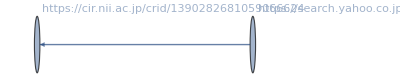
{20240824,{201,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{1032679,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$8892415<>epath$8892415,epath$8892415],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$9124901<>epath$9124901,epath$9124901],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[{}⟦1⟧,1]==/,pathhead$9263893<>epath$9263893,epath$9263893],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{1032679,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{420283,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{403448,3}

上が分離されたストーリー

```mathematica
storyGrIdxFlDs3[4][[1]]
```

{20240824,{1,1},}

#### Pre Op 2.1.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
Directory[]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20240824/T=4/_story

```mathematica
Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]
```

{60.9217,Null}

{0.000331,Null}

{0.204442,Null}

{0.565614,Null}

{0.010932,Null}

{0.000338,Null}

{0.011253,Null}

{0.013465,Null}

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

#### Pre Op 2.2

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/elecom/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story.

$Failed

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.008672,Null}

## Analysis

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186165}

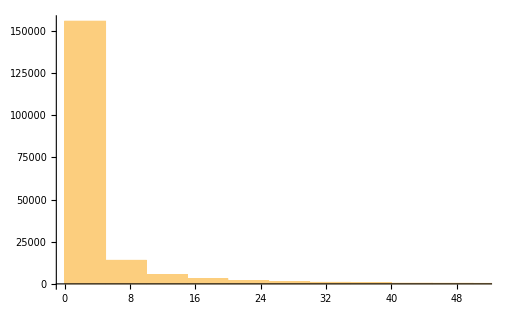

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186165}

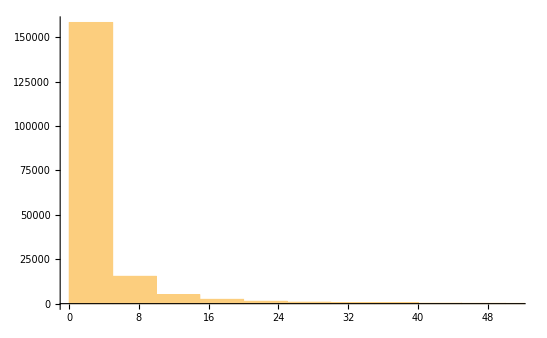

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{186165}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{186165}

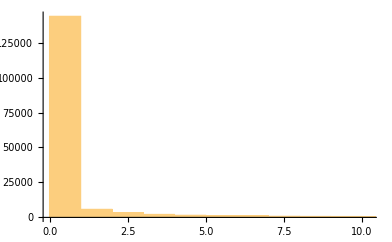

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{186165}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{186165}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{186165}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{186165}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{34,40,41,58,61,72,77,103,161,162,166,167,169,181,197,227,228,229,231,232,233,234,235,245,312,332,333,397,401,436,452,460,622,666,730,732,836,882,885,1130,1152,1153,1155,1206,1522,1631}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:lms.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:analytics.la.lms.nii.ac.jp,https:analytics.la.test.lms.nii.ac.jp,https:api.ci.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii.ac.jp,https:cir-nii-ac-jp.bukkyo.idm.oclc.org,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.swu.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:core.orthros.gakunin.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:niu.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:support.nii.ac.jp,https:tohoku.repo.nii.ac.jp,https:tohtech.repo.nii.ac.jp,https:tokoha-u.repo.nii.ac.jp,https:webfront2.nii.ac.jp:443,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{186165}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,164123},{1,22038},{3,4}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1800,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,145587},{2,40571},{0,7}}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{54,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 145372
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20274
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 19934
https:cir.nii.ac.jp
https:support.nii.ac.jp | 127
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jdcat.jsps.go.jp | 38
https:cir.nii.ac.jp
https:www.nii.ac.jp | 5
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 72
https:jupyter.cs.rcos.nii.ac.jp | 70
https:cir.nii.ac.jp
https:www.unii.ac.jp | 14
https:lms.nii.ac.jp | 107
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 46
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:support.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 5
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 3
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.swu.idm.oclc.org | 3
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 7
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 10
https:cir.nii.ac.jp
https:cir-nii-ac-jp.nanzan-u.idm.oclc.org | 3
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
https:core.orthros.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:tohtech.repo.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 5
https:cir.nii.ac.jp
https:cir-nii-ac-jp.translate.goog | 2
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 8
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:tohoku.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.bukkyo.idm.oclc.org | 1
 | 7
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:www.nii.ac.jp | 1
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 6
https:analytics.la.test.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443
https:cir.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com
https:cir.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 2
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:ci-nii-ac-jp.cdn.ampproject.org
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:cir.nii.ac.jp
https:tokoha-u.repo.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:api.ci.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 1
https:cir.nii.ac.jp
https:webfront2.nii.ac.jp:443 | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90943×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.90951×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

2557038

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{15641,15400,14930,17957,17538,16736,16633,18048,17053,17045,19571,14858,17031,14912,12885,14700,14827,19503,17447,16164,14510,11866,10697,10259,12226,11674,12400,13942,11974,14300,11507,12327,11585,12235,13559,11868,9616,12919,14456,12646,14017,14760,13279,14891,11322,12413,14399,14230,12790,14020,12749,11245,11892,14435,14650,17372,16077,16478,15665,15796,14441,15398,16139,15649,17087,16308,16112,19271,19844,19842,19628,17004,15687,14906,14706,15601,17537,16595,17176,18400,17677,19190,21139,23122,20992,23251,21989,21082,24144,20845,20141,21648,24282,23536,24762,22934,20558,22629,23352,23309,24082,23870,23467,23131,20671,19542,21954,18599,17608,20921,22195,18824,20949,20980,19504,21505,19761,20354,21180,20752,20938,20587,19797,21318,20327,17673,18645,19109,19912,20250,20035,21223,21739,21954,20465,20884,20491,21812,20432,22276,22955,22605,22735}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{1,33,17,26,70,2,12,31,19,3,1,2,5,9,24,2,58,1,2,2,4708,141,6,2,0,1,19,1,59,2,0,0,17,1,0,1,1,2,23,1,58,1,2,0,17,1,2,2,0,0,17,85,60,101,70,16,36,4,1,5,444,0,97,6,428,156,109,121,133,111,226,115,85,44,60,39,98,64,197,652,480,452,934,505,267,243,118,72,236,116,320,176,272,353,128,228,42,7,48,5,91,13,195,196,651,382,273,406,448,18,483,13,66,59,2,3,17,0,2,2,2,2,18,1,60,12,5,0,23,0,6,3,12,3,29,3,62,0,4,1,17,3,0}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{2,2,7,0,5,0,74,16,0,0,42,1,1,3,0,3,0,0,1,0,0,45,221,2,57,158,39,1,8,0,2,1,0,8,4,1,0,2,0,2,1,0,26,2,0,12,3,1,0,0,8,8,5,21,0,6,8,3,4,72,36,2,50,63,1,3,127,382,708,733,244,45,37,73,511,288,155,25,39,51,145,67,142,31,3,31,45,82,108,54,2,29,2,1,1,41,118,0,6,1,12,99,130,1,22,6,29,26,2,14,2,7,8,4,2,50,2,6,63,34,8,6,2,3,2,22,4,2,6,7,8,5,2,5,4,31,101,108,4,10,2,3,16}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{38,47,74,46,11,2,13,18,17,0,10,4,27,20,28,26,23,14,27,52,43,45,48,40,36,38,36,36,38,58,23,11,31,70,51,53,28,45,63,42,40,13,47,43,48,42,44,12,42,40,54,64,19,7,53,54,43,70,74,30,62,34,28,22,34,61,50,39,62,43,71,41,39,38,53,38,40,40,34,36,45,69,77,56,48,43,54,43,71,58,67,115,231,82,42,23,33,44,45,42,55,25,38,50,55,55,57,12,66,53,62,57,126,207,65,34,58,47,56,39,25,42,75,68,47,35,45,49,37,36,51,21,52,51,1,45,50,29,12,29,35,48,36}

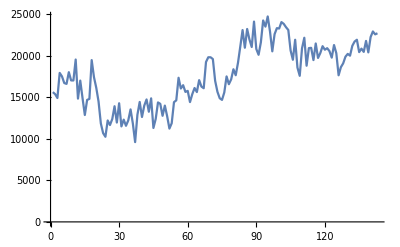

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

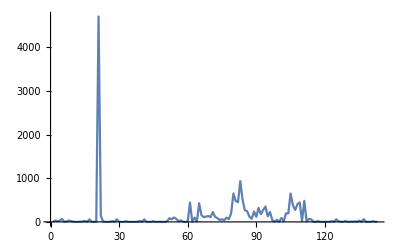

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

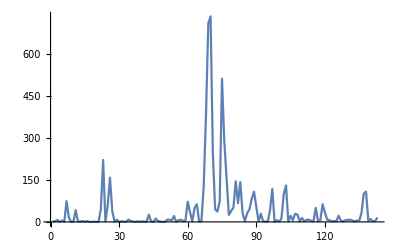

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

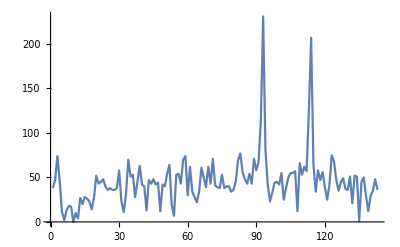

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{99,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{17,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{101,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{101,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{101,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1573,1},{7088,1},{8561,1},{11060,1},{15038,1},{19369,1},{19523,1},{21370,1},{21376,1},{21473,1},{21689,1},{28729,1},{28985,1},{28985,1},{28985,1},{29113,1},{29234,1},{29989,1},{33554,1},{36594,1},{37594,1},{42418,1},{43890,1},{48565,1},{49170,1},{49733,1},{51268,1},{51701,1},{56865,1},{59808,1},{59808,1},{59808,1},{62885,1},{63160,1},{63160,1},{64191,1},{64540,1},{64540,1},{64540,1},{72164,1},{72525,1},{74616,1},{75978,1},{81946,1},{85006,1},{85040,1},{85040,1},{85040,1},{94427,1},{99062,1},{99527,1},{101752,1},{101976,1},{102058,1},{102058,1},{103687,1},{104234,1},{104542,1},{104542,1},{104543,1},{104543,1},{104547,1},{104723,1},{105495,1},{105495,1},{105495,1},{105495,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105818,1},{105995,1},{106034,1},{106034,1},{106034,1},{107502,1},{110157,1},{110834,1},{111835,1},{112128,1},{113311,1},{114850,1},{118446,1},{119111,1},{119138,1},{120490,1},{121384,1},{121384,1},{121384,1},{124291,1},{126931,1},{140074,1},{142827,1},{147026,1},{155593,1},{159924,1},{163957,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{1,14,28,1,5,15,59,1,1,1,1,1,153,140,150,55,42,63,148,15,12,1,17,52,13,42,1,32,75,667,512,513,56,83,111,5,43,22,23,29,13,14,19,6,8,15,34,16,17,23,68,1,37,76,81,12,30,13,16,25,40,9,22,92,108,98,94,650,652,743,652,656,657,652,26,45,265,269,267,100,20,1,27,4,1,64,5,87,18,35,50,48,49,14,7,37,15,2,5,1373,22}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{101}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,0.716667,1.03333,0,0.433333,86.7333,464.733,0,0,0,0,0,64.7833,72.8333,72.8333,11.2833,243.067,67.05,351.3,7.96667,7.68333,0,15.95,16.8,73.05,19.5833,0,21.1167,37.7833,107.017,7.48333,7.48333,151.6,273.583,344.167,0.3,171.733,128.767,128.767,37.0667,37.55,8.03333,0.416667,2.05,1.78333,228.283,175.817,227.85,4.78333,6.01667,1107.65,0,160.133,139.1,54.85,0.65,157.65,26.65,26.4667,99.0333,98.8167,280.433,192.583,88.9167,107.2,168.25,168.25,67.6,67.6,94.25,67.6,67.6,67.6,67.6,11.4667,100.233,118.8,118.8,118.717,10.8667,6.05,0,89.9167,0.2,0,120.667,134.833,7.85,61.5333,2.63333,4.81667,4.81667,4.81667,2.15,1.06667,2.08333,15.2667,0.0833333,240.6,26.95,13.7667}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

```mathematica
staytimeCKAN/60
```

{0.,3.01667,3.93333,0.,1.03333,168.167,488.433,0.,0.,0.,0.,0.,320.967,320.767,320.767,34.7333,266.9,82.7167,593.283,27.5333,12.9833,0.,24.5167,25.3667,119.95,54.8667,0.,64.5,66.,216.617,55.4333,55.4333,292.917,493.683,504.233,0.633333,478.267,143.483,144.133,85.4,46.3,11.6333,2.41667,2.56667,3.63333,232.433,248.933,232.433,12.4333,9.11667,1340.15,0.,452.65,243.383,94.8,1.71667,256.633,29.6333,34.85,199.633,223.367,284.483,205.,307.383,473.533,375.517,307.383,555.7,555.7,699.583,555.7,575.017,555.7,555.7,26.8333,220.95,447.3,447.1,447.1,67.6167,30.1833,0.,104.583,0.366667,0.,203.283,170.533,54.3167,122.517,12.2667,20.9833,20.3667,20.3667,3.26667,2.95,10.3333,25.6167,0.0833333,432.633,1438.48,22.9833}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwihwqOM0dGCAxVGNN4KHW73BGMQFnoECAcQAQ&usg=AOvVaw1TP0cPw4owrZdTH0aWcRIf⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwiaq_TUkNKCAxUPsFYBHRnID74QFnoECAUQAQ&usg=AOvVaw3bwiI2wZC5Md_ZZTpkmgcf⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{101}

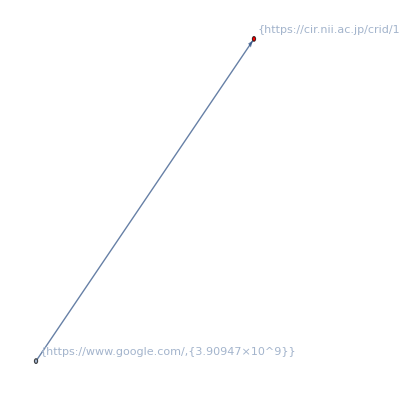
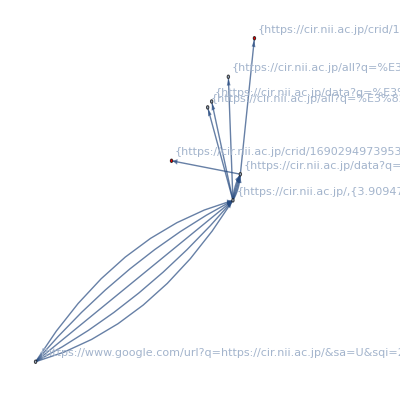
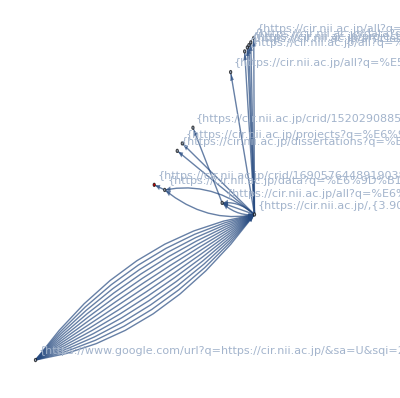
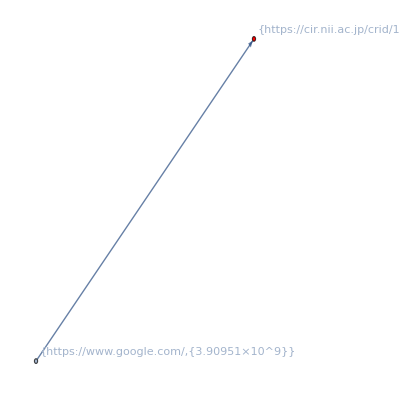
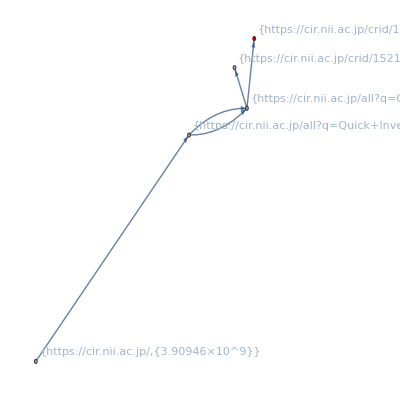
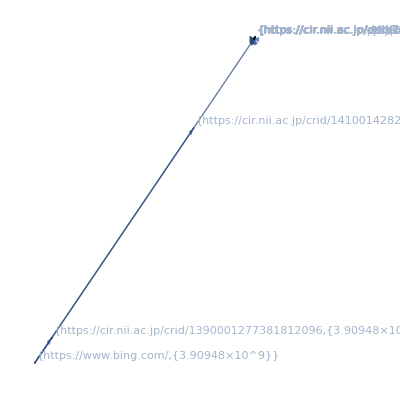
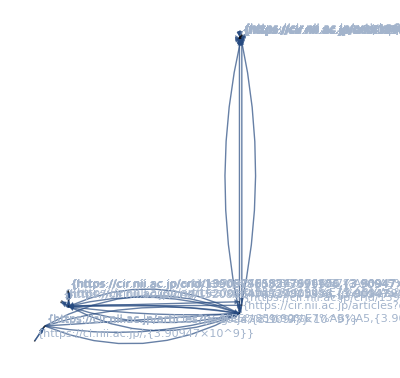
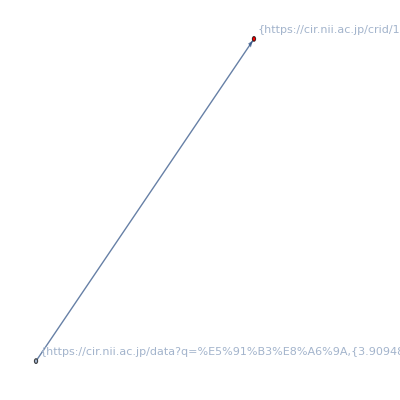
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 22645372
2587383

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 188
25
213 | 159
14
159

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 186165
101

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100
101 | 1573 | 1
7088 | 1
8561 | 1
11060 | 1
15038 | 1
19369 | 1
19523 | 1
21370 | 1
21376 | 1
21473 | 1
21689 | 1
28729 | 1
28985 | 1
28985 | 1
28985 | 1
29113 | 1
29234 | 1
29989 | 1
33554 | 1
36594 | 1
37594 | 1
42418 | 1
43890 | 1
48565 | 1
49170 | 1
49733 | 1
51268 | 1
51701 | 1
56865 | 1
59808 | 1
59808 | 1
59808 | 1
62885 | 1
63160 | 1
63160 | 1
64191 | 1
64540 | 1
64540 | 1
64540 | 1
72164 | 1
72525 | 1
74616 | 1
75978 | 1
81946 | 1
85006 | 1
85040 | 1
85040 | 1
85040 | 1
94427 | 1
99062 | 1
99527 | 1
101752 | 1
101976 | 1
102058 | 1
102058 | 1
103687 | 1
104234 | 1
104542 | 1
104542 | 1
104543 | 1
104543 | 1
104547 | 1
104723 | 1
105495 | 1
105495 | 1
105495 | 1
105495 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105818 | 1
105995 | 1
106034 | 1
106034 | 1
106034 | 1
107502 | 1
110157 | 1
110834 | 1
111835 | 1
112128 | 1
113311 | 1
114850 | 1
118446 | 1
119111 | 1
119138 | 1
120490 | 1
121384 | 1
121384 | 1
121384 | 1
124291 | 1
126931 | 1
140074 | 1
142827 | 1
147026 | 1
155593 | 1
159924 | 1
163957 | 1 | 2
8
14
2
5
14
34
2
2
2
2
2
93
92
93
37
21
43
105
14
9
2
13
26
10
20
2
19
35
269
265
265
41
46
67
6
31
18
18
25
11
12
12
6
8
13
26
14
14
17
45
2
27
41
45
7
22
12
14
16
24
8
18
68
72
69
65
423
423
462
423
423
426
423
11
17
94
99
95
62
14
2
23
4
2
25
6
29
16
23
36
36
36
9
7
18
11
3
6
1099
17 | 1
14
28
1
5
15
59
1
1
1
1
1
153
140
150
55
42
63
148
15
12
1
17
52
13
42
1
32
75
667
512
513
56
83
111
5
43
22
23
29
13
14
19
6
8
15
34
16
17
23
68
1
37
76
81
12
30
13
16
25
40
9
22
92
108
98
94
650
652
743
652
656
657
652
26
45
265
269
267
100
20
1
27
4
1
64
5
87
18
35
50
48
49
14
7
37
15
2
5
1373
22 | 0
0.716667
1.03333
0
0.433333
86.7333
464.733
0
0
0
0
0
64.7833
72.8333
72.8333
11.2833
243.067
67.05
351.3
7.96667
7.68333
0
15.95
16.8
73.05
19.5833
0
21.1167
37.7833
107.017
7.48333
7.48333
151.6
273.583
344.167
0.3
171.733
128.767
128.767
37.0667
37.55
8.03333
0.416667
2.05
1.78333
228.283
175.817
227.85
4.78333
6.01667
1107.65
0
160.133
139.1
54.85
0.65
157.65
26.65
26.4667
99.0333
98.8167
280.433
192.583
88.9167
107.2
168.25
168.25
67.6
67.6
94.25
67.6
67.6
67.6
67.6
11.4667
100.233
118.8
118.8
118.717
10.8667
6.05
0
89.9167
0.2
0
120.667
134.833
7.85
61.5333
2.63333
4.81667
4.81667
4.81667
2.15
1.06667
2.08333
15.2667
0.0833333
240.6
26.95
13.7667 | 0.
3.01667
3.93333
0.
1.03333
168.167
488.433
0.
0.
0.
0.
0.
320.967
320.767
320.767
34.7333
266.9
82.7167
593.283
27.5333
12.9833
0.
24.5167
25.3667
119.95
54.8667
0.
64.5
66.
216.617
55.4333
55.4333
292.917
493.683
504.233
0.633333
478.267
143.483
144.133
85.4
46.3
11.6333
2.41667
2.56667
3.63333
232.433
248.933
232.433
12.4333
9.11667
1340.15
0.
452.65
243.383
94.8
1.71667
256.633
29.6333
34.85
199.633
223.367
284.483
205.
307.383
473.533
375.517
307.383
555.7
555.7
699.583
555.7
575.017
555.7
555.7
26.8333
220.95
447.3
447.1
447.1
67.6167
30.1833
0.
104.583
0.366667
0.
203.283
170.533
54.3167
122.517
12.2667
20.9833
20.3667
20.3667
3.26667
2.95
10.3333
25.6167
0.0833333
432.633
1438.48
22.9833

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{101}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{101}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.909940924989612×10^9

```mathematica
end-start
```

829.846626